# TO PROOFREAD AND CHECK IF ALL STATEMENTS REMAIN TRUE AFTER RERUN

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/scarpaflorent/Bureau

```mathematica
<<"rec/rec1.mx"
<<"rec/rec2.mx"
<<"rec/rec3.mx"
<<"rec/rec4.mx"
<<"rec/rec5.mx"
<<"rec/rec6.mx"
<<"rec/rec7.mx"
<<"rec/rec8.mx"
<<"rec/rec9.mx"
<<"rec/rec10.mx"
<<"rec/rec11.mx"
```

## Definitions

Numerical values of constants

```mathematica
nf=5; (* number of flavours *)
ΛQCD=0.217; (* QCD scale in GeV *)
Nc=3; (* colour number *)
b0=2 ⅇ^-EulerGamma; (* dimensionless *)
btmax=1.5; (* impact parameter in GeV^-1 delimiting the perturbative and nonperturbative domains *)
Tf=1/2; (* normalisation of the SU(3) generators *)
Cf=4/3;
```

Scales and coupling: btbar=b_T^*(b_C(b_T)) where    b_c(b_T)=√(b_T^2+(b_0/Q)^2)    and      b_T^*(b_T)=b_T/(√(1+(b_T/b_Tmax)^2))    ;    the TMD scale is μbar=b_0/btbar

```mathematica
αs[μ_]:=(4π)/((11-2/3 nf)Log[μ^2/ΛQCD^2]);
```

```mathematica
bc[bt_,Q_]:=√(bt^2+(b0/Q)^2);
```

```mathematica
btbar[bt_,Q_]:=√((bt^2+(b0/Q)^2)/(1+(bt/btmax)^2+(b0/(Q btmax))^2));
```

```mathematica
μbar[bt_,Q_]:=b0/btbar[bt,Q];
```

Collinear PDF from MSTW2008   (the xf function takes 4 arguments : xf[set,x,μ,parton_type], parton_type=0 for gluon, set=0 for central set)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/scarpaflorent/Bureau

```mathematica
<<"mstw2008code/mstwpdf.m";
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

```mathematica
ReadPDFGrid["Grids/mstw2008lo",0]
```

PDF grid read from Grids/mstw2008lo.00.dat

```mathematica
<<"mstw2008code/mstwpdf.m";
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

```mathematica
ParallelEvaluate[<<"mstw2008code/mstwpdf.m"];
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

«9 more identical outputs»

```mathematica
ReadPDFGrid["Grids/mstw2008lo",0]
```

$Aborted

```mathematica
ParallelEvaluate[ReadPDFGrid["Grids/mstw2008lo",0]];
```

PDF grid read from Grids/mstw2008lo.00.dat

PDF grid read from Grids/mstw2008lo.00.dat

PDF grid read from Grids/mstw2008lo.00.dat

«9 more identical outputs»

```mathematica
gMSTW[x_,μ_]:=xf[0,x,μ,0]/x;
```

```mathematica
qMSTW[x_,μ_]:=1/x(xf[0,x,μ,8]+xf[0,x,μ,7]+xf[0,x,μ,-2]+xf[0,x,μ,-1]+xf[0,x,μ,3]+xf[0,x,μ,-3]+xf[0,x,μ,4]+xf[0,x,μ,-4]+xf[0,x,μ,5]+xf[0,x,μ,-5]);
```

Perturbative Sudakov factor S_A(b_T;ζ=Q^2;μ=Q;μ_B=b_0/(b_T^*(b_c(b_T))))       where we have  μ2=μ^2 ; μb2=μb^2 ; Q2=Q^2   (Sresult is the analytical result of S)

```mathematica
S[μb_,Q_]:=(Nc/π Integrate[1/μ2 αs[√μ2](Log[Q2/μ2](1+αs[√μ2]/(4π)(67-3 π^2-20Tf nf)/9)-(11-2nf/Nc)/6),{μ2,μb2,Q2},Assumptions->{μb2∈Reals,μb2>0,Q2∈Reals,Q2>0,ΛQCD∈Reals,ΛQCD>0,Nc∈Integers,Nc>0,nf∈Integers,nf>0,ΛQCD^2<μb2,μb2<Q2}])/.μb2->μb^2/.Q2->Q^2//FullSimplify;
```

```mathematica
S[μb,Q]
```

1/(33-2 nf)12 Nc (-Log[Q^2]+Log[μb^2]+((-67+3 π^2+20 nf Tf) Log[Q^2] Log[μb^2/Q^2])/(3 (-33+2 nf) (Log[Q^2]-2 Log[ΛQCD]) (2 Log[ΛQCD]-Log[μb^2]))-2 Log[ΛQCD] Log[Log[Q^2]-2 Log[ΛQCD]]-Log[ΛQCD] Log[1/(-2 Log[ΛQCD]+Log[μb^2])]+1/6 (-11+(2 nf)/Nc) (Log[Log[Q^2]-2 Log[ΛQCD]]-Log[-2 Log[ΛQCD]+Log[μb^2]])+Log[Q^2] (Log[Log[Q^2]-2 Log[ΛQCD]]-Log[-2 Log[ΛQCD]+Log[μb^2]])+Log[ΛQCD] Log[-2 Log[ΛQCD]+Log[μb^2]]+((-67+3 π^2+20 nf Tf) (2 Log[ΛQCD] (Log[μb^2] (-1-Log[Log[Q^2]-2 Log[ΛQCD]]+Log[-2 Log[ΛQCD]+Log[μb^2]])+Log[Q^2] (1-Log[Log[Q^2]-2 Log[ΛQCD]]+Log[-2 Log[ΛQCD]+Log[μb^2]]))-(4 Log[ΛQCD]^2+Log[Q^2] Log[μb^2]) Log[(-2 Log[ΛQCD]+Log[μb^2])/(Log[Q^2]-2 Log[ΛQCD])]))/(3 (-33+2 nf) (Log[Q^2]-2 Log[ΛQCD]) (2 Log[ΛQCD]-Log[μb^2])))

```mathematica
Sresult[μb_,Q_]:=1/(33-2 nf)12 Nc (-Log[Q^2]+Log[μb^2]+((-67+3 π^2+20 nf Tf) Log[Q^2] Log[μb^2/Q^2])/(3 (-33+2 nf) (Log[Q^2]-2 Log[ΛQCD]) (2 Log[ΛQCD]-Log[μb^2]))-2 Log[ΛQCD] Log[Log[Q^2]-2 Log[ΛQCD]]-Log[ΛQCD] Log[1/(-2 Log[ΛQCD]+Log[μb^2])]+1/6 (-11+(2 nf)/Nc) (Log[Log[Q^2]-2 Log[ΛQCD]]-Log[-2 Log[ΛQCD]+Log[μb^2]])+Log[Q^2] (Log[Log[Q^2]-2 Log[ΛQCD]]-Log[-2 Log[ΛQCD]+Log[μb^2]])+Log[ΛQCD] Log[-2 Log[ΛQCD]+Log[μb^2]]+((-67+3 π^2+20 nf Tf) (2 Log[ΛQCD] (Log[μb^2] (-1-Log[Log[Q^2]-2 Log[ΛQCD]]+Log[-2 Log[ΛQCD]+Log[μb^2]])+Log[Q^2] (1-Log[Log[Q^2]-2 Log[ΛQCD]]+Log[-2 Log[ΛQCD]+Log[μb^2]]))-(4 Log[ΛQCD]^2+Log[Q^2] Log[μb^2]) Log[(-2 Log[ΛQCD]+Log[μb^2])/(Log[Q^2]-2 Log[ΛQCD])]))/(3 (-33+2 nf) (Log[Q^2]-2 Log[ΛQCD]) (2 Log[ΛQCD]-Log[μb^2])));
```

Nonperturbative Sudakov factor and TMD input S_NP(b_c(b_T))

```mathematica
Snptune[bt_,Q_,A_]:=A Log[Q] bc[bt,Q]^2;
```

## Normalised binned q_T-spectrum of 21/02/2020

```mathematica
qtCf1f1tunebtBIN[x_?NumericQ,Q_?NumericQ,A_?NumericQ,qtmin_?NumericQ,qtmax_?NumericQ]:=1/(2π)NIntegrate[qt bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}, {qt,qtmin,qtmax}];
```

```mathematica
NormqtCf1f1[x_?NumericQ,Q_?NumericQ,A_?NumericQ]:=1/(2π)NIntegrate[1/2 Q BesselJ[1,(bt Q)/2] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
NormqtCf1f1Q20btmax2 = NormqtCf1f1[10^-3,20,0.64]
NormqtCf1f1Q20btmax8= NormqtCf1f1[10^-3,20,0.04]
NormqtCf1f1Q30btmax2 = NormqtCf1f1[10^-3,30,0.64]
NormqtCf1f1Q30btmax8 = NormqtCf1f1[10^-3,30,0.04]
```

7.87614×10^7

8.21707×10^7

1.06253×10^8

1.08392×10^8

```mathematica
BIN5Q20btmax2=ParallelMap[qtCf1f1tunebtBIN[10^-3,20,0.64,#[[1]],#[[2]]]/NormqtCf1f1Q20btmax2&,{{0,5},{5,10}}]
```

{0.404912,0.595088}

```mathematica
BIN5Q20btmax8=ParallelMap[qtCf1f1tunebtBIN[10^-3,20,0.04,#[[1]],#[[2]]]/NormqtCf1f1Q20btmax8&,{{0,5},{5,10}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.431007,0.568993}

```mathematica
BIN2p5Q20btmax2=ParallelMap[qtCf1f1tunebtBIN[10^-3,20,0.64,#[[1]],#[[2]]]/NormqtCf1f1Q20btmax2&,{{0,2.5},{2.5,5},{5,7.5},{7.5,10}}]
```

{0.119229,0.285683,0.320774,0.274314}

```mathematica
BIN2p5Q20btmax8=ParallelMap[qtCf1f1tunebtBIN[10^-3,20,0.04,#[[1]],#[[2]]]/NormqtCf1f1Q20btmax8&,{{0,2.5},{2.5,5},{5,7.5},{7.5,10}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.132886,0.298121,0.31258,0.256414}

```mathematica
BIN5Q30btmax2=ParallelMap[qtCf1f1tunebtBIN[10^-3,30,0.64,#[[1]],#[[2]]]/NormqtCf1f1Q30btmax2&,{{0,5},{5,10},{10,15}}]
```

{0.24528,0.429123,0.325598}

```mathematica
BIN5Q30btmax8=ParallelMap[qtCf1f1tunebtBIN[10^-3,30,0.04,#[[1]],#[[2]]]/NormqtCf1f1Q30btmax8&,{{0,5},{5,10},{10,15}}]
```

{0.263755,0.42563,0.310615}

```mathematica
BIN2p5Q30btmax2=ParallelMap[qtCf1f1tunebtBIN[10^-3,30,0.64,#[[1]],#[[2]]]/NormqtCf1f1Q30btmax2&,{{0,2.5},{2.5,5},{5,7.5},{7.5,10},{10,12.5},{12.5,15}}]
```

{0.0692986,0.175981,0.218351,0.210772,0.180379,0.145219}

```mathematica
BIN2p5Q30btmax8=ParallelMap[qtCf1f1tunebtBIN[10^-3,30,0.04,#[[1]],#[[2]]]/NormqtCf1f1Q30btmax8&,{{0,2.5},{2.5,5},{5,7.5},{7.5,10},{10,12.5},{12.5,15}}]
```

{0.0770256,0.18673,0.220153,0.205477,0.172723,0.137891}

## Description of the different contributions to the q_T-spectrum

Convolution C[f_1^g f_1^g] : the PDF is non-analytical, preventing any analytical integration

```mathematica
qtCf1f1tunebt[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1GausPlot[qt_,R2_,x_,Q_]:=qt/(2π R2) ⅇ^(-qt^2/(2R2))gMSTW[x,Q]^2;
```

Incomplete convolutions C[f_1^g f_1^g] for demonstrating the role of the different elements of the convolution

```mathematica
qtCf1f1NoSa[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1NoSnp[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1NoS[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)qt*NIntegrate[bt  BesselJ[0,bt qt] gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtvalsQ8=Range[0,4,0.1];
qtvalsQ12=Range[0,6,0.1];
qtvalsQ30=Range[0,15,0.1];
```

```mathematica
qtCf1f1bt2Q8=Transpose[{qtvalsQ8,Map[qtCf1f1tunebt[10^-2,8,#,0.64]&,qtvalsQ8]}];
```

```mathematica
qtCf1f1bt2Q12=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1tunebt[10^-2,12,#,0.64]&,qtvalsQ12]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 34466. and 0.129267 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {21.404986676477260519602108246317584416829049587249755859375}. NIntegrate obtained 1.03045×10^-317 and 3.×10^-323 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.24168}. NIntegrate obtained 34422.9 and 0.155477 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {21.6849}. NIntegrate obtained 1.5×10^-322 and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {21.34340503856895326049991634675961904576979577541351318359375}. NIntegrate obtained -2.41836×10^-317 and 4.4×10^-323 for the integral and error estimates.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {21.4538495871602}. NIntegrate obtained 1.466×10^-320 and 3.5×10^-323 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {21.407582903179}. NIntegrate obtained 5.46244×10^-319 and 2.5×10^-323 for the integral and error estimates.

```mathematica
qtCf1f1bt2Q30=Transpose[{qtvalsQ30,Map[qtCf1f1tunebt[10^-2,30,#,0.64]&,qtvalsQ30]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.283381}. NIntegrate obtained 16732.8 and 0.234338 for the integral and error estimates.

```mathematica
qtCf1f1bt4Q8=Transpose[{qtvalsQ8,Map[qtCf1f1tunebt[10^-2,8,#,0.16]&,qtvalsQ8]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 56906.5 and 0.370139 for the integral and error estimates.

```mathematica
qtCf1f1bt4Q12=Transpose[{qtvalsQ12,Map[qtCf1f1tunebt[10^-2,12,#,0.16]&,qtvalsQ12]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 44200.3 and 0.105465 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.24168}. NIntegrate obtained 44118.7 and 0.210243 for the integral and error estimates.

```mathematica
qtCf1f1bt4Q30=Transpose[{qtvalsQ30,Map[qtCf1f1tunebt[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.283381}. NIntegrate obtained 19690.5 and 0.298801 for the integral and error estimates.

```mathematica
qtCf1f1bt8Q12=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1tunebt[10^-2,12,#,0.04]&,qtvalsQ12]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 48001.5 and 0.106351 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.24168}. NIntegrate obtained 47893.8 and 0.218975 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
qtCf1f1bt8Q30=Transpose[{qtvalsQ30,Map[qtCf1f1tunebt[10^-2,30,#,0.04]&,qtvalsQ30]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.283381}. NIntegrate obtained 20741.8 and 0.33105 for the integral and error estimates.

```mathematica
qtCf1f1NoSabt4Q8=Transpose[{qtvalsQ8,Map[qtCf1f1NoSa[10^-2,8,#,0.16]&,qtvalsQ8]}];
```

```mathematica
qtCf1f1NoSabt4Q12=Transpose[{qtvalsQ12,Map[qtCf1f1NoSa[10^-2,12,#,0.16]&,qtvalsQ12]}];
```

```mathematica
qtCf1f1NoSabt4Q30=Transpose[{qtvalsQ30,Map[qtCf1f1NoSa[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.252562}. NIntegrate obtained 62932.2 and 0.145241 for the integral and error estimates.

```mathematica
qtCf1f1NoSnpQ8=Transpose[{qtvalsQ8,Map[qtCf1f1NoSnp[10^-2,8,#]&,qtvalsQ8]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {8.16907×10^224}. NIntegrate obtained 8.21927639100886×10^55895 and 8.21927639100886×10^55895 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 67582.7 and 0.505633 for the integral and error estimates.

```mathematica
qtCf1f1NoSnpQ12=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1NoSnp[10^-2,12,#]&,qtvalsQ12]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {6.3887×10^56}. NIntegrate obtained 8.34977301508573×10^13978 and 8.34977301508573×10^13978 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 50353. and 0.116545 for the integral and error estimates.

```mathematica
qtCf1f1NoSnpQ30=Transpose[{qtvalsQ30,Map[qtCf1f1NoSnp[10^-2,30,#]&,qtvalsQ30]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {8.16907×10^224}. NIntegrate obtained 1.15722931645774×10^55894 and 1.15722931645774×10^55894 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.283381}. NIntegrate obtained 21182.7 and 0.339 for the integral and error estimates.

```mathematica
qtCf1f1NoSQ8=Transpose[{qtvalsQ8,Map[qtCf1f1NoS[10^-2,8,#]&,qtvalsQ8]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {8.16907×10^224}. NIntegrate obtained 8.02104830430843×10^55896 and 8.02104830430843×10^55896 for the integral and error estimates.

```mathematica
qtCf1f1NoSQ12=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1NoS[10^-2,12,#]&,qtvalsQ12]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {6.3887×10^56}. NIntegrate obtained 2.57262949719626×10^13980 and 2.57262949719626×10^13980 for the integral and error estimates.

```mathematica
qtCf1f1NoSQ30=Transpose[{qtvalsQ30,Map[qtCf1f1NoS[10^-2,30,#]&,qtvalsQ30]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {8.16907×10^224}. NIntegrate obtained 8.02104830430843×10^55896 and 8.02104830430843×10^55896 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.252562}. NIntegrate obtained 109679. and 0.145998 for the integral and error estimates.

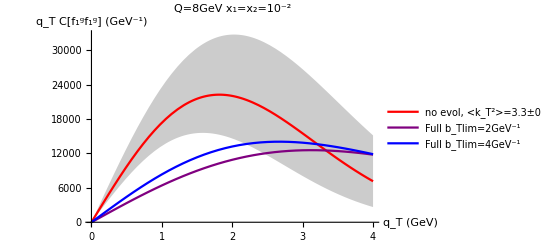
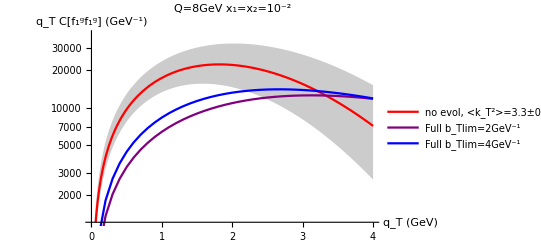

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,8]],qtCf1f1GausPlot[qt,3.3,10^-2,8],Max[qtCf1f1GausPlot[qt,R2,10^-2,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","no evol, <k_T^2>=3.3±0.8 GeV^2",""}]],ListPlot[{qtCf1f1bt2Q8,qtCf1f1bt4Q8},Joined->True,PlotStyle->{Purple,Blue,Green,Yellow,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},LogPlot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,8]],qtCf1f1GausPlot[qt,3.3,10^-2,8],Max[qtCf1f1GausPlot[qt,R2,10^-2,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","no evol, <k_T^2>=3.3±0.8 GeV^2",""}]],ListLogPlot[{qtCf1f1bt2Q8,qtCf1f1bt4Q8},Joined->True,PlotStyle->{Purple,Blue,Green,Yellow,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1","no S_A","no S_NP","no S_A or S_NP"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"]}
```

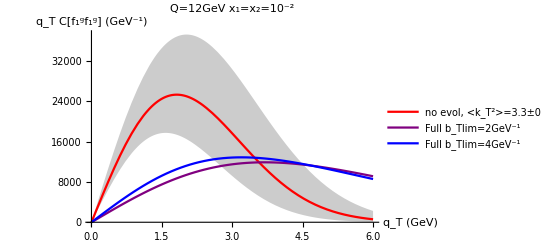
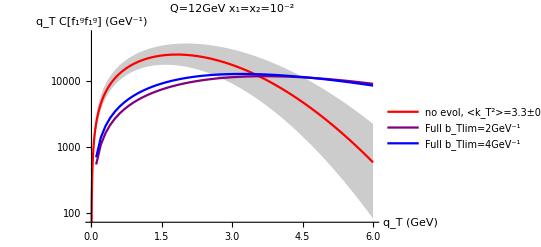

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","no evol, <k_T^2>=3.3±0.8 GeV^2",""}]],ListPlot[{qtCf1f1bt2Q12,qtCf1f1bt4Q12},Joined->True,PlotStyle->{Purple,Blue,Green,Yellow,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},LogPlot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","no evol, <k_T^2>=3.3±0.8 GeV^2",""}]],ListLogPlot[{qtCf1f1bt2Q12,qtCf1f1bt4Q12},Joined->True,PlotStyle->{Purple,Blue,Green,Yellow,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"]}
```

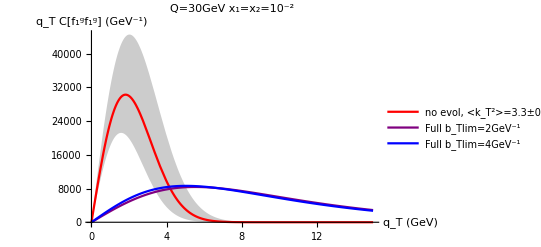
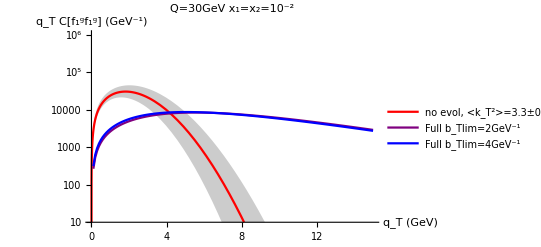

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","no evol, <k_T^2>=3.3±0.8 GeV^2",""}]],ListPlot[{qtCf1f1bt2Q30,qtCf1f1bt4Q30},Joined->True,PlotStyle->{Purple,Blue,Green,Yellow,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},LogPlot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","no evol, <k_T^2>=3.3±0.8 GeV^2",""},PlotRange->{10,10^6}]],ListLogPlot[{qtCf1f1bt2Q30,qtCf1f1bt4Q30},Joined->True,PlotStyle->{Purple,Blue,Green,Yellow,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},PlotRange->{10,10^6}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

If one replaces the TMDs by simple PDFs evaluated at a scale μ=Q, then the whole b_T-dependence in the convolution’s integrand is b_T J_0(b_T q_T)and the PDFs are constant. J_0oscillations tend towards a constant amplitude at large b_T. Therefore b_T J_0(b_T q_T) oscillations linearly increase with b_T.The integral diverges, as can easily be seen when doing the integration in momentum space.

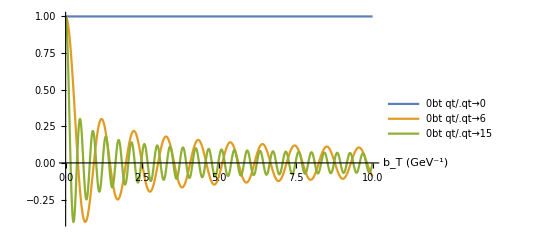
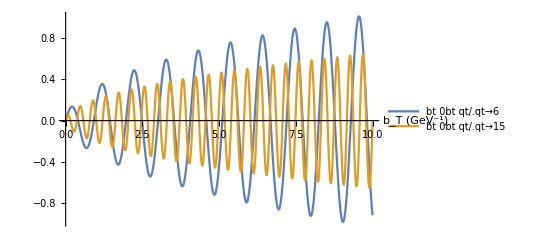

```mathematica
{Plot[{BesselJ[0,bt qt]/.qt->0,BesselJ[0,bt qt]/.qt->6,BesselJ[0,bt qt]/.qt->15},{bt,0,10},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],Plot[{bt  BesselJ[0,bt qt]/.qt->6,bt  BesselJ[0,bt qt]/.qt->15},{bt,0,10},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

```mathematica
Integrate[BesselJ[0,bt qt],{bt,0,∞}]
```

ConditionalExpression[1/Abs[qt],qt∈Reals]

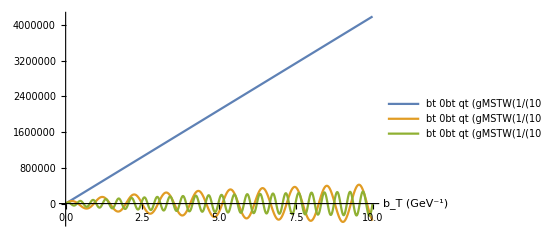

```mathematica
Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->0,bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->6,bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->15},{bt,0,10},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]
```

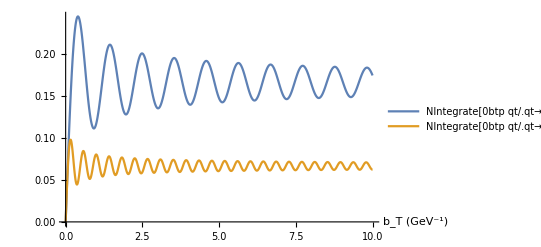
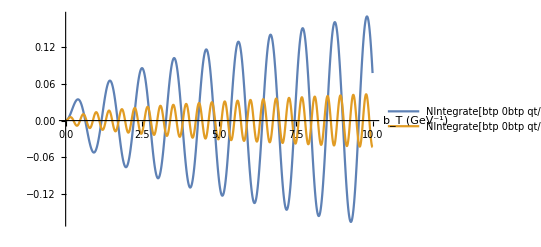

```mathematica
{Plot[{NIntegrate[BesselJ[0,btp qt]/.qt->6,{btp,0,bt}],NIntegrate[BesselJ[0,btp qt]/.qt->15,{btp,0,bt}]},{bt,0,10},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],Plot[{NIntegrate[btp  BesselJ[0,btp qt]/.qt->6,{btp,0,bt}],NIntegrate[btp  BesselJ[0,btp qt]/.qt->15,{btp,0,bt}]},{bt,0,10},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->0,{bt,0,∞},MaxRecursion->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in bt near {bt} = {1.98014577265121×10^459044}. NIntegrate obtained 1.71443540159204×10^114458344 and 1.71443540159204×10^114458344 for the integral and error estimates.

1.71443540159204×10^114458344

```mathematica
NIntegrate[qt*bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->0,{bt,0,∞},MaxRecursion->20]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->6,{bt,0,∞}]
```

NIntegrate::nconv: This oscillatory integral might not be convergent.

NIntegrate[bt BesselJ[0,bt qt] gMSTW[1/10^2,8]^2/.qt→6,{bt,0,∞}]

```mathematica
NIntegrate[qt*bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->6,{bt,0,∞}]
```

NIntegrate::nconv: This oscillatory integral might not be convergent.

NIntegrate[qt bt BesselJ[0,bt qt] gMSTW[1/10^2,8]^2/.qt→6,{bt,0,∞}]

Replacing the scale μ=Q in the PDFs by μ=μbar(b_T,Q) implements a b_T-dependence in the PDFs. The consequence will be that at larger b_T (>2 GeV^-1 approximately), the PDFs are strongly suppressed ; but because μbar also knows a lower bound, the PDFs will also reach a lower bound and will not keep decreasing ; thus although the oscillations are in a first time dampened by the decrease in value of the PDFs, once the latter reach their bound, they will no longer counter the amplification of oscillations with b_T. The integrand is still divergent at b_T=0 for q_T=0, but when multiplied by q_T (which appears multiplying the integrand in dσ/dq_T), the divergence cancels because q_T=0.

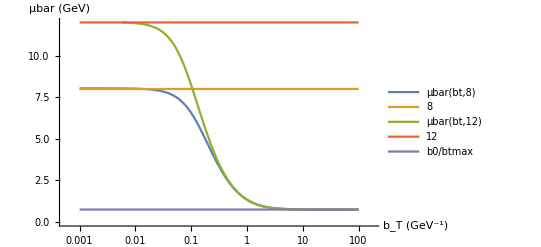
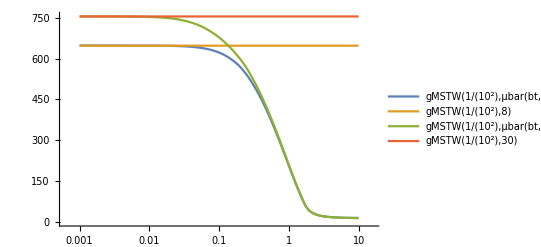

```mathematica
{LogLinearPlot[{μbar[bt,8],8,μbar[bt,12],12,b0/btmax},{bt,10^-3,10^2},PlotRange->{0,12},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)","μbar (GeV)"}],LogLinearPlot[{gMSTW[10^-2,μbar[bt,8]],gMSTW[10^-2,8],gMSTW[10^-2,μbar[bt,30]],gMSTW[10^-2,30]},{bt,10^-3,10},PlotLegends->"Expressions"]}
```

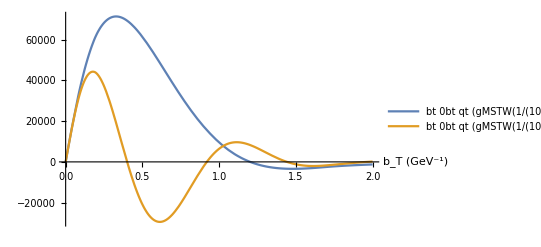
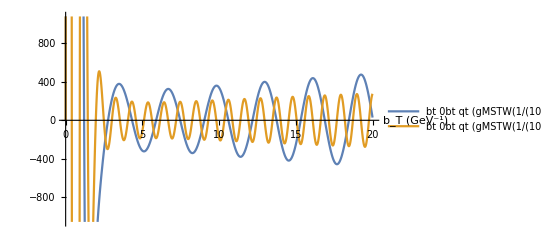

```mathematica
{Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->2,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->6},{bt,0,2},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->2,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->6},{bt,0,20},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->0,{bt,0,∞}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {8.16907×10^224}. NIntegrate obtained 8.02104830430843×10^55896 and 8.02104830430843×10^55896 for the integral and error estimates.

8.02104830430843×10^55896

```mathematica
NIntegrate[qt*bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->0,{bt,0,∞}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

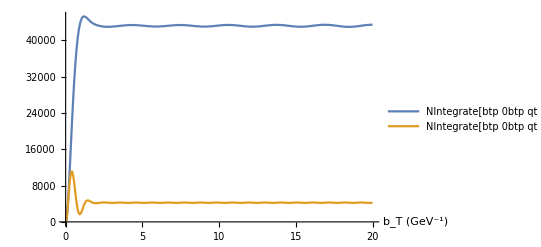

```mathematica
Plot[{NIntegrate[btp  BesselJ[0,btp qt] gMSTW[10^-2,μbar[btp,Q]]^2/.Q->8/.qt->2,{btp,0,bt}],NIntegrate[btp  BesselJ[0,btp qt] gMSTW[10^-2,μbar[btp,Q]]^2/.Q->8/.qt->6,{btp,0,bt}]},{bt,0,20},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]
```

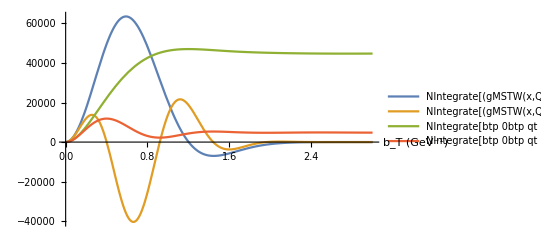

```mathematica
Plot[{NIntegrate[gMSTW[x,Q]^2 bt ⅇ^((-R2 bt^2)/2)BesselJ[0,bt qt]/.x->10^-2/.Q->12/.qt->2/.R2->3.3,{btp,0,bt}],NIntegrate[gMSTW[x,Q]^2 bt ⅇ^((-R2 bt^2)/2)BesselJ[0,bt qt]/.x->10^-2/.Q->12/.qt->6/.R2->3.3,{btp,0,bt}],NIntegrate[btp  BesselJ[0,btp qt] gMSTW[10^-2,μbar[btp,Q]]^2/.Q->12/.qt->2,{btp,0,bt}],NIntegrate[btp  BesselJ[0,btp qt] gMSTW[10^-2,μbar[btp,Q]]^2/.Q->12/.qt->6,{btp,0,bt}]},{bt,0,3},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]
```

Even though the PDFs tend towards a constant value and the oscillations resume increasing at large b_T, they are now tamed enough to make the integral finite. The value of the integral is mostly determined by low b_T values, where there is an imbalance in the oscillations. At large b_T, the oscillations get more and more balanced, and therefore contribute less and less to the integral, even if their amplitude increases.

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->6,{bt,0,∞}]
```

4226.65

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->15,{bt,0,∞}]
```

146.266

At b_T≃10^6, the oscillations’ amplitude is very large, yet the integral over a period π is very close to 0.

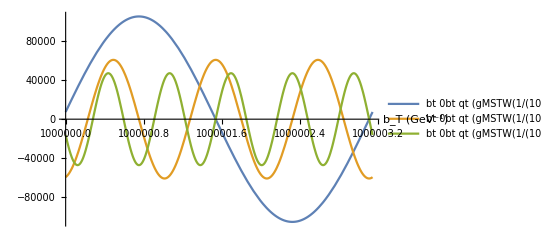

```mathematica
Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->2,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->6,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->10},{bt,1000000,1000000+π},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]
```

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->6,{bt,1000000,1000000+π},MaxRecursion->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00334298 and 2.11151×10^-6 for the integral and error estimates.

-0.00334298

Compared with a non-evolved gaussian b_T-dependence that supresses any contribution beyond 2 GeV^-1, the PDF still allows a small contribution for b_Tvalues larger than 2 GeV^-1 but the suppression happens earlier. The consequence is a notable difference of behaviour of the integrand with increasing values of q_T. In the gaussian case, the oscillations balance is reached very quickly with increasing q_T, meaning the integral (and therefore dσ/dq_T) becomes quickly negligible at large q_T. Moreover, the exponential decrease in b_T of the gaussian cancels the linear increase from the b_Tfactor ; if larger b_T values contributed a bit, they cannot at all in the gaussian case.
In the g(x,μbar) case, the balance is reached much slowlier, allowing for a non-negligible q_T-spectrum at much larger values ; in addition, the larger b_T values, even though they contribute less, can still increase the value of the integral (moderate b_T, although this second effect might be negligible): the spectrum therefore develops a tail.
Nevertheless, the small-q_T shapes of the spectra are very similar (the peaks are at the same position, but this is a coincidence, taking a different <k_T^2> for the Gaussian would shift the peak).

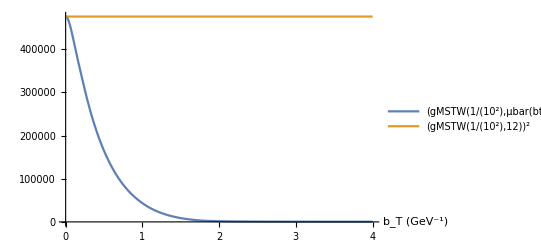
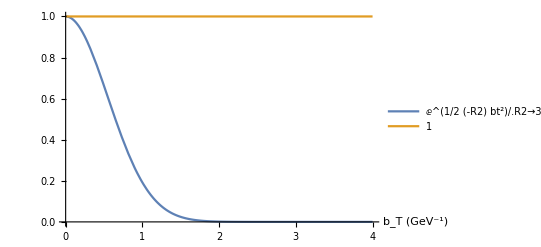

```mathematica
{Plot[{gMSTW[10^-2,μbar[bt,12]]^2,gMSTW[10^-2,12]^2},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],Plot[{ⅇ^((-R2 bt^2)/2)/.R2->3.3,1},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

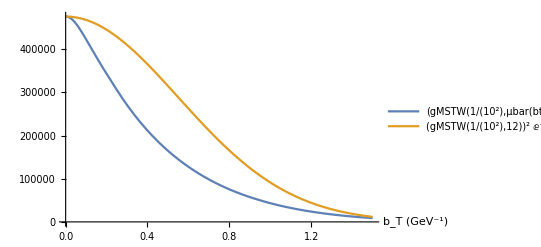

```mathematica
Plot[{gMSTW[10^-2,μbar[bt,12]]^2,gMSTW[10^-2,12]^2 ⅇ^((-R2 bt^2)/2)/.R2->3.3},{bt,0,1.5},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]
```

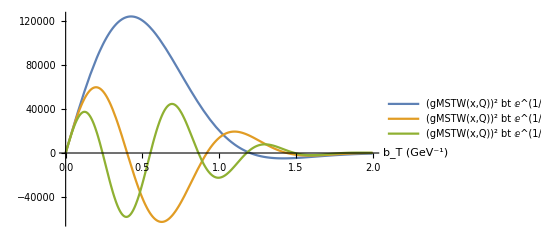
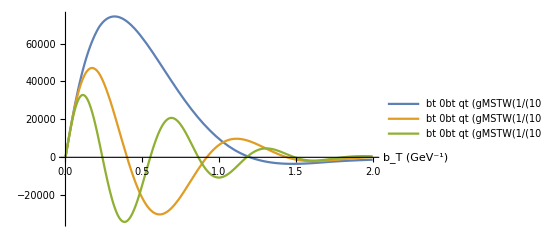

```mathematica
{Plot[{ gMSTW[x,Q]^2 bt ⅇ^((-R2 bt^2)/2)BesselJ[0,bt qt]/.x->10^-2/.Q->12/.qt->2/.R2->3.3,gMSTW[x,Q]^2 bt ⅇ^((-R2 bt^2)/2)BesselJ[0,bt qt]/.x->10^-2/.Q->12/.qt->6/.R2->3.3,gMSTW[x,Q]^2 bt ⅇ^((-R2 bt^2)/2)BesselJ[0,bt qt]/.x->10^-2/.Q->12/.qt->10/.R2->3.3},{bt,0,2},PlotRange->All,PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->12/.qt->2,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->12/.qt->6,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->12/.qt->10},{bt,10^-3,2},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

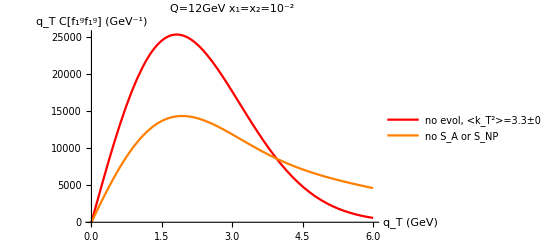

```mathematica
Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,12],{qt,0,6},PlotStyle->Red,PlotLegends->{"no evol, <k_T^2>=3.3±0.8 GeV^2"}],ListPlot[qtCf1f1NoSQ12,Joined->True,PlotStyle->Orange,PlotLegends->{"no S_A or S_NP"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"]
```

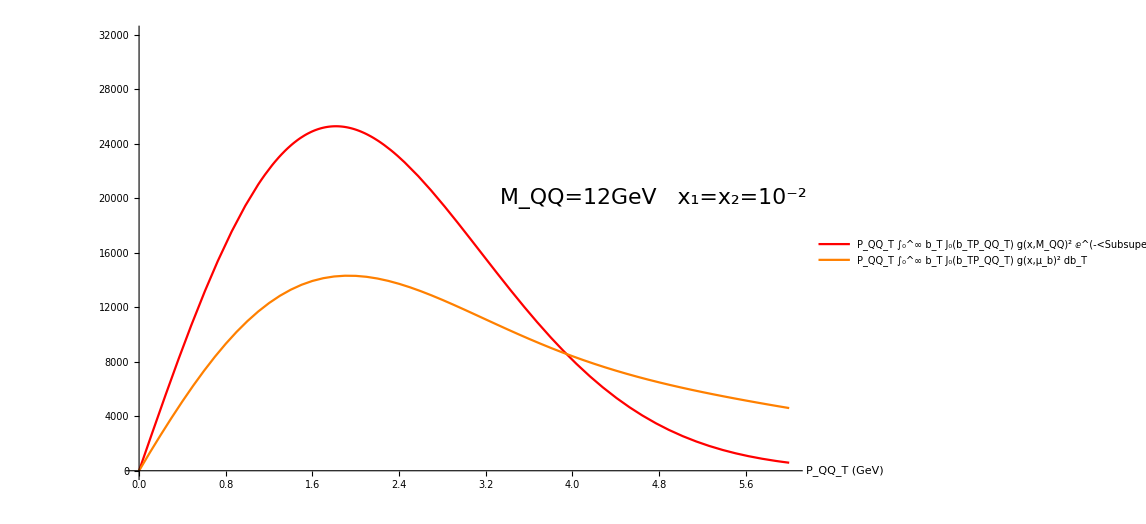

```mathematica
Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,12],{qt,0,6},PlotStyle->Red,PlotLegends->Placed[{Style["P_QQ_T ∫_0^∞ b_T J_0(b_TP_QQ_T) g(x,M_QQ)^2 ⅇ^(-<SubsuperscriptBox[k, T, 2]>SubsuperscriptBox[b, T, 2]/4) db_T",18]},{0.63,0.96}]],ListPlot[qtCf1f1NoSQ12,Joined->True,PlotStyle->Orange,PlotLegends->Placed[{Style["P_QQ_T ∫_0^∞ b_T J_0(b_TP_QQ_T) g(x,μ_b)^2 db_T",18]},{0.56,0.86}]],AxesLabel->{Style["P_QQ_T (GeV)",18],},Epilog->Text[Style["M_QQ=12GeV   x_1=x_2=10^-2",22],Scaled[{.78,.62}]],TicksStyle->Large,PlotRange->{0,32000}]
```

```mathematica
CombNODPS=Show[Plot[fitLS4RsqGausNODPSNOBIN["BestFit"],{qt,0,8},PlotStyle->Red,PlotLegends->Placed[{Style["Gaussian model fit",18]},{0.83,0.63}]],ErrorListPlot[LHCb13datNODPSPlot4,PlotMarkers->"+",PlotStyle->Black,PlotLegends->Placed[{Style["Normalised LHCb
data without DPS",18]},{0.82,0.51}]],AxesLabel->{Style["  q_T (GeV)",18],Style["dσ/dq_T /∫_0^(<SubscriptBox[M, ψψ]>/2) dσ/dq_T dq_T (GeV^-1)
",18]},TicksStyle->Large,PlotRange->{{0.1,7.9},{0.02,0.38}},Epilog->Text[Style["<M_ψψ> = 8 GeV
<k_T^2> = 3.74 ± 0.75 GeV^2
χ_(d . o . f)^2 = 0.34",18],Scaled[{.7,.88}]]]
```

The addition of the perturbative Sudakov factor S_A can enhance the previously observed effect of b_T-narrowing of integrand ↔ q_T-broadening of integral. Even though, as the PDFs, it knows a lower bound due to the use of the scale μbar, it can suppress even further large b_T values, this suppression knowing a Q-dependence. At Q=8GeV, the Sudakov factor is softly suppressing, and its effect not so strong. Yet, it stills allows to reduce the decrease in the values of the integrals for two given q_T. Combined with the q_Tfactor added to describe dσ/dq_T, this even allows to shift the peak of the q_T-spectrum towards larger values of q_T, in addition to developing a tail. (if we were plotting C[f_1^g f_1^g] alone, it would always be maximal at q_T=0)
The enhancement due to S_A>1 for b_T ≃ 0.1 - 1 GeV^-1 may also contribute to the increased contribution of small-b_T values. This effect might not be physically sound.

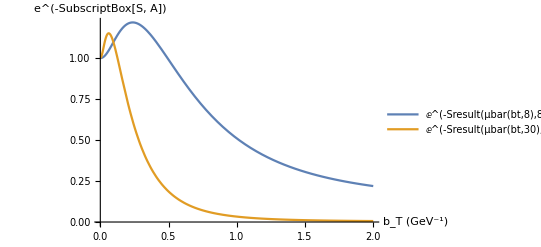
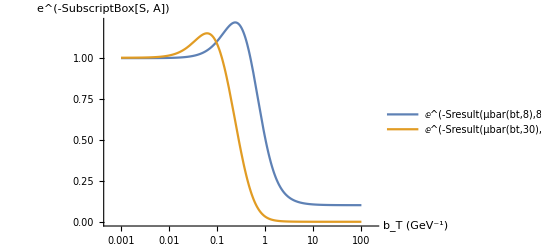

```mathematica
{Plot[{ⅇ^(-Sresult[μbar[bt,8],8]),ⅇ^(-Sresult[μbar[bt,30],30])},{bt,0,2},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)","e^(-SubscriptBox[S, A])"}],LogLinearPlot[{ⅇ^(-Sresult[μbar[bt,8],8]),ⅇ^(-Sresult[μbar[bt,30],30])},{bt,10^-3,10^2},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)","e^(-SubscriptBox[S, A])"}]}
```

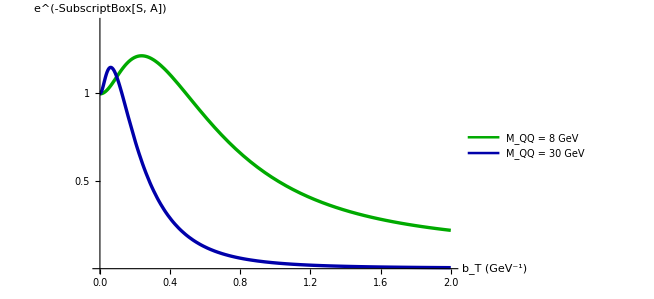

```mathematica
Show[{Plot[ⅇ^(-Sresult[μbar[bt,8],8]),{bt,0,2},PlotStyle->{Darker[Green],Thickness[0.005]},PlotLegends->Placed[{Style["M_QQ = 8 GeV",18]},{0.66,0.86}]],Plot[ⅇ^(-Sresult[μbar[bt,30],30]),{bt,0,2},PlotStyle->{Darker[Blue],Thickness[0.005]},PlotLegends->Placed[{Style["M_QQ = 30 GeV",18]},{0.675,0.72}]]},AxesLabel->{Style["  b_T (GeV^-1)",18],Style["e^(-SubscriptBox[S, A])",18]},TicksStyle->Large,PlotRange->{0,1.4},AxesOrigin->{0,0},Ticks->{Automatic,{0.5,1}}]
```

```mathematica
MatrixForm[esadat=Table[{bt,ⅇ^(-Sresult[μbar[bt,12],12]),ⅇ^(-Sresult[μbar[bt,30],30])},{bt,0,2,0.01}]];
Export["esa.dat",esadat];
```

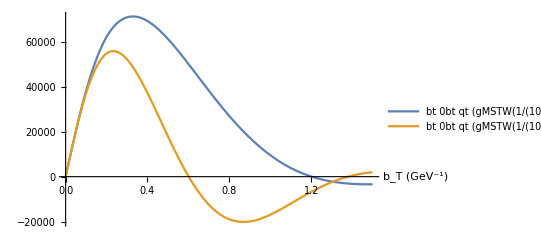
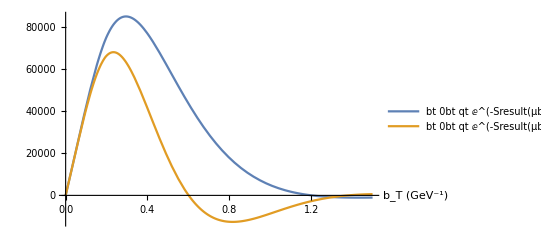

```mathematica
{Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->2,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->4},{bt,0,1.5},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],

Plot[{bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->2,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->4},{bt,0,1.5},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

At large Q, the effect is much stronger. For Q=30GeV, the Sudakov factor makes negligible everything beyond b_T=1 GeV^-1, making a noticeably stronger cut in the b_Tintegrand. In such a configuration, the difference between the integrands for two q_Tvalues is even smaller, and the q_T-spectrum is noticeably broader, and its peak at a noticeably larger q_Tvalue.

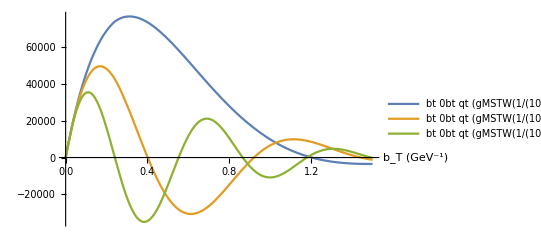
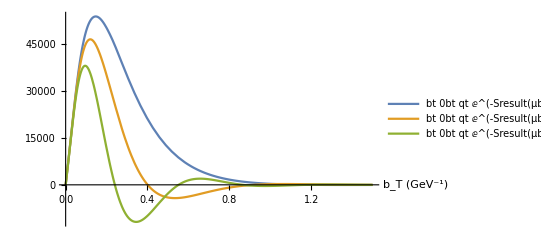

```mathematica
{Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->30/.qt->2,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->30/.qt->6,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->30/.qt->10},{bt,0,1.5},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],

Plot[{bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->30/.qt->2,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->30/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->30/.qt->10},{bt,0,1.5},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

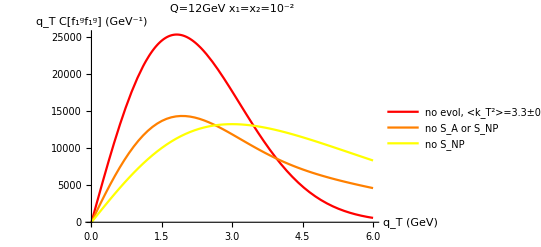
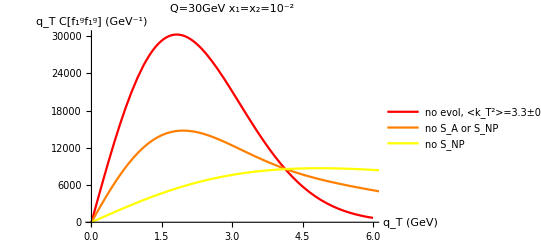

```mathematica
{Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,12],{qt,0,6},PlotStyle->Red,PlotLegends->{"no evol, <k_T^2>=3.3±0.8 GeV^2"}],ListPlot[{qtCf1f1NoSQ12,qtCf1f1NoSnpQ12},Joined->True,PlotStyle->{Orange,Yellow},PlotLegends->{"no S_A or S_NP","no S_NP"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"],

Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,30],{qt,0,6},PlotStyle->Red,PlotLegends->{"no evol, <k_T^2>=3.3±0.8 GeV^2"}],ListPlot[{qtCf1f1NoSQ30,qtCf1f1NoSnpQ30},Joined->True,PlotStyle->{Orange,Yellow},PlotLegends->{"no S_A or S_NP","no S_NP"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

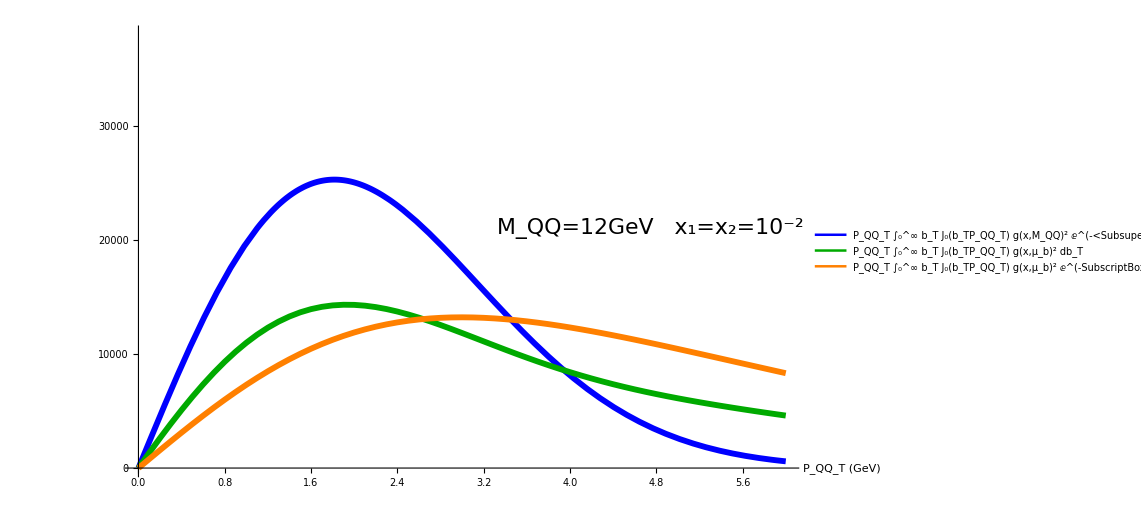

```mathematica
Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,12],{qt,0,6},PlotStyle->{Blue,Thickness[0.005]},PlotLegends->Placed[{Style["P_QQ_T ∫_0^∞ b_T J_0(b_TP_QQ_T) g(x,M_QQ)^2 ⅇ^(-<SubsuperscriptBox[k, T, 2]>SubsuperscriptBox[b, T, 2]/4) db_T",20]},{0.53,0.96}]],ListPlot[qtCf1f1NoSQ12,Joined->True,PlotStyle->{Darker[Green],Thickness[0.005]},PlotLegends->Placed[{Style["P_QQ_T ∫_0^∞ b_T J_0(b_TP_QQ_T) g(x,μ_b)^2 db_T",20]},{0.46,0.86}]],ListPlot[qtCf1f1NoSnpQ12,Joined->True,PlotStyle->{Orange,Thickness[0.005]},PlotLegends->Placed[{Style["P_QQ_T ∫_0^∞ b_T J_0(b_TP_QQ_T) g(x,μ_b)^2 ⅇ^(-SubscriptBox[S, A]) db_T",20]},{0.49,0.76}]],AxesLabel->{Style["P_QQ_T (GeV)",18],},Epilog->Text[Style["M_QQ=12GeV   x_1=x_2=10^-2",22],Scaled[{.78,.55}]],TicksStyle->Large,PlotRange->{0,38000},Ticks->{Automatic,{0,10000,20000,30000}}]
```

It could be that the change of scale in the PDFs may also change their large-b_Tsuppressing power by narrowing their b_T-slope. As one can see, this is not the case ; the only change is therefore a numerical overall factor. It is also seen in the absence of change in the shape of the q_T-spectrum with no S_A when Q varies.

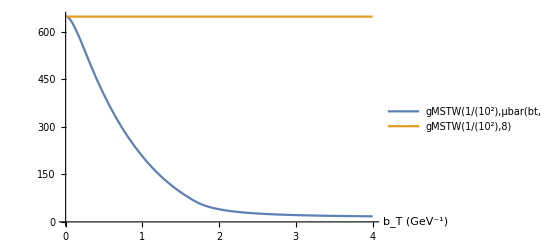
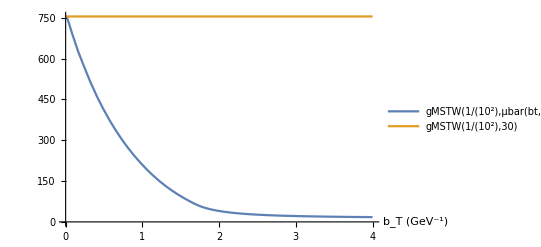

```mathematica
{Plot[{gMSTW[10^-2,μbar[bt,8]],gMSTW[10^-2,8]},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],Plot[{gMSTW[10^-2,μbar[bt,30]],gMSTW[10^-2,30]},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

The possibility for the nonperturbative Sudakov factor S_NP to broaden the q_T-spectrum, is directly connected to its possibility to narrow down even further the b_T-integrand (or not). A S_NP becoming small at b_Tlim= 4 GeV^-1or larger will be less narrowing than S_A and therefore have little to no broadening effect on the q_T-spectrum. A narrower S_NP (b_Tlim=2 GeV^-1) will have a moderate but noticeable effect at small Q=8GeV. At large Q, where the perturbative Sudakov factor is strongly suppressing (b_T>1 GeV^-1 already suppressed), the nonperturbative Sudakov factor will have almost no visible effect.

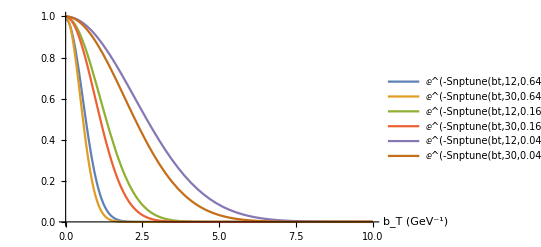
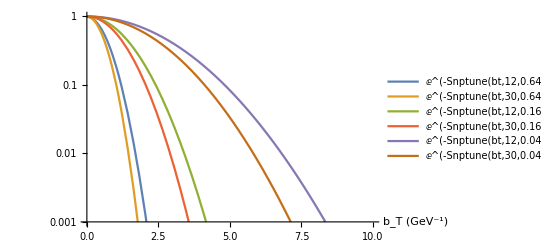

```mathematica
{Plot[{ⅇ^(-Snptune[bt,12,0.64]),ⅇ^(-Snptune[bt,30,0.64]),ⅇ^(-Snptune[bt,12,0.16]),ⅇ^(-Snptune[bt,30,0.16]),ⅇ^(-Snptune[bt,12,0.04]),ⅇ^(-Snptune[bt,30,0.04])},{bt,0,10},PlotRange->All,PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],LogPlot[{ⅇ^(-Snptune[bt,12,0.64]),ⅇ^(-Snptune[bt,30,0.64]),ⅇ^(-Snptune[bt,12,0.16]),ⅇ^(-Snptune[bt,30,0.16]),ⅇ^(-Snptune[bt,12,0.04]),ⅇ^(-Snptune[bt,30,0.04])},{bt,0,10},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",},PlotRange->{{0,10},{10^-3,1}}]}
```

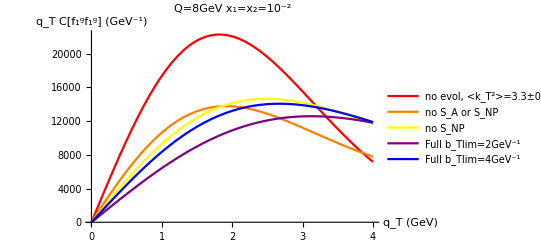
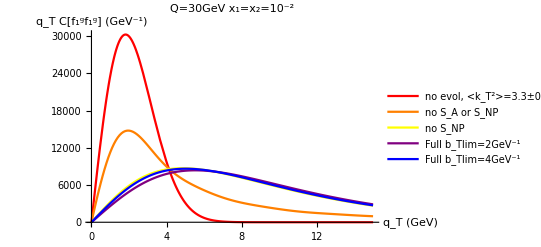

```mathematica
{Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,8],{qt,0,4},PlotStyle->Red,PlotLegends->{"no evol, <k_T^2>=3.3±0.8 GeV^2"}],ListPlot[{qtCf1f1NoSQ8,qtCf1f1NoSnpQ8,qtCf1f1bt2Q8,qtCf1f1bt4Q8},Joined->True,PlotStyle->{Orange,Yellow,Purple,Blue},PlotLegends->{"no S_A or S_NP","no S_NP","Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],

Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,30],{qt,0,15},PlotStyle->Red,PlotLegends->{"no evol, <k_T^2>=3.3±0.8 GeV^2"}],ListPlot[{qtCf1f1NoSQ30,qtCf1f1NoSnpQ30,qtCf1f1bt2Q30,qtCf1f1bt4Q30},Joined->True,PlotStyle->{Orange,Yellow,Purple,Blue},PlotLegends->{"no S_A or S_NP","no S_NP","Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

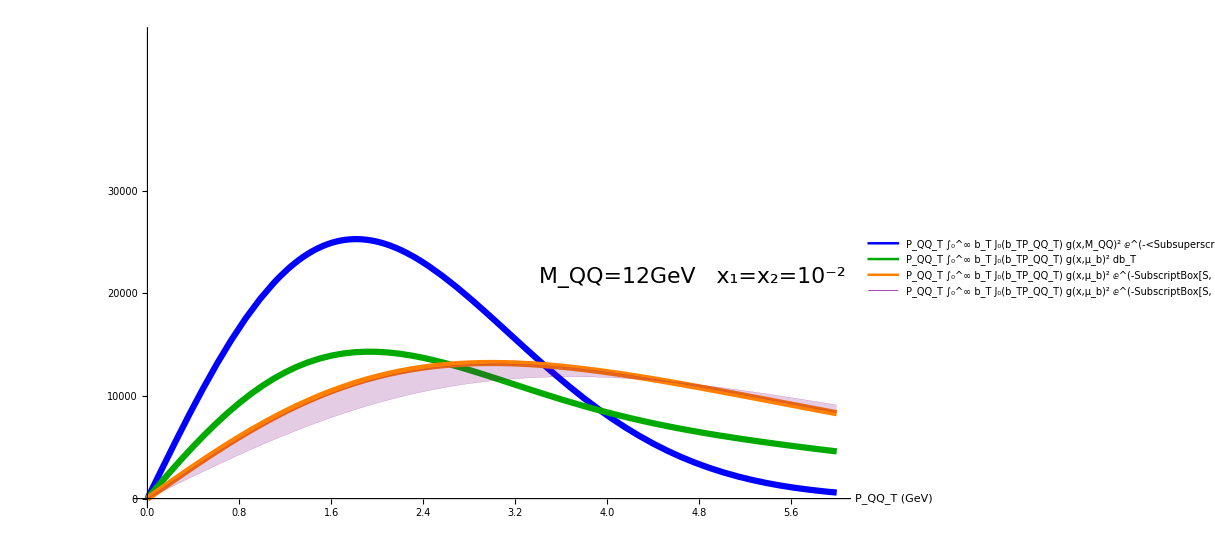

```mathematica
Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,12],{qt,0,6},PlotStyle->{Blue,Thickness[0.005]},PlotLegends->Placed[{Style["P_QQ_T ∫_0^∞ b_T J_0(b_TP_QQ_T) g(x,M_QQ)^2 ⅇ^(-<SubsuperscriptBox[k, T, 2]>SubsuperscriptBox[b, T, 2]/4) db_T",20]},{0.53,0.965}]],ListPlot[qtCf1f1NoSQ12,Joined->True,PlotStyle->{Darker[Green],Thickness[0.005]},PlotLegends->Placed[{Style["P_QQ_T ∫_0^∞ b_T J_0(b_TP_QQ_T) g(x,μ_b)^2 db_T",20]},{0.46,0.865}]],ListPlot[qtCf1f1NoSnpQ12,Joined->True,PlotStyle->{Orange,Thickness[0.005]},PlotLegends->Placed[{Style["P_QQ_T ∫_0^∞ b_T J_0(b_TP_QQ_T) g(x,μ_b)^2 ⅇ^(-SubscriptBox[S, A]) db_T",20]},{0.49,0.765}]],ListPlot[{qtCf1f1bt2Q12,qtCf1f1bt8Q12},Filling->{1->{2}},Joined->True,PlotStyle->{{Purple,Thickness[0]},{Purple,Thickness[0]}},PlotLegends->Placed[{Style["P_QQ_T ∫_0^∞ b_T J_0(b_TP_QQ_T) g(x,μ_b)^2 ⅇ^(-SubscriptBox[S, A] - SubscriptBox[S, NP]) db_T",20]},{0.51,0.665}]],AxesLabel->{Style["P_QQ_T (GeV)",18],},Epilog->Text[Style["M_QQ=12GeV   x_1=x_2=10^-2",22],Scaled[{.78,.48}]],TicksStyle->Large,PlotRange->{0,45000},Ticks->{Automatic,{0,10000,20000,30000}}]
```

```mathematica
qtCf1f1GaussQ12=Transpose[{qtvalsQ12,Map[qtCf1f1GausPlot[#,3.3,10^-2,12]&,qtvalsQ12]}];
```

```mathematica
Export["qtCf1f1NoSQ12.dat",qtCf1f1NoSQ12];
Export["qtCf1f1NoSnpQ12.dat",qtCf1f1NoSnpQ12];
Export["qtCf1f1bt2Q12.dat",qtCf1f1bt2Q12];
Export["qtCf1f1bt8Q12.dat",qtCf1f1bt8Q12];
Export["qtCf1f1GaussQ12.dat",qtCf1f1GaussQ12];
```

```mathematica
qtCf1f1Norm[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=(qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}])/NIntegrate[1/2 Q BesselJ[1,(bt Q)/2] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1Normbt4Q12x1=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1Norm[10^-1,12,#,0.16]&,qtvalsQ12]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 42.7329 and 0.0000650262 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {43.1986}. NIntegrate obtained 9.135×10^-321 and 0. for the integral and error estimates.

```mathematica
qtCf1f1Normbt4Q12x2=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1Norm[10^-2,12,#,0.16]&,qtvalsQ12]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.24168}. NIntegrate obtained 44118.7 and 0.210243 for the integral and error estimates.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {42.7106174329429847205154280320726911668316461145877838134765625}. NIntegrate obtained 4.07609×10^-317 and 5.4×10^-323 for the integral and error estimates.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 44200.3 and 0.105465 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {43.1986}. NIntegrate obtained 5.8003×10^-320 and 0. for the integral and error estimates.

```mathematica
qtCf1f1Normbt4Q12x3=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1Norm[10^-3,12,#,0.16]&,qtvalsQ12]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.24168}. NIntegrate obtained 2.99487×10^7 and 114.811 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 2.99832×10^7 and 118.102 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {42.9250699107892}. NIntegrate obtained 1.01446×10^-319 and 7.×10^-323 for the integral and error estimates.

```mathematica
qtCf1f1Normbt4Q12x4=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1Norm[10^-4,12,#,0.16]&,qtvalsQ12]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.225816}. NIntegrate obtained 1.73081×10^10 and 20136.6 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.24168}. NIntegrate obtained 1.74852×10^10 and 85555.8 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 1.75019×10^10 and 75443.9 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {43.0711}. NIntegrate obtained 1.18122×10^-314 and 2.07166×10^-318 for the integral and error estimates.

```mathematica
qtCf1f1Normbt4Q30x1=Transpose[{qtvalsQ30,ParallelMap[qtCf1f1Norm[10^-1,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.283381}. NIntegrate obtained 11.1673 and 0.000189594 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {36.420802293599708149458848982504832747508771717548370361328125}. NIntegrate obtained -5.15046×10^-318 and 4.×10^-323 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {36.7301}. NIntegrate obtained 2.42823×10^-319 and 0. for the integral and error estimates.

```mathematica
qtCf1f1Normbt4Q30x2=Transpose[{qtvalsQ30,ParallelMap[qtCf1f1Norm[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.283381}. NIntegrate obtained 19690.5 and 0.298801 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {36.51537343990466487342327894793925224803388118743896484375}. NIntegrate obtained 1.54173×10^-318 and 2.×10^-323 for the integral and error estimates.

```mathematica
qtCf1f1Normbt4Q30x3=Transpose[{qtvalsQ30,ParallelMap[qtCf1f1Norm[10^-3,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.252562}. NIntegrate obtained 1.7265×10^7 and 53.5808 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {36.50045204115721316656152650725886132931918837130069732666015625}. NIntegrate obtained 2.70113×10^-318 and 5.4×10^-323 for the integral and error estimates.

```mathematica
qtCf1f1Normbt4Q30x4=Transpose[{qtvalsQ30,ParallelMap[qtCf1f1Norm[10^-4,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.283381}. NIntegrate obtained 1.17942×10^10 and 201334. for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {36.8410107538916}. NIntegrate obtained -3.2995×10^-319 and 2.17×10^-322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {36.7481}. NIntegrate obtained 3.14036×10^-313 and 2.07333×10^-318 for the integral and error estimates.

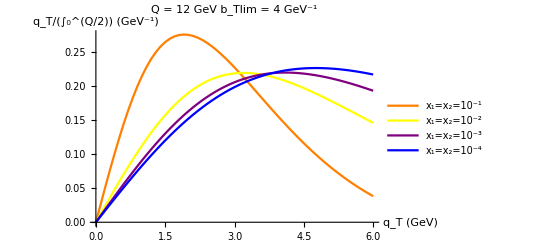

```mathematica
ListPlot[{qtCf1f1Normbt4Q12x1,qtCf1f1Normbt4Q12x2,qtCf1f1Normbt4Q12x3,qtCf1f1Normbt4Q12x4},Joined->True,PlotStyle->{Orange,Yellow,Purple,Blue},PlotLegends->{"x_1=x_2=10^-1","x_1=x_2=10^-2","x_1=x_2=10^-3","x_1=x_2=10^-4"},AxesLabel->{"q_T (GeV)","q_T/(∫_0^(Q/2)) (GeV^-1)"},PlotLabel->"Q = 12 GeV  b_Tlim = 4 GeV^-1"]
```

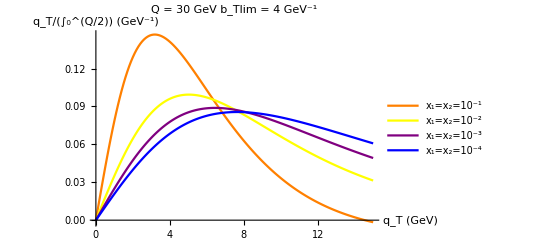

```mathematica
ListPlot[{qtCf1f1Normbt4Q30x1,qtCf1f1Normbt4Q30x2,qtCf1f1Normbt4Q30x3,qtCf1f1Normbt4Q30x4},Joined->True,PlotStyle->{Orange,Yellow,Purple,Blue},PlotLegends->{"x_1=x_2=10^-1","x_1=x_2=10^-2","x_1=x_2=10^-3","x_1=x_2=10^-4"},AxesLabel->{"q_T (GeV)","q_T/(∫_0^(Q/2)) (GeV^-1)"},PlotLabel->"Q = 30 GeV  b_Tlim = 4 GeV^-1"]
```

```mathematica
qtCf1f1Normx1x2[x1_?NumericQ,x2_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=(qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])gMSTW[x1,μbar[bt,Q]]gMSTW[x2,μbar[bt,Q]],{bt,0,∞}])/NIntegrate[1/2 Q BesselJ[1,(bt Q)/2] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])gMSTW[x1,μbar[bt,Q]]gMSTW[x2,μbar[bt,Q]],{bt,0,∞}];
```

```mathematica
qtCf1f1Normbt4Q12x23=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1Normx1x2[10^-2,10^-3,12,#,0.16]&,qtvalsQ12]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.24168}. NIntegrate obtained 1.12919×10^6 and 4.29433 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 1.13082×10^6 and 3.47092 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {42.9315647099542}. NIntegrate obtained 7.669×10^-320 and 7.×10^-323 for the integral and error estimates.

```mathematica
qtCf1f1Normbt4Q12x24=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1Normx1x2[10^-2,10^-4,12,#,0.16]&,qtvalsQ12]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.24168}. NIntegrate obtained 2.67456×10^7 and 128.176 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 2.67812×10^7 and 79.4081 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {43.0711}. NIntegrate obtained 2.61695×10^-317 and 4.94×10^-321 for the integral and error estimates.

```mathematica
qtCf1f1Normbt4Q12x34=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1Normx1x2[10^-3,10^-4,12,#,0.16]&,qtvalsQ12]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.24168}. NIntegrate obtained 7.20338×10^8 and 4285.58 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 7.21094×10^8 and 2730.58 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {43.0711}. NIntegrate obtained 3.46188×10^-317 and 6.08×10^-321 for the integral and error estimates.

```mathematica
qtCf1f1Normbt4Q12x12=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1Normx1x2[10^-1,10^-2,12,#,0.16]&,qtvalsQ12]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.24168}. NIntegrate obtained 1255. and 0.00597835 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {42.99161581061161142847115712584127322770655155181884765625}. NIntegrate obtained 2.299×10^-320 and 3.×10^-323 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 1258.71 and 0.00223865 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
qtCf1f1Normbt4Q12x13=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1Normx1x2[10^-1,10^-3,12,#,0.16]&,qtvalsQ12]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {43.0261295690557321325098172337675350718200206756591796875}. NIntegrate obtained 3.0434×10^-320 and 2.5×10^-323 for the integral and error estimates.

```mathematica
qtCf1f1Normbt4Q12x14=Transpose[{qtvalsQ12,ParallelMap[qtCf1f1Normx1x2[10^-1,10^-4,12,#,0.16]&,qtvalsQ12]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.24168}. NIntegrate obtained 688965. and 2.54681 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 690436. and 1.38969 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {43.0711}. NIntegrate obtained 1.03897×10^-317 and 1.85×10^-321 for the integral and error estimates.

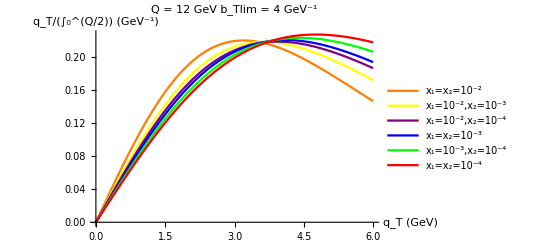

```mathematica
ListPlot[{qtCf1f1Normbt4Q12x2,qtCf1f1Normbt4Q12x23,qtCf1f1Normbt4Q12x24,qtCf1f1Normbt4Q12x3,qtCf1f1Normbt4Q12x34,qtCf1f1Normbt4Q12x4},Joined->True,PlotStyle->{Orange,Yellow,Purple,Blue,Green,Red},PlotLegends->{"x_1=x_2=10^-2","x_1=10^-2,x_2=10^-3","x_1=10^-2,x_2=10^-4","x_1=x_2=10^-3","x_1=10^-3,x_2=10^-4","x_1=x_2=10^-4"},AxesLabel->{"q_T (GeV)","q_T/(∫_0^(Q/2)) (GeV^-1)"},PlotLabel->"Q = 12 GeV  b_Tlim = 4 GeV^-1"]
```

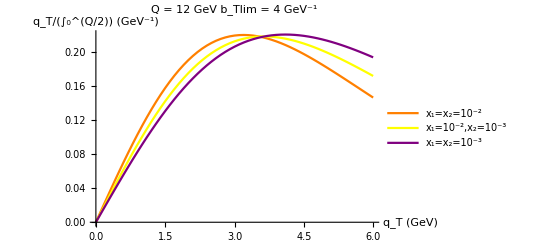

```mathematica
ListPlot[{qtCf1f1Normbt4Q12x2,qtCf1f1Normbt4Q12x23,qtCf1f1Normbt4Q12x3},Joined->True,PlotStyle->{Orange,Yellow,Purple,Blue,Green,Red},PlotLegends->{"x_1=x_2=10^-2","x_1=10^-2,x_2=10^-3","x_1=x_2=10^-3"},AxesLabel->{"q_T (GeV)","q_T/(∫_0^(Q/2)) (GeV^-1)"},PlotLabel->"Q = 12 GeV  b_Tlim = 4 GeV^-1"]
```

```mathematica
Export["x22.dat",qtCf1f1Normbt4Q12x2];
Export["x23.dat",qtCf1f1Normbt4Q12x23];
Export["x33.dat",qtCf1f1Normbt4Q12x3];
```

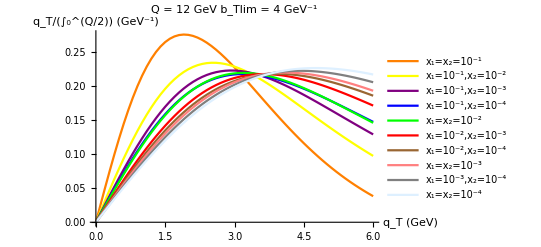

```mathematica
ListPlot[{qtCf1f1Normbt4Q12x1,qtCf1f1Normbt4Q12x12,qtCf1f1Normbt4Q12x13,qtCf1f1Normbt4Q12x14,qtCf1f1Normbt4Q12x2,qtCf1f1Normbt4Q12x23,qtCf1f1Normbt4Q12x24,qtCf1f1Normbt4Q12x3,qtCf1f1Normbt4Q12x34,qtCf1f1Normbt4Q12x4},Joined->True,PlotStyle->{Orange,Yellow,Purple,Blue,Green,Red,Brown,Pink,Gray,LightBlue},PlotLegends->{"x_1=x_2=10^-1","x_1=10^-1,x_2=10^-2","x_1=10^-1,x_2=10^-3","x_1=10^-1,x_2=10^-4","x_1=x_2=10^-2","x_1=10^-2,x_2=10^-3","x_1=10^-2,x_2=10^-4","x_1=x_2=10^-3","x_1=10^-3,x_2=10^-4","x_1=x_2=10^-4"},AxesLabel->{"q_T (GeV)","q_T/(∫_0^(Q/2)) (GeV^-1)"},PlotLabel->"Q = 12 GeV  b_Tlim = 4 GeV^-1"]
```

The perturbative expressions used for f_1^g and h_1^(⊥g) as well as the perturbative Sudakov factor S_A are given at leading order in α_s. The corrections to these expressions are one order higher in α_s. They are kept reasonably small by keeping α_s small even at large b_T (indeed α_s(b_0/b_T) becomes larger than 1 for b_T>2.5 GeV^-1), using the b_T^*-prescription: b_T→ b_T^*<b_Tmax. Therefore at distances smaller than b_Tmax, α_s is considered small enough for the leading order expressions to be valid. Beyond this limit, the nonperturbative Sudakov factor is supposed to take over. This means that the action of S_NP on the b_T-integrand should not be too strong in the perturbative region. Therefore one cannot take a too narrow e^-S_NP regarding the value of b_Tmax.

```mathematica
btbartune[bt_,Q_,btmax_]:=√((bt^2+(b0/Q)^2)/(1+(bt/btmax)^2+(b0/(Q btmax))^2));
```

```mathematica
μbartune[bt_,Q_,btmax_]:=b0/btbartune[bt,Q,btmax];
```

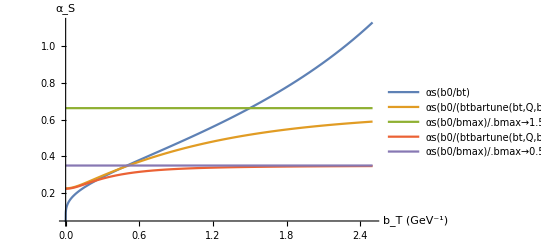

```mathematica
Plot[{αs[b0/bt],αs[b0/btbartune[bt,Q,bmax]]/.bmax->1.5/.Q->8,αs[b0/bmax]/.bmax->1.5/.Q->8,αs[b0/btbartune[bt,Q,bmax]]/.bmax->0.5/.Q->8,αs[b0/bmax]/.bmax->0.5/.Q->8},{bt,0,2.5},PlotRange->All,AxesLabel->{"b_T (GeV^-1)","α_S"},PlotLegends->"Expressions"]
```

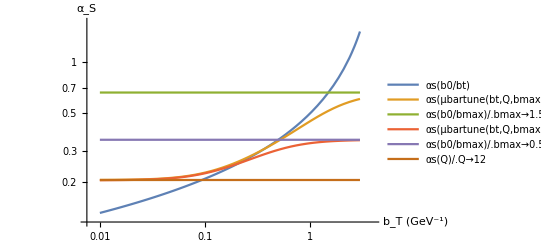

```mathematica
LogLogPlot[{αs[b0/bt],αs[μbartune[bt,Q,bmax]]/.Q->12/.bmax->1.5,αs[b0/bmax]/.bmax->1.5,αs[μbartune[bt,Q,bmax]]/.Q->12/.bmax->0.5,αs[b0/bmax]/.bmax->0.5,αs[Q]/.Q->12},{bt,10^-2,3},PlotRange->All,AxesLabel->{"b_T (GeV^-1)","α_S"},PlotLegends->"Expressions"]
```

We see that the fitted parametrisation on quark data by Aybat-Rogers already has a very strong suppression effect at b_Tmax=1.5 GeV^-1 that was considered for the fit, same for S_NPtune with b_Tlim=2 GeV^-1.

```mathematica
ⅇ^(-Snptune[btmax,8,0.64])
```

0.0487711

```mathematica
ⅇ^(-Snptune[btmax,30,0.64])
```

0.00744082

```mathematica
ⅇ^(-Snptune[btmax,8,0.04])
```

0.827962

```mathematica
ⅇ^(-Snptune[btmax,30,0.04])
```

0.736167

```mathematica
SnpAR[bt_,Q_,x2_]:=9/4(0.184Log[Q/(2(1.6))]+0.201(1+2(-0.129)Log[(0.09x2)/(0.009+x2)]))bt^2;
```

```mathematica
ⅇ^(-SnpAR[btmax,8,0.09])
```

0.079797

```mathematica
ⅇ^(-SnpAR[btmax,30,0.09])
```

0.0232957

## q_T-spectrum with uncertainty bands

Computing and plotting  q_T C[f_1^g f_1^g] for Gaussian f_1^gwith <k_T^2> =3.3±0.8 GeV^2 (red curve with grey uncertainty bands), and for evolved f_1^g using S_NP with b_Tlim ∈ [2;8] GeV^-1 (blue band)
We also compute the uncertainty band when varying the scale μ ∈ [ 1/2 ; 2 ] x μbar (brown band) ; but this variation is not independent to other variations such as the S_NP one, so there is no point trying to estimate the total uncertainty as the parameters are too unconstrained due to the lack of data

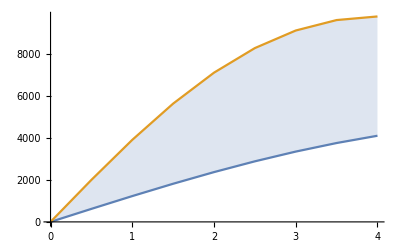
{(0. | 0.
0.5 | 619.106
1. | 1227.08
1.5 | 1813.07
2. | 2366.91
2.5 | 2879.37
3. | 3342.41
3.5 | 3749.39
4. | 4095.21),(0. | 0.
0.5 | 1996.74
1. | 3899.64
1.5 | 5622.63
2. | 7094.2
2.5 | 8262.49
3. | 9098.11
3.5 | 9594.54
4. | 9766.23),-Graphics-}

```mathematica
qtlist=Range[0,4,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlistbtQ8=ParallelMap[{qtlist[[#]],Min[Table[qtCf1f1tunebt[10^-2,8,qtlist[[#]],A],{A,Alist}]]}&,Range[Length[qtlist]]]],MatrixForm[maxlistbtQ8=ParallelMap[{qtlist[[#]],Max[Table[qtCf1f1tunebt[10^-2,8,qtlist[[#]],A],{A,Alist}]]}&,Range[Length[qtlist]]]],ListPlot[{minlistbtQ8,maxlistbtQ8},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

!!! WATCH OUT: using the method with Interval[ ] replaces R2 in the Min[ ] (or Max[ ]) function by the interval and not a fixed value, allowing it to try different values for each occurrence of the same argument inside the tested function when searching for the minimum (or maximum). Such a method is therefore doing wrong when the same argument appears several times in the definition of the fuction, allowing for much more possibilities than there are in reality.

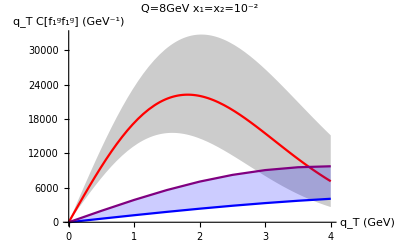

```mathematica
Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,8]],qtCf1f1GausPlot[qt,3.3,10^-2,8],Max[qtCf1f1GausPlot[qt,R2,10^-2,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ8,maxlistbtQ8},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.238476}. NIntegrate obtained 10518.8 and 0.0322554 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.238476}. NIntegrate obtained 9220.98 and 0.0320067 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.238476}. NIntegrate obtained 8173.68 and 0.0295851 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.238476}. NIntegrate obtained 10518.8 and 0.0322554 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.238476}. NIntegrate obtained 9220.98 and 0.0320067 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.238476}. NIntegrate obtained 8173.68 and 0.0295851 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

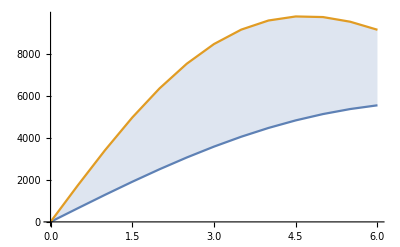
{(0. | 0.
0.5 | 650.441
1. | 1291.66
1.5 | 1914.67
2. | 2510.89
2.5 | 3072.39
3. | 3592.01
3.5 | 4063.58
4. | 4481.97
4.5 | 4843.23
5. | 5144.59
5.5 | 5384.52
6. | 5562.67),(0. | 0.
0.5 | 1741.47
1. | 3420.77
1.5 | 4979.78
2. | 6368.05
2.5 | 7545.76
3. | 8485.57
3.5 | 9173.45
4. | 9608.4
4.5 | 9801.2
5. | 9772.33
5.5 | 9549.62
6. | 9165.44),-Graphics-}

```mathematica
qtlist=Range[0,6,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlistbtQ12=ParallelMap[{qtlist[[#]],Min[Table[qtCf1f1tunebt[10^-2,12,qtlist[[#]],A],{A,Alist}]]}&,Range[Length[qtlist]]]],MatrixForm[maxlistbtQ12=ParallelMap[{qtlist[[#]],Max[Table[qtCf1f1tunebt[10^-2,12,qtlist[[#]],A],{A,Alist}]]}&,Range[Length[qtlist]]]],ListPlot[{minlistbtQ12,maxlistbtQ12},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

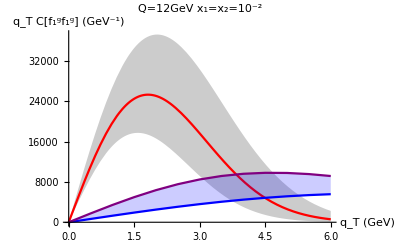

```mathematica
Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ12,maxlistbtQ12},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"]
```

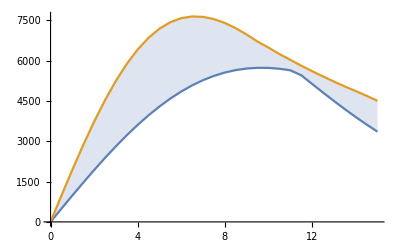
{(0. | 0.
0.5 | 492.611
1. | 981.135
1.5 | 1461.54
2. | 1929.92
2.5 | 2382.55
3. | 2815.92
3.5 | 3226.82
4. | 3612.34
4.5 | 3969.93
5. | 4297.43
5.5 | 4593.09
6. | 4855.55
6.5 | 5083.91
7. | 5277.65
7.5 | 5436.66
8. | 5561.25
8.5 | 5652.06
9. | 5710.08
9.5 | 5736.61
10. | 5733.2
10.5 | 5701.65
11. | 5643.93
11.5 | 5461.17
12. | 5136.85
12.5 | 4816.42
13. | 4502.97
13.5 | 4198.96
14. | 3906.21
14.5 | 3626.02
15. | 3359.25),(0. | 0.
0.5 | 978.537
1. | 1938.28
1.5 | 2861.17
2. | 3730.56
2.5 | 4531.87
3. | 5253.01
3.5 | 5884.72
4. | 6420.69
4.5 | 6857.92
5. | 7195.89
5.5 | 7436.97
6. | 7585.74
6.5 | 7648.66
7. | 7633.57
7.5 | 7549.27
8. | 7405.08
8.5 | 7210.47
9. | 6974.7
9.5 | 6711.73
10. | 6490.43
10.5 | 6247.78
11. | 6035.38
11.5 | 5817.27
12. | 5611.7
12.5 | 5416.78
13. | 5225.13
13.5 | 5043.23
14. | 4872.28
14.5 | 4694.11
15. | 4507.77),-Graphics-}

```mathematica
qtlist=Range[0,15,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlistbtQ30=ParallelMap[{qtlist[[#]],Min[Table[qtCf1f1tunebt[10^-2,30,qtlist[[#]],A],{A,Alist}]]}&,Range[Length[qtlist]]]],MatrixForm[maxlistbtQ30=ParallelMap[{qtlist[[#]],Max[Table[qtCf1f1tunebt[10^-2,30,qtlist[[#]],A],{A,Alist}]]}&,Range[Length[qtlist]]]],ListPlot[{minlistbtQ30,maxlistbtQ30},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

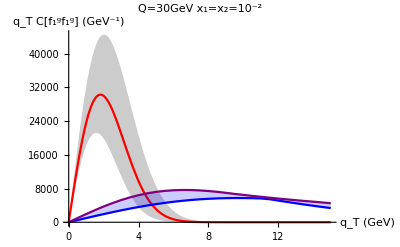

```mathematica
Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ30,maxlistbtQ30},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]
```

## Normalised q_T-spectrum : evol VS. non-evol VS. LHCb data at Q=8GeV !!! A SHOULD BE ∈[0.04 ; 0.64] AND NOT [2;8] WHICH b_tmax VALUES

```mathematica
qtCf1f1Norm[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=(qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}])/NIntegrate[1/2 Q BesselJ[1,(bt Q)/2] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1NormnoSnp[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=(qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}])/NIntegrate[1/2 Q BesselJ[1,(bt Q)/2] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1GausNorm[qt_,R2_,Q_]:=-(ⅇ^(-qt^2/(2 R2)) qt)/((-1+ⅇ^(-Q^2/(8 R2))) R2);
```

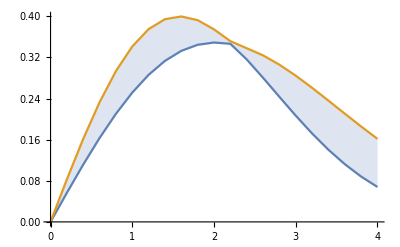
{(0. | 0.
0.2 | 0.0565837
0.4 | 0.111523
0.6 | 0.163254
0.8 | 0.210365
1. | 0.251662
1.2 | 0.286217
1.4 | 0.313401
1.6 | 0.332901
1.8 | 0.344709
2. | 0.349107
2.2 | 0.346627
2.4 | 0.316255
2.6 | 0.280505
2.8 | 0.243399
3. | 0.206788
3.2 | 0.172127
3.4 | 0.140451
3.6 | 0.112394
3.8 | 0.0882419
4. | 0.067991),(0. | 0.
0.2 | 0.082735
0.4 | 0.161546
0.6 | 0.232818
0.8 | 0.293518
1. | 0.341409
1.2 | 0.375179
1.4 | 0.394474
1.6 | 0.399848
1.8 | 0.39263
2. | 0.374738
2.2 | 0.351774
2.4 | 0.338007
2.6 | 0.324134
2.8 | 0.305992
3. | 0.284601
3.2 | 0.26097
3.4 | 0.236053
3.6 | 0.21071
3.8 | 0.185687
4. | 0.161598),-Graphics-}

```mathematica
qtlist=Range[0,4,0.2];
R2list=Range[2.5,4.1,0.01];
Tabltg=Map[Table[qtCf1f1GausNorm[#,R2,8],{R2,R2list}]&,qtlist];
{MatrixForm[mintgQ8=Map[{qtlist[[#]],Min[Tabltg[[#]]]}&,Range[Length[qtlist]]]],MatrixForm[maxtgQ8=Map[{qtlist[[#]],Max[Tabltg[[#]]]}&,Range[Length[qtlist]]]],ListPlot[{mintgQ8,maxtgQ8},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

```mathematica
qtlist=Range[0,4,0.2];
Alist=Range[0.04,0.64,0.1];
Tabl8=ParallelMap[Table[qtCf1f1Norm[10^-2,8,#,A],{A,Alist}]&,qtlist];
```

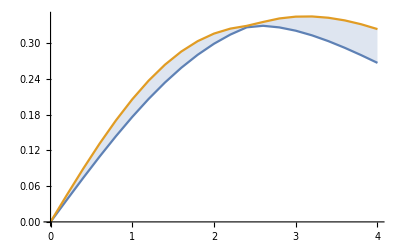
{(0. | 0.
0.2 | 0.0371478
0.4 | 0.0737982
0.6 | 0.109466
0.8 | 0.143692
1. | 0.176053
1.2 | 0.206174
1.4 | 0.233732
1.6 | 0.258468
1.8 | 0.280186
2. | 0.298755
2.2 | 0.31411
2.4 | 0.32625
2.6 | 0.328839
2.8 | 0.326119
3. | 0.320611
3.2 | 0.31278
3.4 | 0.303072
3.6 | 0.291904
3.8 | 0.279654
4. | 0.26665),(0. | 0.
0.2 | 0.0451855
0.4 | 0.0892465
0.6 | 0.131187
0.8 | 0.170187
1. | 0.205581
1.2 | 0.236849
1.4 | 0.263626
1.6 | 0.285711
1.8 | 0.30306
2. | 0.315777
2.2 | 0.324084
2.4 | 0.328709
2.6 | 0.335228
2.8 | 0.341152
3. | 0.344176
3.2 | 0.344489
3.4 | 0.342309
3.6 | 0.337877
3.8 | 0.331446
4. | 0.323275),-Graphics-}

```mathematica
{MatrixForm[minlistbtNormQ8=Map[{qtlist[[#]],Min[Tabl8[[#]]]}&,Range[Length[qtlist]]]],MatrixForm[maxlistbtNormQ8=Map[{qtlist[[#]],Max[Tabl8[[#]]]}&,Range[Length[qtlist]]]],ListPlot[{minlistbtNormQ8,maxlistbtNormQ8},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
LHCb13datNODPSPlot4=({{{0.5,0.20153314163536068}, ErrorBar[0.5,0.07264702241987869]}, {{1.5,0.28638454718535394}, ErrorBar[0.5,0.09971493099591708]}, {{2.5,0.28588343844213565}, ErrorBar[0.5,0.11058447437610346]}, {{3.5,0.22619887273714984}, ErrorBar[0.5,0.08949827380291174]}, {{4.5,0.17368752642040558}, ErrorBar[0.5,0.07678015530360593]}, {{5.5,0.09273362664484106}, ErrorBar[0.5,0.05181906106834104]}, {{6.5,0.10962524347918191}, ErrorBar[0.5,0.042881199279617664]}, {{7.5,0.060524634528971465}, ErrorBar[0.5,0.03721473022552986]}});
```

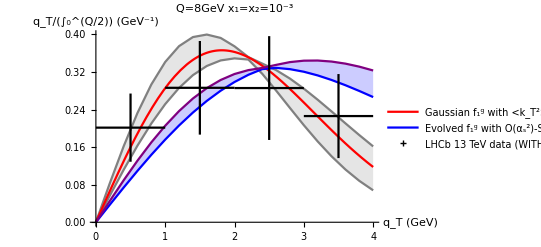

```mathematica
Show[
      ListPlot[{mintgQ8,maxtgQ8},Filling->{1->{2}},Joined->True,FillingStyle->Darker,PlotStyle->{Gray,Gray}],

Plot[qtCf1f1GausNorm[qt,3.3,8],{qt,0,4},PlotLegends->{"Gaussian f_1^g with <k_T^2>=3.3±0.8 GeV^2"},PlotStyle->Red],

         ListPlot[{minlistbtNormQ8,maxlistbtNormQ8},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple},PlotLegends->{"Evolved f_1^g with O(α_s^2)-S_A(btbar), gMSTW(btbar), bc(bt) in S_NP with b_Tlim ∈ [2;8] GeV^-1"}],

         ErrorListPlot[LHCb13datNODPSPlot4[[1;;4]],PlotMarkers->"+",PlotStyle->Black,PlotLegends->{"LHCb 13 TeV data (WITHOUT DPS) normalised over region q_T<Q/2"}],
      AxesLabel->{"q_T (GeV)","q_T/(∫_0^(Q/2)) (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-3",PlotRange->All]
```

```mathematica
qtlist=Range[0,4,0.2];
Tabl8noSnp=ParallelMap[{#,qtCf1f1NormnoSnp[10^-2,8,#]}&,qtlist];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {8.16907×10^224}. NIntegrate obtained 8.21927639100886×10^55895 and 8.21927639100886×10^55895 for the integral and error estimates.

```mathematica
Tabl8noSnp
```

{{0.,0.},{0.2,0.0462532},{0.4,0.0911186},{0.6,0.133715},{0.8,0.173188},{1.,0.208829},{1.2,0.240105},{1.4,0.266659},{1.6,0.288317},{1.8,0.305073},{2.,0.317069},{2.2,0.324572},{2.4,0.327954},{2.6,0.327645},{2.8,0.324124},{3.,0.317885},{3.2,0.309414},{3.4,0.299174},{3.6,0.287589},{3.8,0.275034},{4.,0.261836}}

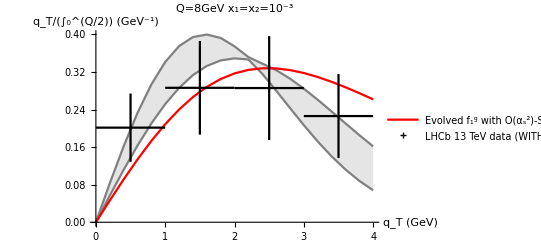

```mathematica
Show[
      ListPlot[{mintgQ8,maxtgQ8},Filling->{1->{2}},Joined->True,FillingStyle->Darker,PlotStyle->{Gray,Gray}],

 ListPlot[Tabl8noSnp,Joined->True,PlotStyle->Red,PlotLegends->{"Evolved f_1^g with O(α_s^2)-S_A(b_T^*(b_c(b_T))) and no S_NP"}],

         ErrorListPlot[LHCb13datNODPSPlot4[[1;;4]],PlotMarkers->"+",PlotStyle->Black,PlotLegends->{"LHCb 13 TeV data (WITHOUT DPS) normalised over region q_T<Q/2"}],
      AxesLabel->{"q_T (GeV)","q_T/(∫_0^(Q/2)) (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-3",PlotRange->All]
```

## x-dependence

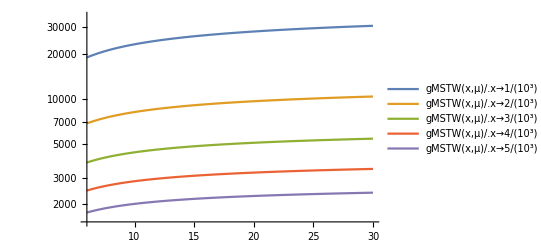
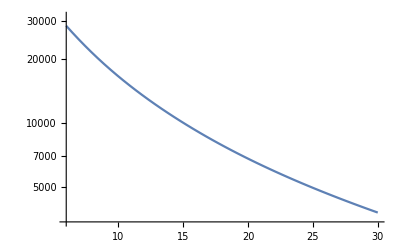
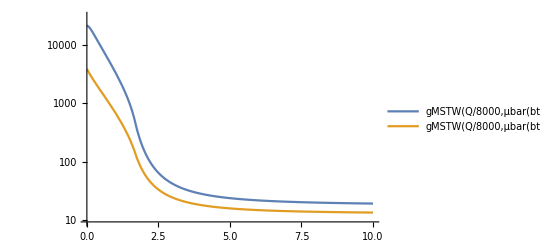

```mathematica
{LogPlot[{gMSTW[x,μ]/.x->10^-3,gMSTW[x,μ]/.x->2*10^-3,gMSTW[x,μ]/.x->3*10^-3,gMSTW[x,μ]/.x->4*10^-3,gMSTW[x,μ]/.x->5*10^-3},{μ,6,30},PlotLegends->"Expressions"],
LogPlot[gMSTW[Q/8000,Q],{Q,6,30},PlotLegends->"Expressions"],
LogPlot[{gMSTW[Q/8000,μbar[bt,Q]]/.Q->8,gMSTW[Q/8000,μbar[bt,Q]]/.Q->30},{bt,0,10},PlotLegends->"Expressions"]}
```

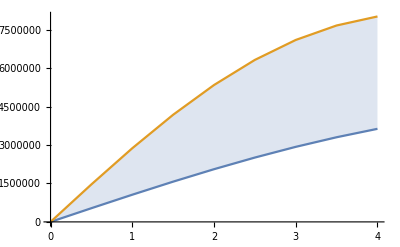
{(0. | 0.
0.5 | 534744.
1. | 1.06119×10^6
1.5 | 1.57128×10^6
2. | 2.05735×10^6
2.5 | 2.5124×10^6
3. | 2.9302×10^6
3.5 | 3.30524×10^6
4. | 3.63402×10^6),(0. | 0.
0.5 | 1.46454×10^6
1. | 2.87553×10^6
1.5 | 4.18308×10^6
2. | 5.34416×10^6
2.5 | 6.32522×10^6
3. | 7.10379×10^6
3.5 | 7.66909×10^6
4. | 8.02168×10^6),-Graphics-}

```mathematica
qtlist=Range[0,4,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlistbtQ8x=ParallelMap[{qtlist[[#]],Min[Table[qtCf1f1tunebt[8/8000,8,qtlist[[#]],A],{A,Alist}]]}&,Range[Length[qtlist]]]],MatrixForm[maxlistbtQ8x=ParallelMap[{qtlist[[#]],Max[Table[qtCf1f1tunebt[8/8000,8,qtlist[[#]],A],{A,Alist}]]}&,Range[Length[qtlist]]]],ListPlot[{minlistbtQ8x,maxlistbtQ8x},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

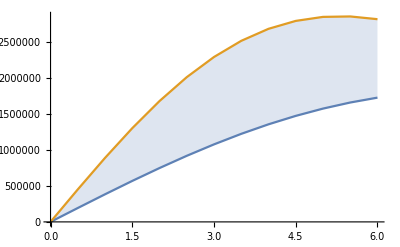
{(0. | 0.
0.5 | 192790.
1. | 383198.
1.5 | 568895.
2. | 747631.
2.5 | 917382.
3. | 1.07619×10^6
3.5 | 1.22242×10^6
4. | 1.35463×10^6
4.5 | 1.4717×10^6
5. | 1.57278×10^6
5.5 | 1.6573×10^6
6. | 1.72502×10^6),(0. | 0.
0.5 | 450642.
1. | 888365.
1.5 | 1.30096×10^6
2. | 1.67758×10^6
2.5 | 2.00927×10^6
3. | 2.28935×10^6
3.5 | 2.51361×10^6
4. | 2.68035×10^6
4.5 | 2.79024×10^6
5. | 2.84601×10^6
5.5 | 2.85208×10^6
6. | 2.81413×10^6),-Graphics-}

```mathematica
qtlist=Range[0,6,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlistbtQ12x=ParallelMap[{qtlist[[#]],Min[Table[qtCf1f1tunebt[12/8000,12,qtlist[[#]],A],{A,Alist}]]}&,Range[Length[qtlist]]]],MatrixForm[maxlistbtQ12x=ParallelMap[{qtlist[[#]],Max[Table[qtCf1f1tunebt[12/8000,12,qtlist[[#]],A],{A,Alist}]]}&,Range[Length[qtlist]]]],ListPlot[{minlistbtQ12x,maxlistbtQ12x},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

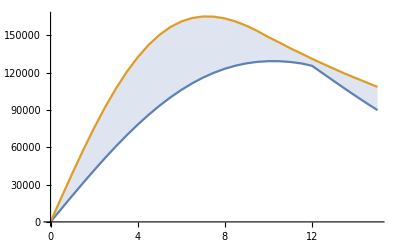
{(0. | 0.
0.5 | 10594.8
1. | 21109.1
1.5 | 31463.1
2. | 41579.7
2.5 | 51384.8
3. | 60808.8
3.5 | 69787.1
4. | 78261.3
4.5 | 86179.4
5. | 93496.9
5.5 | 100177.
6. | 106189.
6.5 | 111514.
7. | 116138.
7.5 | 120054.
8. | 123266.
8.5 | 125783.
9. | 127621.
9.5 | 128801.
10. | 129350.
10.5 | 129302.
11. | 128691.
11.5 | 127558.
12. | 125597.
12.5 | 119453.
13. | 113320.
13.5 | 107259.
14. | 101317.
14.5 | 95531.5
15. | 89932.1),(0. | 0.
0.5 | 19716.7
1. | 39100.3
1.5 | 57829.6
2. | 75606.4
2.5 | 92165.9
3. | 107284.
3.5 | 120782.
4. | 132535.
4.5 | 142464.
5. | 150544.
5.5 | 156792.
6. | 161270.
6.5 | 164070.
7. | 165316.
7.5 | 165148.
8. | 163722.
8.5 | 161200.
9. | 157745.
9.5 | 153514.
10. | 148659.
10.5 | 144345.
11. | 139740.
11.5 | 135562.
12. | 131207.
12.5 | 127234.
13. | 123269.
13.5 | 119359.
14. | 115753.
14.5 | 112202.
15. | 108630.),-Graphics-}

```mathematica
qtlist=Range[0,15,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlistbtQ30x=ParallelMap[{qtlist[[#]],Min[Table[qtCf1f1tunebt[30/8000,30,qtlist[[#]],A],{A,Alist}]]}&,Range[Length[qtlist]]]],MatrixForm[maxlistbtQ30x=ParallelMap[{qtlist[[#]],Max[Table[qtCf1f1tunebt[30/8000,30,qtlist[[#]],A],{A,Alist}]]}&,Range[Length[qtlist]]]],ListPlot[{minlistbtQ30x,maxlistbtQ30x},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

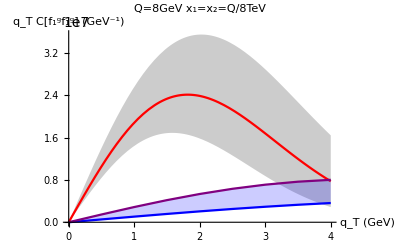
{-Graphics-,-Graphics-}

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,8]],qtCf1f1GausPlot[qt,3.3,10^-2,8],Max[qtCf1f1GausPlot[qt,R2,10^-2,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ8,maxlistbtQ8},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,8/8000,8]],qtCf1f1GausPlot[qt,3.3,8/8000,8],Max[qtCf1f1GausPlot[qt,R2,8/8000,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ8x,maxlistbtQ8x},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=Q/8TeV"]}
```

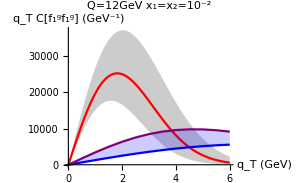
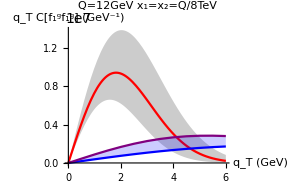

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ12,maxlistbtQ12},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,12/8000,12]],qtCf1f1GausPlot[qt,3.3,12/8000,12],Max[qtCf1f1GausPlot[qt,R2,12/8000,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ12x,maxlistbtQ12x},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=Q/8TeV"]}
```

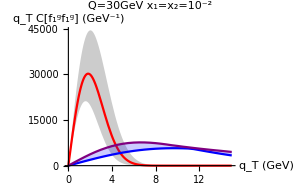
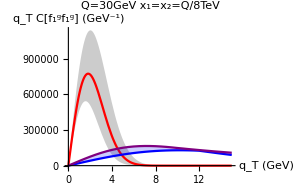

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ30,maxlistbtQ30},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,30/8000,30]],qtCf1f1GausPlot[qt,3.3,30/8000,30],Max[qtCf1f1GausPlot[qt,R2,30/8000,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ30x,maxlistbtQ30x},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=Q/8TeV"]}
```

## Description of the different contributions to the different convolutions

The first difference between the cos(2ϕ) and cos(4ϕ) convolutions is that they contain a different Bessel function than the azimuthally independent terms : J_2 and J_4 respectively, instead of J_0. While the former is 1 at b_T=0, the two latter are 0 at b_T=0. Moreover, at equal value of q_T, they are more stretched in b_T, and J_4 more than J_2.

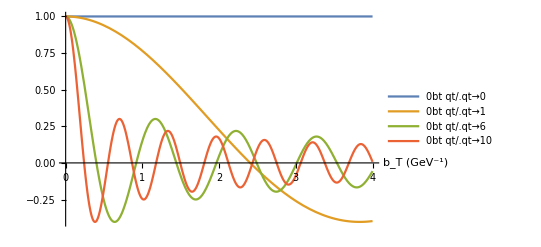
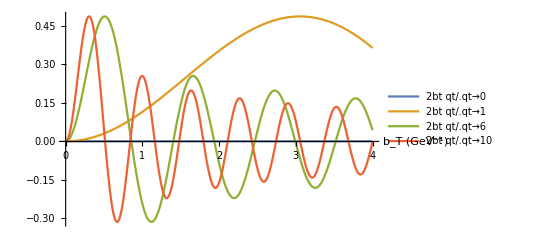
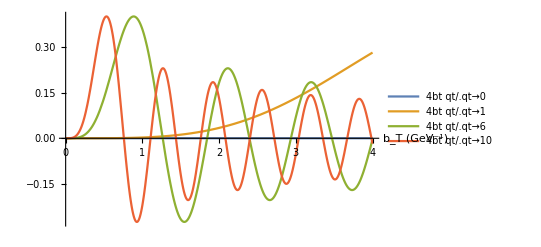
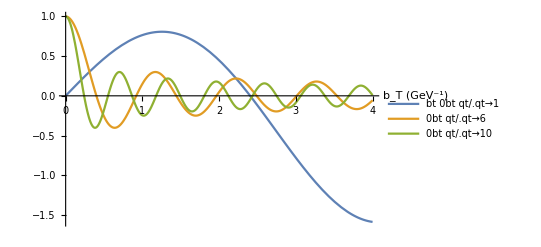
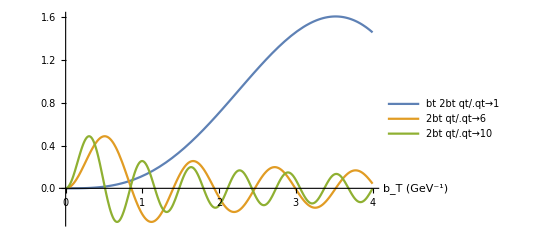
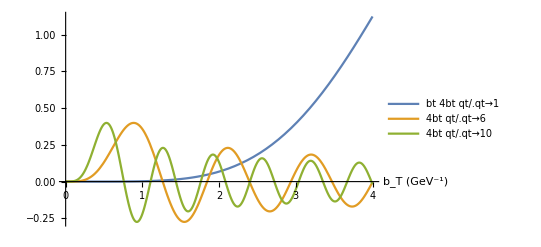

```mathematica
{Plot[{BesselJ[0,bt qt]/.qt->0,BesselJ[0,bt qt]/.qt->1,BesselJ[0,bt qt]/.qt->6,BesselJ[0,bt qt]/.qt->10},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],
Plot[{BesselJ[2,bt qt]/.qt->0,BesselJ[2,bt qt]/.qt->1,BesselJ[2,bt qt]/.qt->6,BesselJ[2,bt qt]/.qt->10},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],
Plot[{BesselJ[4,bt qt]/.qt->0,BesselJ[4,bt qt]/.qt->1,BesselJ[4,bt qt]/.qt->6,BesselJ[4,bt qt]/.qt->10},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],


Plot[{bt BesselJ[0,bt qt]/.qt->1,BesselJ[0,bt qt]/.qt->6,BesselJ[0,bt qt]/.qt->10},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],
Plot[{bt BesselJ[2,bt qt]/.qt->1,BesselJ[2,bt qt]/.qt->6,BesselJ[2,bt qt]/.qt->10},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],
Plot[{bt BesselJ[4,bt qt]/.qt->1,BesselJ[4,bt qt]/.qt->6,BesselJ[4,bt qt]/.qt->10},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

The other difference is that h_1^(⊥g) is not simply a collinear PDF, but a splitting function with the PDF as initial imput ; the action of the PDF is therefore modified. Moreover, it is proportional to α_s. It is naturally suppressed as α_s is small, but the running of α_s also adds a new dependence on the scale in the convolution. In C[w_0 h_1^(⊥g) h_1^(⊥g)] and C[w_4 h_1^(⊥g) h_1^(⊥g)], these effects are amplified as h_1^(⊥g) appears twice.

```mathematica
Cffint[x_,Q_,qt_,bt_]:=bt BesselJ[0,qt bt] gMSTW[x,Q]^2;
```

```mathematica
Chhint[x_,Q_,qt_,bt_]:=bt BesselJ[0,qt bt]((Nc αs[Q])/π)^2 NIntegrate[(1/x-1/y1)gMSTW[y1,Q](1/x-1/y2)gMSTW[y2,Q],{y1,x,1},{y2,x,1}];
```

```mathematica
Cw3fhint[x_,Q_,qt_,bt_]:=bt BesselJ[2,qt bt]((Nc αs[Q])/π)NIntegrate[gMSTW[x,Q](1/x-1/y2)gMSTW[y2,Q],{y2,x,1}];
```

```mathematica
Cw4hhint[x_,Q_,qt_,bt_]:=bt BesselJ[4,qt bt]((Nc αs[Q])/π)^2 NIntegrate[(1/x-1/y1)gMSTW[y1,Q](1/x-1/y2)gMSTW[y2,Q],{y1,x,1},{y2,x,1}];
```

```mathematica
Chhqt3=Transpose[{Range[0,4,0.05],ParallelMap[Chhint[10^-2,8,3,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Chhqt10=Transpose[{Range[0,4,0.05],ParallelMap[Chhint[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Cw3fhqt3=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint[10^-2,8,3,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fhqt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw4hhqt3=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint[10^-2,8,3,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Cw4hhqt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Cffqt3ev=Transpose[{Range[0,4,0.05],ParallelMap[NIntegrate[Cffint[10^-2,8,3,bt],{bt,0,#}] &,Range[0,4,0.05]]}];
```

```mathematica
Cffqt10ev=Transpose[{Range[0,4,0.05],ParallelMap[NIntegrate[Cffint[10^-2,8,10,bt],{bt,0,#}] &,Range[0,4,0.05]]}];
```

```mathematica
Chhqt3ev=Transpose[{Range[0,4,0.05],ParallelMap[NIntegrate[Chhint[10^-2,8,3,bt],{bt,0,#}] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Chhqt10ev=Transpose[{Range[0,4,0.05],ParallelMap[NIntegrate[Chhint[10^-2,8,10,bt],{bt,0,#}] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Cw3fhqt3ev=Transpose[{Range[0,4,0.1],ParallelMap[NIntegrate[Cw3fhint[10^-2,8,3,bt],{bt,0,#}] &,Range[0,4,0.1]]}];
```

```mathematica
Cw3fhqt10ev=Transpose[{Range[0,4,0.1],ParallelMap[NIntegrate[Cw3fhint[10^-2,8,10,bt],{bt,0,#}] &,Range[0,4,0.1]]}];
```

```mathematica
Cw4hhqt3ev=Transpose[{Range[0,4,0.1],ParallelMap[NIntegrate[Cw4hhint[10^-2,8,3,bt],{bt,0,#}] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hhqt10ev=Transpose[{Range[0,4,0.1],ParallelMap[NIntegrate[Cw4hhint[10^-2,8,10,bt],{bt,0,#}] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

When the scale is fixed to μ=Q, these do not affect the b_T-dependence of the integrand and only change the normalisation. One can notice that the integrands containing α_s^2 are suppressed regarding the one containing only one power of α_s (the Bessel functions are more or less of the same size as can be seen above)

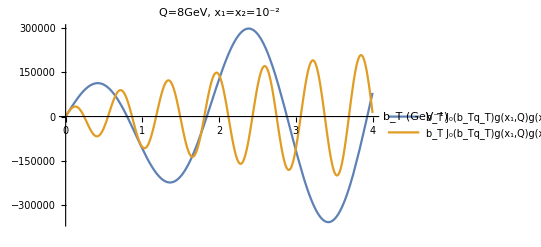

```mathematica
Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->3,bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->10},{bt,0,4},PlotLegends->{"b_T J_0(b_Tq_T)g(x_1,Q)g(x_2,Q)   q_T=3GeV","b_T J_0(b_Tq_T)g(x_1,Q)g(x_2,Q)   q_T=10GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"Q=8GeV, x_1=x_2=10^-2"]
```

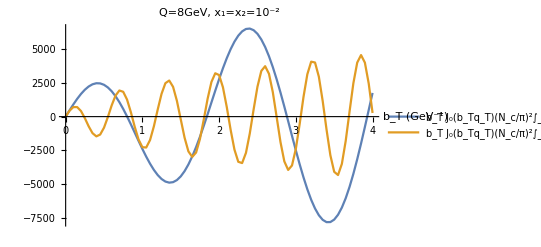

```mathematica
ListPlot[{Chhqt3,Chhqt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=3GeV","b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

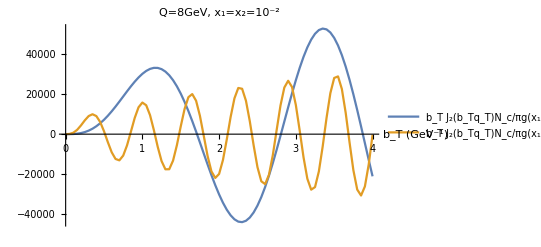

```mathematica
ListPlot[{Cw3fhqt3,Cw3fhqt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)N_c/πg(x_1,Q)∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=3GeV","b_T J_2(b_Tq_T)N_c/πg(x_1,Q)∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

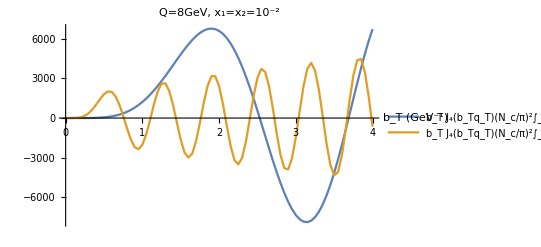

```mathematica
ListPlot[{Cw4hhqt3,Cw4hhqt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=3GeV","b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

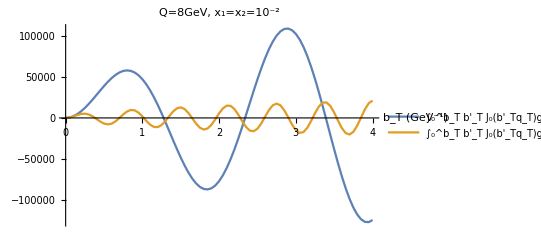

```mathematica
ListPlot[{Cffqt3ev,Cffqt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)g(x_1,Q)g(x_2,Q)   q_T=3GeV","∫_0^b_T b'_T J_0(b'_Tq_T)g(x_1,Q)g(x_2,Q)   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

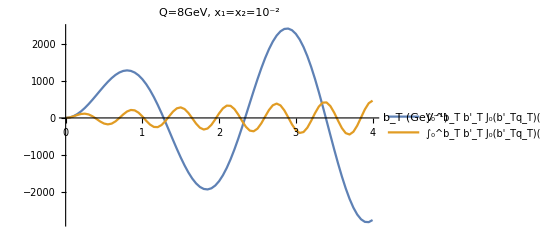

```mathematica
ListPlot[{Chhqt3ev,Chhqt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=3GeV","∫_0^b_T b'_T J_0(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

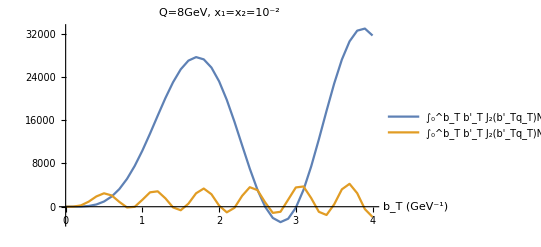

```mathematica
ListPlot[{Cw3fhqt3ev,Cw3fhqt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_2(b'_Tq_T)N_c/πg(x_1,Q)∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=3GeV","∫_0^b_T b'_T J_2(b'_Tq_T)N_c/πg(x_1,Q)∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

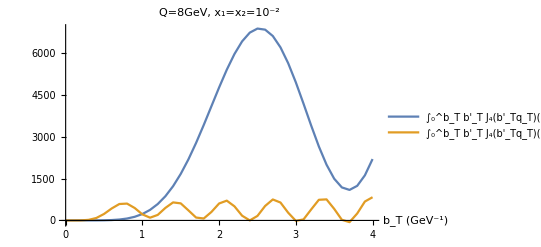

```mathematica
ListPlot[{Cw4hhqt3ev,Cw4hhqt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_4(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=3GeV","∫_0^b_T b'_T J_4(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

When α_s is evaluated at μbar~1/b_T^*, it increasing with increasing distances b_T, until it reaches the upper bound α_s(b_0/b_Tmax). It will therefore contribute to magnify the large b_T values in the integrand.

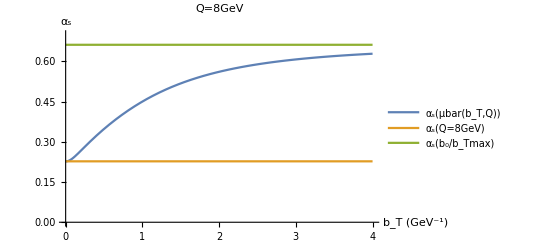
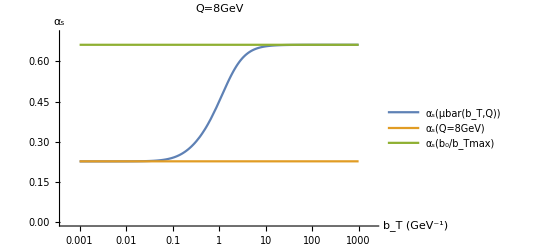

```mathematica
{Plot[{αs[μbar[bt,8]],αs[8],αs[b0/btmax]},{bt,0,4},PlotRange->{0,0.7},PlotLegends->{"α_s(μbar(b_T,Q))","α_s(Q=8GeV)","α_s(b_0/b_Tmax)"},AxesLabel->{"b_T (GeV^-1)","α_s"},PlotLabel->"Q=8GeV"],LogLinearPlot[{αs[μbar[bt,8]],αs[8],αs[b0/btmax]},{bt,10^-3,10^3},PlotRange->{0,0.7},PlotLegends->{"α_s(μbar(b_T,Q))","α_s(Q=8GeV)","α_s(b_0/b_Tmax)"},AxesLabel->{"b_T (GeV^-1)","α_s"},PlotLabel->"Q=8GeV"]}
```

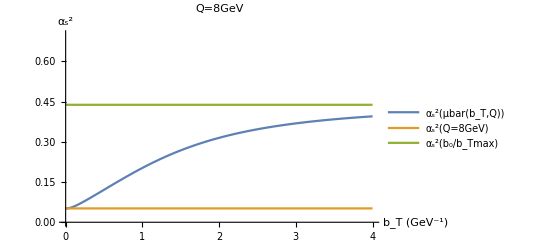
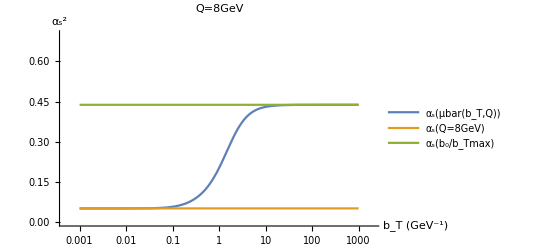

```mathematica
{Plot[{αs[μbar[bt,8]]^2,αs[8]^2,αs[b0/btmax]^2},{bt,0,4},PlotRange->{0,0.7},PlotLegends->{"α_s^2(μbar(b_T,Q))","α_s^2(Q=8GeV)","α_s^2(b_0/b_Tmax)"},AxesLabel->{"b_T (GeV^-1)","α_s^2"},PlotLabel->"Q=8GeV"],LogLinearPlot[{αs[μbar[bt,8]]^2,αs[8]^2,αs[b0/btmax]^2},{bt,10^-3,10^3},PlotRange->{0,0.7},PlotLegends->{"α_s(μbar(b_T,Q))","α_s(Q=8GeV)","α_s(b_0/b_Tmax)"},AxesLabel->{"b_T (GeV^-1)","α_s^2"},PlotLabel->"Q=8GeV"]}
```

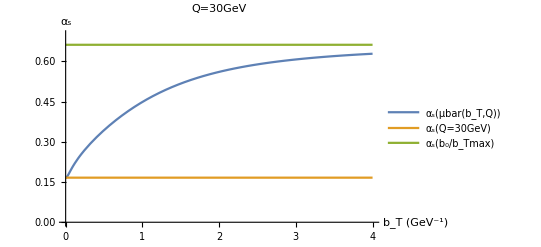
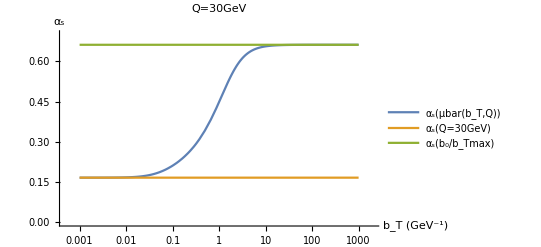

```mathematica
{Plot[{αs[μbar[bt,30]],αs[30],αs[b0/btmax]},{bt,0,4},PlotRange->{0,0.7},PlotLegends->{"α_s(μbar(b_T,Q))","α_s(Q=30GeV)","α_s(b_0/b_Tmax)"},AxesLabel->{"b_T (GeV^-1)","α_s"},PlotLabel->"Q=30GeV"],LogLinearPlot[{αs[μbar[bt,30]],αs[30],αs[b0/btmax]},{bt,10^-3,10^3},PlotRange->{0,0.7},PlotLegends->{"α_s(μbar(b_T,Q))","α_s(Q=30GeV)","α_s(b_0/b_Tmax)"},AxesLabel->{"b_T (GeV^-1)","α_s"},PlotLabel->"Q=30GeV"]}
```

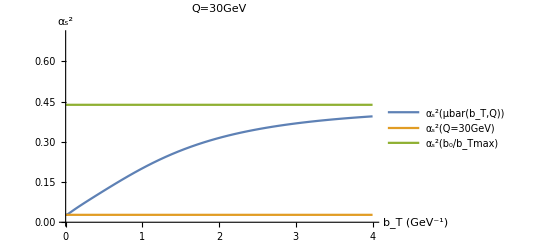
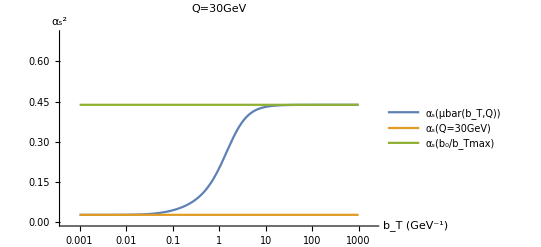

```mathematica
{Plot[{αs[μbar[bt,30]]^2,αs[30]^2,αs[b0/btmax]^2},{bt,0,4},PlotRange->{0,0.7},PlotLegends->{"α_s^2(μbar(b_T,Q))","α_s^2(Q=30GeV)","α_s^2(b_0/b_Tmax)"},AxesLabel->{"b_T (GeV^-1)","α_s^2"},PlotLabel->"Q=30GeV"],LogLinearPlot[{αs[μbar[bt,30]]^2,αs[30]^2,αs[b0/btmax]^2},{bt,10^-3,10^3},PlotRange->{0,0.7},PlotLegends->{"α_s(μbar(b_T,Q))","α_s(Q=30GeV)","α_s(b_0/b_Tmax)"},AxesLabel->{"b_T (GeV^-1)","α_s^2"},PlotLabel->"Q=30GeV"]}
```

```mathematica
ffmub[x_,Q_,bt_]:=gMSTW[x,μbar[bt,Q]]^2;
fhmub[x_,Q_,bt_]:=gMSTW[x,μbar[bt,Q]]NIntegrate[(1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y2,x,1}];
hhmub[x_,Q_,bt_]:=NIntegrate[(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
fhmubqg[x_,Q_,bt_]:=gMSTW[x,μbar[bt,Q]] αs[μbar[bt,Q]]/π NIntegrate[(1/x-1/y2)(Nc gMSTW[y2,μbar[bt,Q]]+Cf qMSTW[y2,μbar[bt,Q]]),{y2,x,1}];
hhmubqg[x_,Q_,bt_]:=(αs[μbar[bt,Q]]/π)^2 NIntegrate[(1/x-1/y1)(Nc gMSTW[y1,μbar[bt,Q]]+Cf qMSTW[y1,μbar[bt,Q]])(1/x-1/y2)(Nc gMSTW[y2,μbar[bt,Q]]+Cf qMSTW[y2,μbar[bt,Q]]),{y1,x,1},{y2,x,1}];
```

```mathematica
ffmubbt=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-2,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbt=Transpose[{Range[0,4,0.05],ParallelMap[fhmub[10^-2,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbt=Transpose[{Range[0,4,0.05],ParallelMap[hhmub[10^-2,8,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ffmubbt2=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbt2=Transpose[{Range[0,4,0.05],ParallelMap[fhmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbt2=Transpose[{Range[0,4,0.05],ParallelMap[hhmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ffmubbt3=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-2,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbt3=Transpose[{Range[0,4,0.05],ParallelMap[((Nc αs[μbar[#,8]])/π)fhmub[10^-2,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbt3=Transpose[{Range[0,4,0.05],ParallelMap[((Nc αs[μbar[#,8]])/π)^2 hhmub[10^-2,8,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ffmubbt4=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbt4=Transpose[{Range[0,4,0.05],ParallelMap[((Nc αs[μbar[#,30]])/π)fhmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbt4=Transpose[{Range[0,4,0.05],ParallelMap[((Nc αs[μbar[#,30]])/π)^2 hhmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
fhmubbtqg1=Transpose[{Range[0,4,0.05],ParallelMap[fhmubqg[10^-2,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbtqg1=Transpose[{Range[0,4,0.05],ParallelMap[hhmubqg[10^-2,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbtqg2=Transpose[{Range[0,4,0.05],ParallelMap[fhmubqg[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbtqg2=Transpose[{Range[0,4,0.05],ParallelMap[hhmubqg[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
ffmubbtx3=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-3,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbtx3=Transpose[{Range[0,4,0.05],ParallelMap[fhmub[10^-3,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbtx3=Transpose[{Range[0,4,0.05],ParallelMap[hhmub[10^-3,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
ffmubbtx32=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-3,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbtx32=Transpose[{Range[0,4,0.05],ParallelMap[fhmub[10^-3,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbtx32=Transpose[{Range[0,4,0.05],ParallelMap[hhmub[10^-3,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
ffmubbtx33=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-3,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbtx33=Transpose[{Range[0,4,0.05],ParallelMap[((Nc αs[μbar[#,8]])/π)fhmub[10^-3,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbtx33=Transpose[{Range[0,4,0.05],ParallelMap[((Nc αs[μbar[#,8]])/π)^2 hhmub[10^-3,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
ffmubbtx34=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-3,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbtx34=Transpose[{Range[0,4,0.05],ParallelMap[((Nc αs[μbar[#,30]])/π)fhmub[10^-3,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbtx34=Transpose[{Range[0,4,0.05],ParallelMap[((Nc αs[μbar[#,30]])/π)^2 hhmub[10^-3,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbtx3qg1=Transpose[{Range[0,4,0.05],ParallelMap[fhmubqg[10^-3,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbtx3qg1=Transpose[{Range[0,4,0.05],ParallelMap[hhmubqg[10^-3,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbtx3qg2=Transpose[{Range[0,4,0.05],ParallelMap[fhmubqg[10^-3,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbtx3qg2=Transpose[{Range[0,4,0.05],ParallelMap[hhmubqg[10^-3,30,#] &,Range[0,4,0.05]]}];
```

When the scale of the PDF inside the splitting function is set to μbar as well, it still tends to suppress the large b_T values. But it does so softlier than the PDF alone, therefore favoring large b_T values in comparison with the simple PDF used for f_1^g inside C[f_1^gf_1^g]. The b_T-broadening is logically enhanced when the two TMDs are splitting functions.
When the two effects are combined in the complete expression of h_1^(⊥g), the b_T-broadening is even stronger as α_S suppresses the small-b_T values.

No significant difference between Q=8GeV and Q=30GeV for the splitting function (Q-dependence through μbar, abbreviated as μ_B in the following plots)

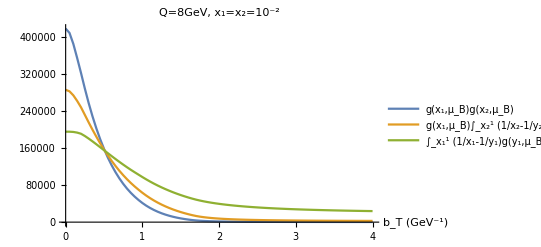
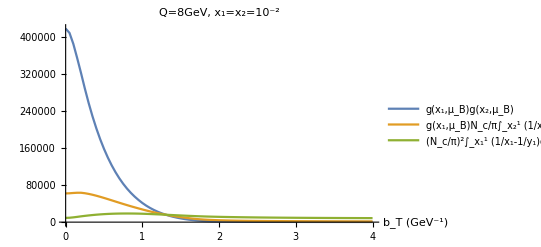

```mathematica
{ListPlot[{ffmubbt,fhmubbt,hhmubbt},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True],ListPlot[{ffmubbt3,fhmubbt3,hhmubbt3},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)N_c/π∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]}
```

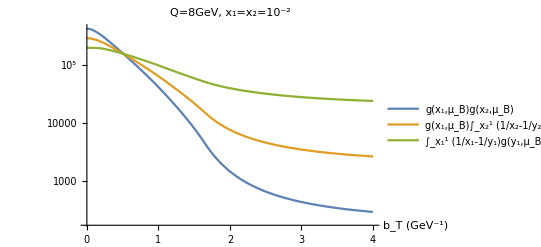
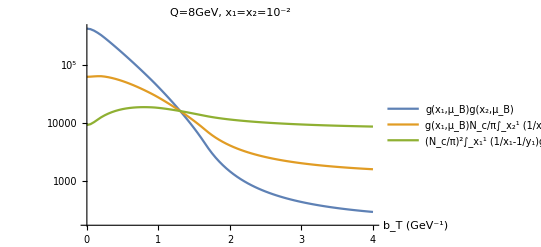

```mathematica
{ListLogPlot[{ffmubbt,fhmubbt,hhmubbt},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True],ListLogPlot[{ffmubbt3,fhmubbt3,hhmubbt3},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)N_c/π∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]}
```

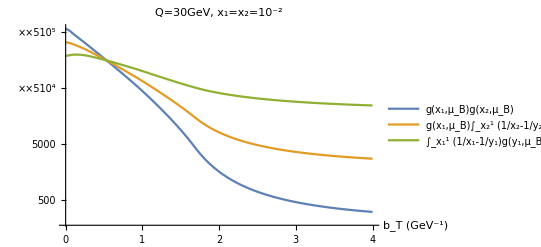
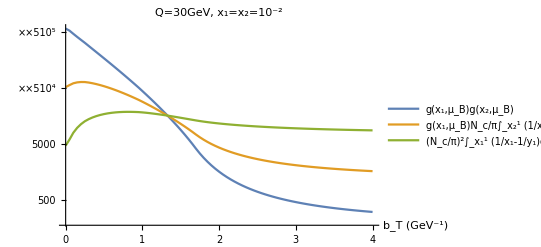

```mathematica
{ListLogPlot[{ffmubbt2,fhmubbt2,hhmubbt2},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2"},PlotLabel->"Q=30GeV, x_1=x_2=10^-2",Joined->True],ListLogPlot[{ffmubbt4,fhmubbt4,hhmubbt4},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)N_c/π∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2"},PlotLabel->"Q=30GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]}
```

RE- TÉLÉCHARGER rec3.mx AVEC LES BONNES VALEURS ET RE-RUNNER (FAIT)

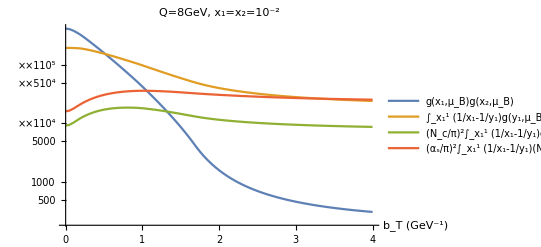

```mathematica
ListLogPlot[{ffmubbt,hhmubbt,hhmubbt3,hhmubbtqg1},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(α_s/π)^2∫_x_1^1 (1/x_1-1/y_1)(N_cg(y_1,μ_B)+C_F∑_f q_f(y_1,μ_B))ⅆy_1∫_x_2^1 (1/x_2-1/y_2)(N_cg(y_2,μ_B)+C_F∑_f q_f(y_2,μ_B))ⅆy_2"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

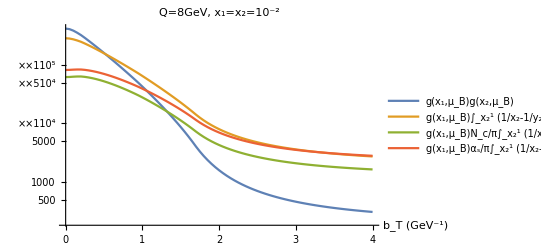

```mathematica
ListLogPlot[{ffmubbt,fhmubbt,fhmubbt3,fhmubbtqg1},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","g(x_1,μ_B)N_c/π∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","g(x_1,μ_B)α_s/π∫_x_2^1 (1/x_2-1/y_2)(N_cg(y_2,μ_B)+C_F∑_f q_f(y_2,μ_B))ⅆy_2"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

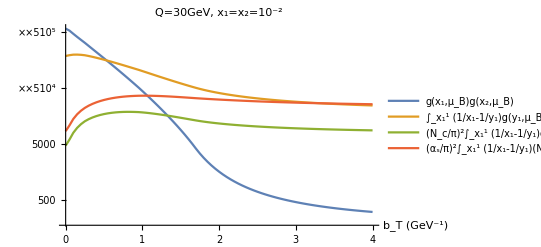

```mathematica
ListLogPlot[{ffmubbt2,hhmubbt2,hhmubbt4,hhmubbtqg2},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(α_s/π)^2∫_x_1^1 (1/x_1-1/y_1)(N_cg(y_1,μ_B)+C_F∑_f q_f(y_1,μ_B))ⅆy_1∫_x_2^1 (1/x_2-1/y_2)(N_cg(y_2,μ_B)+C_F∑_f q_f(y_2,μ_B))ⅆy_2"},PlotLabel->"Q=30GeV, x_1=x_2=10^-2",Joined->True]
```

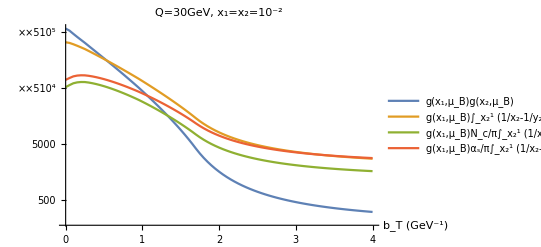

```mathematica
ListLogPlot[{ffmubbt2,fhmubbt2,fhmubbt4,fhmubbtqg2},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","g(x_1,μ_B)N_c/π∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","g(x_1,μ_B)α_s/π∫_x_2^1 (1/x_2-1/y_2)(N_cg(y_2,μ_B)+C_F∑_f q_f(y_2,μ_B))ⅆy_2"},PlotLabel->"Q=30GeV, x_1=x_2=10^-2",Joined->True]
```

Large b_T limit:    ∫_x_2^1 (1/x_2-1/y_2)g(y_2,b_0/b_Tmax)ⅆ y_2     VS     ""(SubscriptBox[α, s] (
SubscriptBox[b, 0]/
SubscriptBox[b, Tmax]))/π∫_x_2^1 (1/x_2-1/y_2)(N_cg(y_2,b_0/b_Tmax)+C_F∑_f q_f(y_2,b_0/b_Tmax))ⅆy_2"

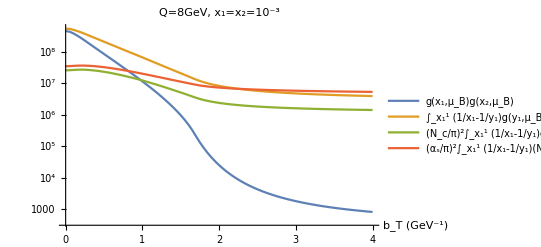

```mathematica
ListLogPlot[{ffmubbtx3,hhmubbtx3,hhmubbtx33,hhmubbtx3qg1},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(α_s/π)^2∫_x_1^1 (1/x_1-1/y_1)(N_cg(y_1,μ_B)+C_F∑_f q_f(y_1,μ_B))ⅆy_1∫_x_2^1 (1/x_2-1/y_2)(N_cg(y_2,μ_B)+C_F∑_f q_f(y_2,μ_B))ⅆy_2"},PlotLabel->"Q=8GeV, x_1=x_2=10^-3",Joined->True]
```

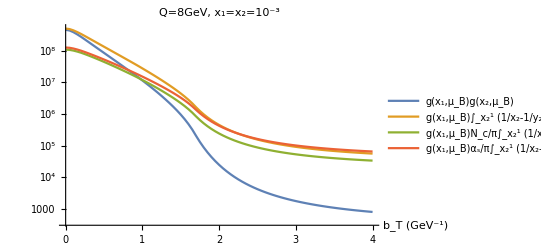

```mathematica
ListLogPlot[{ffmubbtx3,fhmubbtx3,fhmubbtx33,fhmubbtx3qg1},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","g(x_1,μ_B)N_c/π∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","g(x_1,μ_B)α_s/π∫_x_2^1 (1/x_2-1/y_2)(N_cg(y_2,μ_B)+C_F∑_f q_f(y_2,μ_B))ⅆy_2"},PlotLabel->"Q=8GeV, x_1=x_2=10^-3",Joined->True]
```

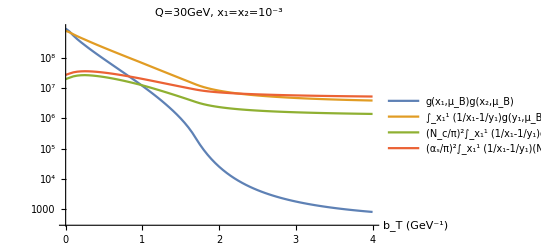

```mathematica
ListLogPlot[{ffmubbtx32,hhmubbtx32,hhmubbtx34,hhmubbtx3qg2},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(α_s/π)^2∫_x_1^1 (1/x_1-1/y_1)(N_cg(y_1,μ_B)+C_F∑_f q_f(y_1,μ_B))ⅆy_1∫_x_2^1 (1/x_2-1/y_2)(N_cg(y_2,μ_B)+C_F∑_f q_f(y_2,μ_B))ⅆy_2"},PlotLabel->"Q=30GeV, x_1=x_2=10^-3",Joined->True]
```

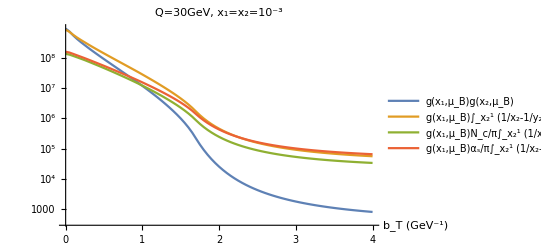

```mathematica
ListLogPlot[{ffmubbtx32,fhmubbtx32,fhmubbtx34,fhmubbtx3qg2},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","g(x_1,μ_B)N_c/π∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","g(x_1,μ_B)α_s/π∫_x_2^1 (1/x_2-1/y_2)(N_cg(y_2,μ_B)+C_F∑_f q_f(y_2,μ_B))ⅆy_2"},PlotLabel->"Q=30GeV, x_1=x_2=10^-3",Joined->True]
```

```mathematica
Export["comp_distrhh.dat",Transpose[{ffmubbtx32[[All,1]],ffmubbtx32[[All,2]],hhmubbtx32[[All,2]],hhmubbtx34[[All,2]],hhmubbtx3qg2[[All,2]]}]];
```

```mathematica
Export["comp_distrfh.dat",Transpose[{ffmubbtx32[[All,1]],ffmubbtx32[[All,2]],fhmubbtx32[[All,2]],fhmubbtx34[[All,2]],fhmubbtx3qg2[[All,2]]}]];
```

```mathematica
ih=0;x=10^-2;q=8;
upv=xf[ih,x,q,8]/x
dnv=xf[ih,x,q,7]/x
usea=xf[ih,x,q,-2]/x
dsea=xf[ih,x,q,-1]/x
str=xf[ih,x,q,3]/x
sbar=xf[ih,x,q,-3]/x
chm=xf[ih,x,q,4]/x
cbar=xf[ih,x,q,-4]/x
bot=xf[ih,x,q,5]/x
bbar=xf[ih,x,q,-5]/x
glu=xf[ih,x,q,0]/x
sumq=(xf[ih,x,q,8]+xf[ih,x,q,7]+xf[ih,x,q,-2]+xf[ih,x,q,-1]+xf[ih,x,q,3]+xf[ih,x,q,-3]+xf[ih,x,q,4]+xf[ih,x,q,-4]+xf[ih,x,q,5]+xf[ih,x,q,-5])/x
Clear[ih,x,q];
```

20.248

13.88

37.186

37.982

25.972

25.899

16.749

16.749

5.1852

5.1852

647.15

205.035

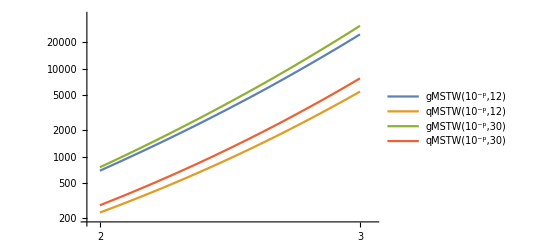

```mathematica
LogLogPlot[{gMSTW[10^-p,12],qMSTW[10^-p,12],gMSTW[10^-p,30],qMSTW[10^-p,30]},{p,3,2},PlotLegends->"Expressions"]
```

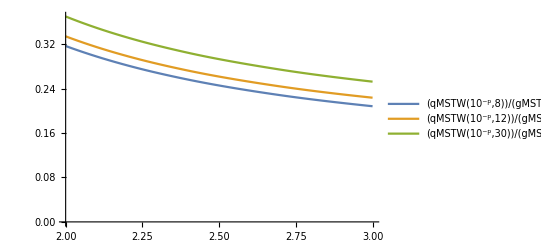

```mathematica
Plot[{qMSTW[10^-p,8]/gMSTW[10^-p,8],qMSTW[10^-p,12]/gMSTW[10^-p,12],qMSTW[10^-p,30]/gMSTW[10^-p,30]},{p,2,3},PlotLegends->"Expressions",AxesOrigin->{2,0}]
```

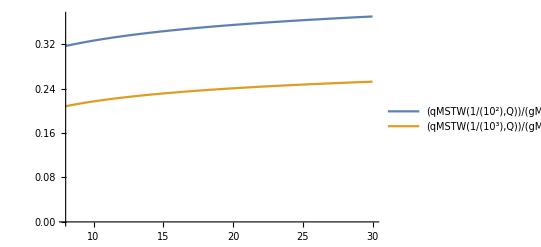

```mathematica
Plot[{qMSTW[10^-2,Q]/gMSTW[10^-2,Q],qMSTW[10^-3,Q]/gMSTW[10^-3,Q]},{Q,8,30},PlotLegends->"Expressions",AxesOrigin->{8,0}]
```

C[w_0 h_1^(⊥g) h_1^(⊥g)], which only difference with C[f_1^g f_1^g] is the replacement of f_1^gas a PDF by h_1^(⊥g) as α_s x splitting function twice, suffers a maximal suppression from the two effects : normalisation suppression by the α_s^2 factor and double b_T-broadening that makes it quickly fall with increasing q_T.
Because J_2 and J_4reduce the number of oscillations present within the same b_T-range as compared to J_0, they actually counter the suppression effect associated with b_T-broadening. A peak in q_Twill appear for the associated convolutions. Example: in the case of the integrand containing J_4 for q_T=1GeV, the first oscillation is dilated to the large b_T to a point where it will not have time to grow enough before being suppressed by the Sudakov factors. The convolution will thus be small in the small q_T-region. It will increase with q_T as the oscillatory integrand contracts in frequency, reaching a peak value, before the oscillation balance effect cancels the integrand again as q_T increases too much: then the number of oscillations inside the relevant b_T region becomes too large and they can balance, canceling the integral.

```mathematica
Chhint2[x_,Q_,qt_,bt_]:=bt BesselJ[0,qt bt]((Nc αs[μbar[bt,Q]])/π)^2 NIntegrate[(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
Cw3fhint2[x_,Q_,qt_,bt_]:=bt BesselJ[2,qt bt]((Nc αs[μbar[bt,Q]])/π)NIntegrate[gMSTW[x,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y2,x,1}];
```

```mathematica
Cw4hhint2[x_,Q_,qt_,bt_]:=bt BesselJ[4,qt bt]((Nc αs[μbar[bt,Q]])/π)^2 NIntegrate[(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
Chh2qt1=Transpose[{Range[0,4,0.05],ParallelMap[Chhint2[10^-2,8,1,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh2qt6=Transpose[{Range[0,4,0.05],ParallelMap[Chhint2[10^-2,8,6,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh2qt10=Transpose[{Range[0,4,0.05],ParallelMap[Chhint2[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh2qt1=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint2[10^-2,8,1,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fh2qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint2[10^-2,8,6,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fh2qt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint2[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw4hh2qt1=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint2[10^-2,8,1,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh2qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint2[10^-2,8,6,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh2qt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint2[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cffint2ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[0,qt btp] gMSTW[x,μbar[btp,Q]]^2,{btp,0,bt}];
```

```mathematica
Chhint2ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[0,qt btp]((Nc αs[μbar[btp,Q]])/π)^2(1/x-1/y1)gMSTW[y1,μbar[btp,Q]](1/x-1/y2)gMSTW[y2,μbar[btp,Q]],{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw3fhint2ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[2,qt btp]((Nc αs[μbar[btp,Q]])/π)gMSTW[x,μbar[btp,Q]](1/x-1/y2)gMSTW[y2,μbar[btp,Q]],{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw4hhint2ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[4,qt btp]((Nc αs[μbar[btp,Q]])/π)^2(1/x-1/y1)gMSTW[y1,μbar[btp,Q]](1/x-1/y2)gMSTW[y2,μbar[btp,Q]],{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cff2qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffint2ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

```mathematica
Cff2qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffint2ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.2004}. NIntegrate obtained 4246.6 and 0.00925249 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198331}. NIntegrate obtained 4195.73 and 0.0190512 for the integral and error estimates.

```mathematica
Cff2qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffint2ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.196838}. NIntegrate obtained 763.703 and 0.00100979 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.196831}. NIntegrate obtained 810.824 and 0.0010111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198197}. NIntegrate obtained 793.299 and 0.00154283 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.942132}. NIntegrate obtained 781.122 and 0.00100937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197316}. NIntegrate obtained 783.205 and 0.00110843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.200335}. NIntegrate obtained 774.721 and 0.00542777 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195205}. NIntegrate obtained 807.906 and 0.00110837 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197192}. NIntegrate obtained 797.017 and 0.00104036 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.211164}. NIntegrate obtained 798.394 and 0.00169725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198406}. NIntegrate obtained 806.341 and 0.0051237 for the integral and error estimates.

```mathematica
Chh2qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhint2ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17736.9 and 0.0599607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7648.13 and 0.0131361 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 15263.2 and 0.0292393 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18317.1 and 0.054129 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17034.3 and 0.0402628 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19102.2 and 0.0658628 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4960.7 and 0.00587604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 10427.4 and 0.0164715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18772.9 and 0.0561432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 13027. and 0.0313884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19303.2 and 0.0597288 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19374.6 and 0.0573828 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19315.8 and 0.0600452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1785.02 and 0.0018382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9045.79 and 0.0200498 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19127.1 and 0.0688512 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3753.79 and 0.0101201 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11763. and 0.0260179 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17800.7 and 0.114013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18810. and 0.0586054 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 16209.9 and 0.106535 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 14198.7 and 0.0236563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6271.44 and 0.041147 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18366.7 and 0.0788013 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17116.7 and 0.0565999 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 15418.3 and 0.0704032 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 14418.6 and 0.0849581 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 16320.3 and 0.0641636 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 13330.2 and 0.0876356 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 12163. and 0.110941 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 10927.7 and 0.094061 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6933.7 and 0.128715 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8300.36 and 0.118187 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5549.51 and 0.126925 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9636.02 and 0.102991 for the integral and error estimates.

```mathematica
Chh2qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhint2ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1037.94 and 0.00420347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 813.397 and 0.00968489 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -39.1928 and 0.00563937 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -989.181 and 0.0235669 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 445.816 and 0.012771 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.68617 and 0.000833946 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -600.231 and 0.0190374 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -918.217 and 0.00194366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -940.706 and 0.0224477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -267.899 and 0.0352333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -734.312 and 0.0281488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 246.649 and 0.0338229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 630.144 and 0.0325098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 749.008 and 0.0300228 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 324.939 and 0.00050315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -622.608 and 0.00499401 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -478.168 and 0.00174993 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 503.587 and 0.00775838 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 787.133 and 0.00915906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -79.2485 and 0.0184187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1142.19 and 0.00252466 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 561.321 and 0.0338335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 131.611 and 0.0370482 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -391.004 and 0.0444639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -824.059 and 0.0512901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1015.03 and 0.048734 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -894.749 and 0.050719 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -502.397 and 0.0583516 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 27.1207 and 0.0668163 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 774.173 and 0.0916661 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 509.316 and 0.298223 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 725.943 and 0.0944093 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 377.637 and 0.127527 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -152.117 and 0.136466 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -679.378 and 0.14463 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1018.62 and 0.162305 for the integral and error estimates.

```mathematica
Chh2qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhint2ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 123.254 and 0.000382431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -93.8733 and 0.000409506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 329.508 and 0.00231608 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -324.916 and 0.000735576 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 65.0694 and 0.00361484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -490.705 and 0.0055144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 260.331 and 0.0311942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -115.981 and 0.0425803 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -279.673 and 0.0195343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.971 and 0.0191061 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 371.97 and 0.0279317 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -446.532 and 0.0133152 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 192.701 and 0.00886716 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 239.574 and 0.00684753 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -410.729 and 0.0409412 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -353.141 and 0.0444778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 102.844 and 0.000106288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -322.231 and 0.000598531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -361.932 and 0.00822977 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -26.225 and 0.00138206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 391.378 and 0.00231306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -199.523 and 0.0098953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.35241 and 0.0599554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 333.574 and 0.0627609 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 330.893 and 0.0642214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.43811 and 0.074511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -225.078 and 0.0140472 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -416.822 and 0.0782076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 422.554 and 0.00714051 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -363.422 and 0.0692348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -111.289 and 0.0774175 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 274.548 and 0.0839979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 384.828 and 0.113225 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 114.318 and 0.101128 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -291.373 and 0.0996602 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -458.559 and 0.1042 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -229.439 and 0.108404 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 189.137 and 0.117916 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 412.24 and 0.109721 for the integral and error estimates.

```mathematica
Cw3fh2qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhint2ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh2qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhint2ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh2qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhint2ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh2qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhint2ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 187.014 and 0.000190839 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 245.055 and 0.000261011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 50.9476 and 0.0000582293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00032812 and 4.09991×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 140.221 and 0.000264933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3685.94 and 0.00378413 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3184.07 and 0.00346028 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4860.21 and 0.00529115 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7090.02 and 0.00731536 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8914.88 and 0.0105563 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7967.48 and 0.00906084 for the integral and error estimates.

```mathematica
Cw4hh2qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhint2ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1212.49 and 0.0188109 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1194.61 and 0.015111 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3316.08 and 0.0034499 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1989.68 and 0.0111963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1517.98 and 0.0172582 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2540.45 and 0.0308438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2012.52 and 0.023415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3094.47 and 0.0050573 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3072.94 and 0.0254109 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2935.6 and 0.0300261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.403172 and 5.20882×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2955.8 and 0.00374261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2908.74 and 0.0252744 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3364.99 and 0.00439585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1478.1 and 0.0153378 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2495.87 and 0.0340644 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1242.38 and 0.0691509 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1968.27 and 0.0361935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2586.14 and 0.00920905 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1498.62 and 0.0409791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2129.57 and 0.057725 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1286.19 and 0.0412179 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1618.02 and 0.0497892 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2650.9 and 0.0651788 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3074.23 and 0.0780216 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3006.46 and 0.0698702 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2827.79 and 0.0951221 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2346.92 and 0.124435 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1792.25 and 0.11614 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1351.94 and 0.129185 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1177.86 and 0.133647 for the integral and error estimates.

```mathematica
Cw4hh2qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhint2ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 354.197 and 0.00591136 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 306.045 and 0.00405858 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 811.128 and 0.0360634 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 231.173 and 0.0129097 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 540.49 and 0.0179026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 416.713 and 0.0379984 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 928.657 and 0.0180313 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.81958 and 5.19728×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1054.75 and 0.0219489 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 655.078 and 0.00776172 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1094.81 and 0.0093634 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 223.384 and 0.0362427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 403.7 and 0.0432972 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 121.586 and 0.0662839 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 809.187 and 0.00147313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 756.541 and 0.0118589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 796.25 and 0.0533037 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 931.967 and 0.0879664 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1048.4 and 0.060955 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 278.607 and 0.0122189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 297.818 and 0.0991425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 549.925 and 0.0640128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1040.89 and 0.00531475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 660.599 and 0.0785915 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 246.497 and 0.0629333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1022.52 and 0.0954799 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1007.71 and 0.0707344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 687.7 and 0.0913792 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 304.949 and 0.0984873 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 223.674 and 0.103093 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 522.102 and 0.101195 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 931.854 and 0.0972686 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1078.89 and 0.112281 for the integral and error estimates.

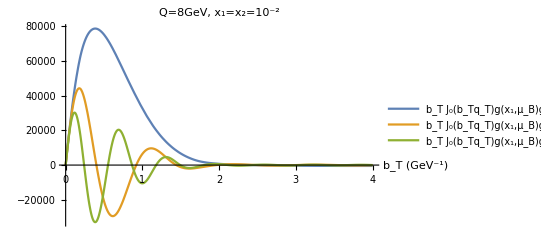

```mathematica
Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->1,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->6,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->10},{bt,0,4},PlotLegends->{"b_T J_0(b_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   q_T=1GeV","b_T J_0(b_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   q_T=6GeV","b_T J_0(b_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   q_T=10GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"Q=8GeV, x_1=x_2=10^-2"]
```

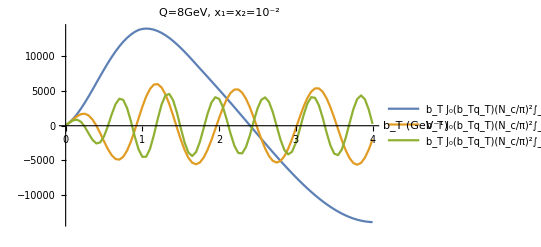

```mathematica
ListPlot[{Chh2qt1,Chh2qt6,Chh2qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

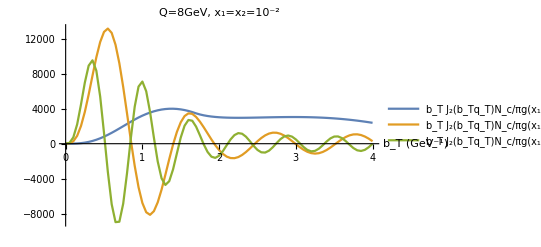

```mathematica
ListPlot[{Cw3fh2qt1,Cw3fh2qt6,Cw3fh2qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_2(b_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_2(b_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

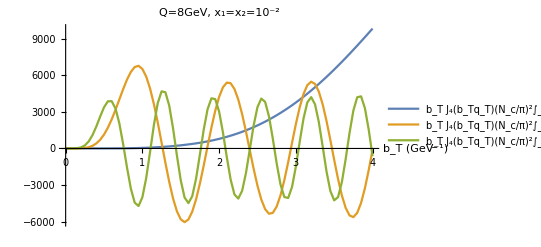

```mathematica
ListPlot[{Cw4hh2qt1,Cw4hh2qt6,Cw4hh2qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

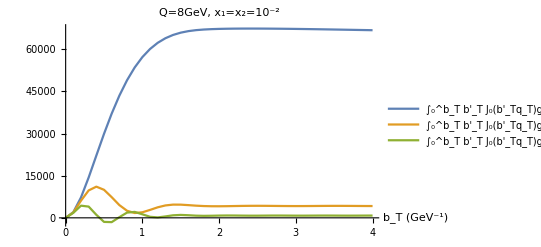

```mathematica
ListPlot[{Cff2qt1ev,Cff2qt6ev,Cff2qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

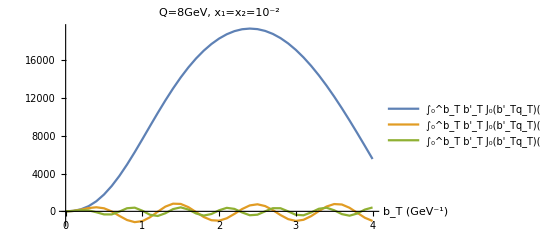

```mathematica
ListPlot[{Chh2qt1ev,Chh2qt6ev,Chh2qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

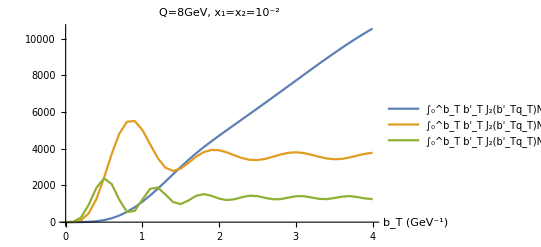

```mathematica
ListPlot[{Cw3fh2qt1ev,Cw3fh2qt6ev,Cw3fh2qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_2(b'_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_2(b'_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_2(b'_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

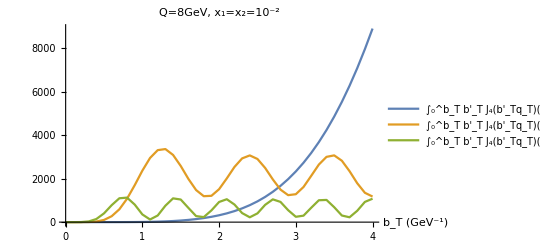

```mathematica
ListPlot[{Cw4hh2qt1ev,Cw4hh2qt6ev,Cw4hh2qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_4(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_4(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_4(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

```mathematica
Chhint3[x_,Q_,qt_,bt_]:=bt BesselJ[0,qt bt]((Nc αs[μbar[bt,Q]])/π)^2 ⅇ^(-Sresult[μbar[bt,Q],Q])NIntegrate[(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
Cw3fhint3[x_,Q_,qt_,bt_]:=bt BesselJ[2,qt bt]((Nc αs[μbar[bt,Q]])/π)ⅇ^(-Sresult[μbar[bt,Q],Q])NIntegrate[gMSTW[x,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y2,x,1}];
```

```mathematica
Cw4hhint3[x_,Q_,qt_,bt_]:=bt BesselJ[4,qt bt]((Nc αs[μbar[bt,Q]])/π)^2 ⅇ^(-Sresult[μbar[bt,Q],Q])NIntegrate[(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
Chh3qt1=Transpose[{Range[0,4,0.05],ParallelMap[Chhint3[10^-2,8,1,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh3qt6=Transpose[{Range[0,4,0.05],ParallelMap[Chhint3[10^-2,8,6,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh3qt10=Transpose[{Range[0,4,0.05],ParallelMap[Chhint3[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh3qt1=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint3[10^-2,8,1,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fh3qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint3[10^-2,8,6,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fh3qt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint3[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw4hh3qt1=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint3[10^-2,8,1,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh3qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint3[10^-2,8,6,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh3qt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint3[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cffint3ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[0,qt btp] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[x,μbar[btp,Q]]^2,{btp,0,bt}];
```

```mathematica
Chhint3ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[0,qt btp]((Nc αs[μbar[btp,Q]])/π)^2 ⅇ^(-Sresult[μbar[bt,Q],Q])(1/x-1/y1)gMSTW[y1,μbar[btp,Q]](1/x-1/y2)gMSTW[y2,μbar[btp,Q]],{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw3fhint3ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[2,qt btp]((Nc αs[μbar[btp,Q]])/π)ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[x,μbar[btp,Q]](1/x-1/y2)gMSTW[y2,μbar[btp,Q]],{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw4hhint3ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[4,qt btp]((Nc αs[μbar[btp,Q]])/π)^2 ⅇ^(-Sresult[μbar[bt,Q],Q])(1/x-1/y1)gMSTW[y1,μbar[btp,Q]](1/x-1/y2)gMSTW[y2,μbar[btp,Q]],{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cff3qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffint3ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

```mathematica
Cff3qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffint3ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.2004}. NIntegrate obtained 578.287 and 0.00125997 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197282}. NIntegrate obtained 568.12 and 0.00110264 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198406}. NIntegrate obtained 550.713 and 0.00140647 for the integral and error estimates.

```mathematica
Cff3qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffint3ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.196838}. NIntegrate obtained 140.012 and 0.000185128 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.196831}. NIntegrate obtained 131.135 and 0.000163525 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198197}. NIntegrate obtained 125.08 and 0.000243259 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195205}. NIntegrate obtained 115.104 and 0.000157912 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197192}. NIntegrate obtained 111.735 and 0.00014585 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.942132}. NIntegrate obtained 107.873 and 0.000139394 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.2004}. NIntegrate obtained 105.499 and 0.000392768 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197316}. NIntegrate obtained 105.266 and 0.000148978 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.202473}. NIntegrate obtained 106.002 and 0.000130065 for the integral and error estimates.

```mathematica
Chh3qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhint3ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4100.52 and 0.013862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3893.12 and 0.00668668 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3272.35 and 0.00387616 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4302.9 and 0.00824295 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4007.99 and 0.011844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4220.19 and 0.00666638 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4332.57 and 0.0104393 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4182.54 and 0.009886 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3906.33 and 0.0116825 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3796.24 and 0.0130891 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3678.08 and 0.0113808 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3552. and 0.0105201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3418.08 and 0.0106255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1764.38 and 0.00181695 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4088.95 and 0.00906307 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3622.51 and 0.0237673 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3276.41 and 0.011794 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4331.83 and 0.00721719 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2839.44 and 0.00765506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4298.12 and 0.00950678 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4251.47 and 0.0279415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3127.14 and 0.00974307 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2806.65 and 0.0179766 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2636.16 and 0.00871701 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2090.2 and 0.012316 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2277.25 and 0.0103984 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2970.45 and 0.0127446 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2459.48 and 0.00966951 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1899.18 and 0.0124856 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1705.14 and 0.015553 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1509.11 and 0.0129898 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1115.61 and 0.0158848 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1312.2 and 0.014025 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 920.581 and 0.0170894 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 728.405 and 0.0166596 for the integral and error estimates.

```mathematica
Chh3qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhint3ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -528.34 and 0.00213969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 270.524 and 0.00322105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -605.706 and 0.00128214 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 125.681 and 0.00360033 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -15.8622 and 0.00228237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -216.444 and 0.0051567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -147.379 and 0.00467439 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -152.798 and 0.00585729 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.80013 and 0.000723432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -217.478 and 0.00518957 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -53.2404 and 0.00700202 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 46.997 and 0.00644468 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 115.526 and 0.00599414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 132.543 and 0.00537481 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 321.182 and 0.000497333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -281.437 and 0.00225743 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -659.751 and 0.00145829 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 240.143 and 0.0027943 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -361.695 and 0.00132368 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -20.785 and 0.00483078 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 184.008 and 0.00283487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 96.1524 and 0.00606501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 21.8802 and 0.00629967 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -63.2372 and 0.00721618 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -129.93 and 0.00808695 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -74.203 and 0.00861841 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -156.325 and 0.00750557 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -134.84 and 0.0076434 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.93156 and 0.00968605 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 72.5633 and 0.0424885 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 108.532 and 0.0128508 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 100.252 and 0.0134399 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 51.4253 and 0.0173661 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -20.4452 and 0.0183417 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -90.2004 and 0.0192024 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -133.699 and 0.0213035 for the integral and error estimates.

```mathematica
Chh3qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhint3ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 148.698 and 0.000461381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.895 and 0.000453224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 217.361 and 0.00152781 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -281.859 and 0.000638098 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 33.1222 and 0.00184006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -198.599 and 0.0022318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -22.0993 and 0.00811334 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 51.7363 and 0.00617106 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 77.4008 and 0.00581212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 79.6789 and 0.00227739 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 54.3251 and 0.00249977 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -64.6564 and 0.00451515 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -75.3 and 0.00769437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -109.64 and 0.00326936 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 24.9382 and 0.00418063 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -62.4911 and 0.00786082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 122.915 and 0.000127032 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -318.506 and 0.000591612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -163.604 and 0.00372009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 226.068 and 0.00133607 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -19.8371 and 0.00104541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.9046 and 0.00361568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.745633 and 0.0107868 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 55.4563 and 0.0217549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 128.915 and 0.00217847 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -59.0325 and 0.00368423 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 53.5153 and 0.0103429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.542088 and 0.0117487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -62.8155 and 0.011786 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -16.4371 and 0.0114344 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -55.971 and 0.0106629 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 39.8 and 0.0121768 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 54.8272 and 0.0161314 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 16.0263 and 0.0141773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -62.445 and 0.0141868 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -40.2384 and 0.0137514 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -30.8377 and 0.0145717 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 25.1115 and 0.0156557 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 54.1088 and 0.0144015 for the integral and error estimates.

```mathematica
Cw3fh3qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhint3ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh3qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhint3ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh3qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhint3ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh3qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhint3ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 45.9187 and 0.0000468579 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 16.9444 and 0.0000193662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 56.6532 and 0.000060342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000395858 and 4.94629×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 36.7766 and 0.0000694855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 534.334 and 0.000548569 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 470.28 and 0.000511076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 681.359 and 0.000741773 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1057.83 and 0.001203 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 952.932 and 0.000983219 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1170.13 and 0.00138557 for the integral and error estimates.

```mathematica
Cw4hh3qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhint3ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 280.31 and 0.0043488 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 293.32 and 0.0037103 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1342.09 and 0.00139625 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 560.918 and 0.00315638 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 332.152 and 0.00377629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1029.17 and 0.00168198 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 418.772 and 0.00487228 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 504.87 and 0.00612967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 559.355 and 0.00571599 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 563.37 and 0.00453276 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.486403 and 6.28413×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1336.1 and 0.00169177 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 514.724 and 0.00442652 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 387.67 and 0.00402274 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1229.55 and 0.00160622 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 788.996 and 0.00280955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 195.887 and 0.0107313 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 427.534 and 0.00599515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 327.223 and 0.00592583 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 242.373 and 0.00651205 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 198.087 and 0.00627614 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 314.533 and 0.00837265 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 243.837 and 0.00739371 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 384.288 and 0.00956704 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 428.337 and 0.0097843 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 430.98 and 0.0105026 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 390.516 and 0.0126337 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 319.595 and 0.0160173 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 240.888 and 0.0153768 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 179.496 and 0.0170954 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 154.601 and 0.0173886 for the integral and error estimates.

```mathematica
Cw4hh3qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhint3ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 180.297 and 0.00300905 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 161.198 and 0.00709083 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 123.863 and 0.00164259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 184.675 and 0.00224971 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.40165 and 6.27021×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 79.4014 and 0.00716585 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 219.476 and 0.00453948 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 364.117 and 0.00273016 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 56.7614 and 0.00324395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 40.9535 and 0.00653901 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 124.953 and 0.00416978 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 203.201 and 0.00405131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 71.4379 and 0.0074944 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 467.402 and 0.000850911 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 54.9601 and 0.0299622 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 276.436 and 0.00433316 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 73.0718 and 0.00328945 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 174.296 and 0.00948783 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 136.395 and 0.00876129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 150.727 and 0.0141281 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 317.56 and 0.00161962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 44.8815 and 0.0148054 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 86.7071 and 0.00998554 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 97.5691 and 0.011635 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 37.9632 and 0.011663 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 146.083 and 0.0102113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 145.681 and 0.0136025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 42.1132 and 0.0136262 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 96.4095 and 0.0128095 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 30.4592 and 0.0139505 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 70.173 and 0.0133898 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 123.721 and 0.012582 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 141.61 and 0.0146491 for the integral and error estimates.

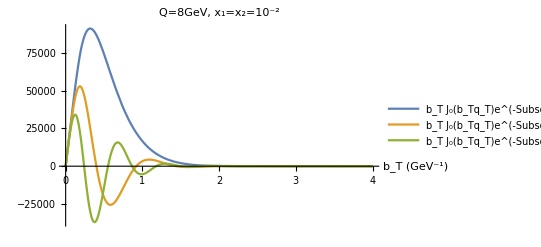

```mathematica
Plot[{bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->1,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->10},{bt,0,4},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   q_T=1GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   q_T=6GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   q_T=10GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"Q=8GeV, x_1=x_2=10^-2"]
```

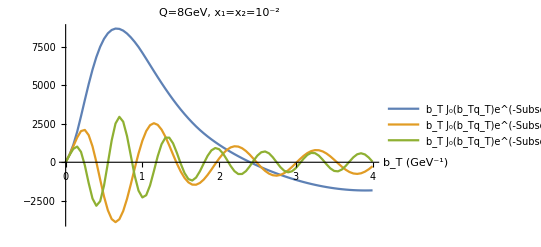

```mathematica
ListPlot[{Chh3qt1,Chh3qt6,Chh3qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

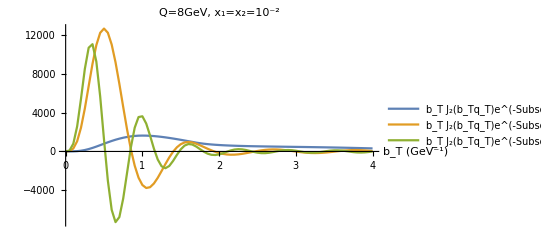

```mathematica
ListPlot[{Cw3fh3qt1,Cw3fh3qt6,Cw3fh3qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

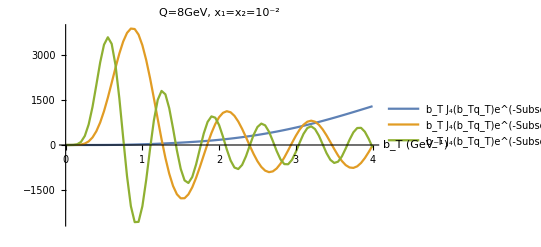

```mathematica
ListPlot[{Cw4hh3qt1,Cw4hh3qt6,Cw4hh3qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

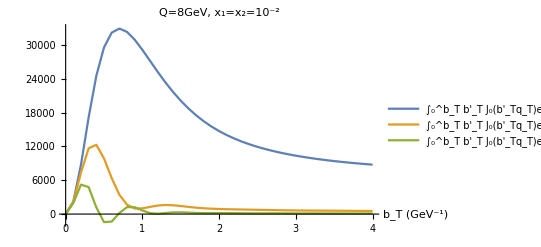

```mathematica
ListPlot[{Cff3qt1ev,Cff3qt6ev,Cff3qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))g(x_1,μ_B)g(x_2,μ_B)   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))g(x_1,μ_B)g(x_2,μ_B)   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))g(x_1,μ_B)g(x_2,μ_B)   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

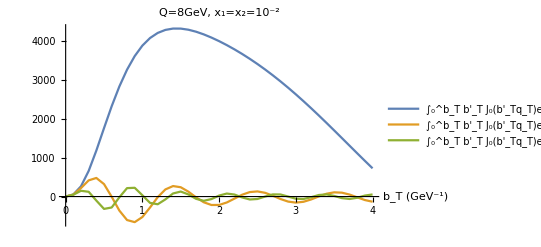

```mathematica
ListPlot[{Chh3qt1ev,Chh3qt6ev,Chh3qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

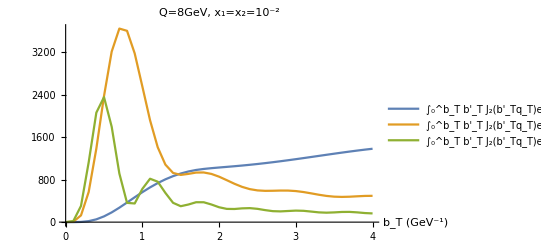

```mathematica
ListPlot[{Cw3fh3qt1ev,Cw3fh3qt6ev,Cw3fh3qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_2(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_2(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_2(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

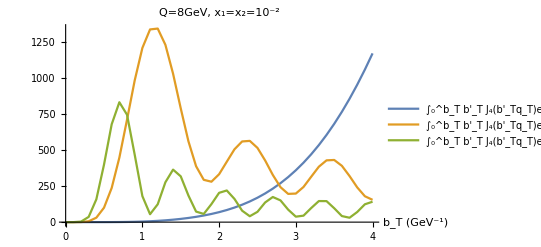

```mathematica
ListPlot[{Cw4hh3qt1ev,Cw4hh3qt6ev,Cw4hh3qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_4(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_4(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_4(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

```mathematica
Chh4qt1=Transpose[{Range[0,4,0.05],ParallelMap[Chhint3[10^-2,30,1,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh4qt6=Transpose[{Range[0,4,0.05],ParallelMap[Chhint3[10^-2,30,6,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh4qt10=Transpose[{Range[0,4,0.05],ParallelMap[Chhint3[10^-2,30,10,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh4qt1=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint3[10^-2,30,1,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fh4qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint3[10^-2,30,6,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fh4qt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint3[10^-2,30,10,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw4hh4qt1=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint3[10^-2,30,1,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh4qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint3[10^-2,30,6,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh4qt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint3[10^-2,30,10,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

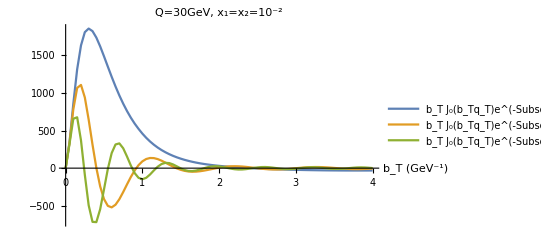

```mathematica
ListPlot[{Chh4qt1,Chh4qt6,Chh4qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=30GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

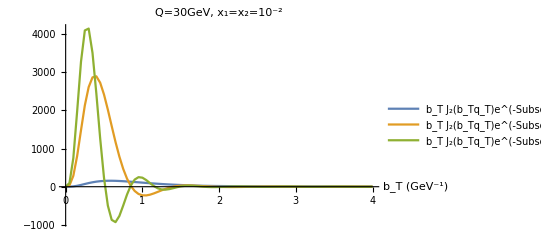

```mathematica
ListPlot[{Cw3fh4qt1,Cw3fh4qt6,Cw3fh4qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=30GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

```mathematica
ListPlot[{Cw4hh4qt1,Cw4hh4qt6,Cw4hh4qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=30GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

-Graphics-

It is a little harder to compare the actions of the different elements in the integrand on the integral as the latter is not stable when any of the Sudakov factors are removed. One can only compute the convolutions with all the elements together.

```mathematica
ChhintNoS[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[0,qt bt]((Nc αs[μbar[bt,Q]])/π)^2(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1},{bt,0,∞}];
```

```mathematica
Cw3fhintNoS[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[2,qt bt]((Nc αs[μbar[bt,Q]])/π)gMSTW[x,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y2,x,1},{bt,0,∞}];
```

```mathematica
Cw4hhintNoS[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[4,qt bt]((Nc αs[μbar[bt,Q]])/π)^2(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1},{bt,0,∞}];
```

```mathematica
ChhintNoSnp[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[0,qt bt]((Nc αs[μbar[bt,Q]])/π)^2 ⅇ^(-Sresult[μbar[bt,Q],Q])(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1},{bt,0,∞}];
```

```mathematica
Cw3fhintNoSnp[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[2,qt bt]((Nc αs[μbar[bt,Q]])/π)ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[x,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y2,x,1},{bt,0,∞}];
```

```mathematica
Cw4hhintNoSnp[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[4,qt bt]((Nc αs[μbar[bt,Q]])/π)^2 ⅇ^(-Sresult[μbar[bt,Q],Q])(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1},{bt,0,∞}];
```

```mathematica
Chhinttunebt[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[0,qt bt]((Nc αs[μbar[bt,Q]])/π)^2 ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1},{bt,0,∞}];
```

```mathematica
Cw3fhinttunebt[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[2,qt bt]((Nc αs[μbar[bt,Q]])/π)ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y2,x,1},{bt,0,∞}];
```

```mathematica
Cw4hhinttunebt[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[4,qt bt]((Nc αs[μbar[bt,Q]])/π)^2 ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1},{bt,0,∞}];
```

```mathematica
qtvalsQ8=Range[0,4,0.1];
qtvalsQ30=Range[0,15,0.1];
```

```mathematica
Chhbt2Q8=Transpose[{qtvalsQ8,ParallelMap[Chhinttunebt[10^-2,8,#,0.64]&,qtvalsQ8]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3519.85 and 0.0110218 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4529.31 and 0.0138348 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0123311 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3763.37 and 0.0122101 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3258.25 and 0.0104911 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4171.27 and 0.0122651 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2845.82 and 0.00860001 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4506.06 and 0.0137886 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2984.93 and 0.0087834 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4437. and 0.013247 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2427.32 and 0.00746053 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2706.05 and 0.00781269 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2566.33 and 0.00754036 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4324.27 and 0.0126405 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2289.65 and 0.00704977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2153.87 and 0.00618209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3390.91 and 0.0104512 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3122.66 and 0.00979291 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3876.38 and 0.0122771 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3644.27 and 0.0115363 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4081.04 and 0.0121587 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4523.49 and 0.01375 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4477.15 and 0.0132626 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4385.91 and 0.0129924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4252.55 and 0.0123286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1762.93 and 0.00563993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1639.49 and 0.00556967 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2020.51 and 0.00577822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1404.9 and 0.00532508 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1890.06 and 0.00550266 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1520.06 and 0.0053611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1294.24 and 0.00539797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1188.25 and 0.00514075 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1087.05 and 0.00496578 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 899.315 and 0.00488935 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 990.721 and 0.00494943 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.836 and 0.00446984 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 654.531 and 0.00418881 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 731.26 and 0.00464918 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 582.568 and 0.00411082 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 515.268 and 0.00424845 for the integral and error estimates.

```mathematica
Chhbt2Q30=Transpose[{qtvalsQ30,ParallelMap[Chhinttunebt[10^-2,30,#,0.64]&,qtvalsQ30]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 628.525 and 0.00358523 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 723.356 and 0.00363298 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 749.667 and 0.00310519 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 434.91 and 0.00210972 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 370.815 and 0.00191032 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 567.018 and 0.00302322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 501.29 and 0.00252818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 311.154 and 0.00156811 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 681.906 and 0.00362801 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 257.282 and 0.00145767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 758.69 and 0.00312589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 168.956 and 0.00113356 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 81.4366 and 0.00112927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 209.851 and 0.00119901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 134.3 and 0.00102115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 105.346 and 0.000984751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 616.747 and 0.0036897 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 745.738 and 0.00317485 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 716.187 and 0.00302064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 421.828 and 0.00209497 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 358.473 and 0.00178208 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 554.089 and 0.00290212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 487.961 and 0.00246826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 672.068 and 0.00290876 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 247.271 and 0.00146035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 299.886 and 0.00149366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 758.327 and 0.00311875 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 77.1991 and 0.00119503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 161.54 and 0.00123413 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 201.154 and 0.00114329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 128.073 and 0.00106526 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 100.183 and 0.00100366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 604.676 and 0.00371983 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 741.126 and 0.00313833 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 708.433 and 0.00298637 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 408.859 and 0.00198285 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 541.022 and 0.00279638 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 346.325 and 0.00173335 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 474.635 and 0.00236168 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 661.78 and 0.00301913 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 237.521 and 0.00153003 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 288.86 and 0.00155702 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 757.237 and 0.00288126 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 73.1302 and 0.0011251 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 192.718 and 0.00111813 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 154.371 and 0.00115153 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 95.2157 and 0.00109211 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 122.07 and 0.000995733 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 61.8816 and 0.00151134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 46.0175 and 0.00113606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 33.2382 and 0.00101134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 23.0101 and 0.000799554 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.512909 and 0.00105516 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 14.8756 and 0.000764261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.4076 and 0.000928094 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.44864 and 0.000763746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.98351 and 0.00110221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.9903 and 0.000943902 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.57095 and 0.00106752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.8201 and 0.00116114 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 58.4339 and 0.0012812 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.78633 and 0.00107154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.5172 and 0.00139958 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.0526 and 0.00105523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 43.233 and 0.00110383 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.4259 and 0.000948348 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 31.0042 and 0.000888371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.18247 and 0.00110831 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 21.2291 and 0.000821645 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 13.4648 and 0.000761446 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.5418 and 0.00993328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.33877 and 0.000824487 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.41567 and 0.00109533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.53071 and 0.000972317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.91285 and 0.00104648 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 55.1286 and 0.00122521 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.08618 and 0.00103794 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.98942 and 0.00138507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.66801 and 0.00109013 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 40.5672 and 0.00108536 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.1599 and 0.000973779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.4971 and 0.00103726 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 28.8681 and 0.000888405 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.81758 and 0.00105377 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19.5283 and 0.000844608 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.28196 and 0.00090695 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.71811 and 0.000939425 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.82362 and 0.00106287 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 12.1193 and 0.000766639 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.04219 and 0.00101674 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.23428 and 0.0010683 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.3354 and 0.00113586 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.17853 and 0.00107864 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.80714 and 0.0010686 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.2576 and 0.000994981 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.5605 and 0.00103222 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
Chhbt4Q8=Transpose[{qtvalsQ8,ParallelMap[Chhinttunebt[10^-2,8,#,0.16]&,qtvalsQ8]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 10037.7 and 0.0397513 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8110.89 and 0.0301035 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9900.04 and 0.038971 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8885.92 and 0.0328356 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7243.18 and 0.0264958 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6344.49 and 0.0232093 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4638.37 and 0.0203021 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3885.92 and 0.0194747 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3540.41 and 0.0205639 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3215.87 and 0.0204847 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2912.17 and 0.0215106 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2628.89 and 0.0218914 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2365.41 and 0.0192865 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2120.98 and 0.0182906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9502.2 and 0.0349475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5464.64 and 0.0201421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 10003. and 0.039643 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7684.55 and 0.0299001 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9731.58 and 0.0376987 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8514.14 and 0.0313943 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9217.92 and 0.0331124 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6794.26 and 0.0236234 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5899.67 and 0.0215737 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4252.15 and 0.0204269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5043.23 and 0.0194142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1685.88 and 0.0184351 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1493.46 and 0.0173159 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1894.76 and 0.0181027 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1154.4 and 0.0165129 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1316.59 and 0.0163597 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1006.04 and 0.0153973 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 870.648 and 0.0155288 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 747.429 and 0.0145269 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 635.588 and 0.0141026 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 443.017 and 0.0146436 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 534.363 and 0.0139573 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 360.841 and 0.0143631 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 287.15 and 0.0148325 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 221.29 and 0.0135248 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 162.637 and 0.0134094 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 110.594 and 0.0141375 for the integral and error estimates.

```mathematica
Chhbt4Q30=Transpose[{qtvalsQ30,ParallelMap[Chhinttunebt[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1167.12 and 0.00541616 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1059.58 and 0.00475957 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 462.5 and 0.00420032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1138.59 and 0.00518368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 946.435 and 0.00403951 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 817.785 and 0.00361367 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 688.687 and 0.00329412 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 568.669 and 0.00320614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 371.701 and 0.00330066 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 295.849 and 0.00271978 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 233.495 and 0.00249221 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 182.787 and 0.00201354 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 141.848 and 0.0018735 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 108.963 and 0.00197591 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 82.6547 and 0.00186288 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 61.6812 and 0.00182154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1126.4 and 0.00516921 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 443.103 and 0.00415764 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1165.96 and 0.00542482 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1039.07 and 0.00432265 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 921.388 and 0.00400371 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 791.616 and 0.00360057 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 663.745 and 0.00312729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 546.241 and 0.00319793 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 355.372 and 0.00308479 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 282.355 and 0.0027298 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 222.483 and 0.00236298 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 173.876 and 0.00199692 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 134.677 and 0.0017772 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 103.219 and 0.00194671 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 78.0691 and 0.00188858 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 58.0328 and 0.00193815 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 424.328 and 0.00380981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1162.48 and 0.00535314 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1112.27 and 0.00504548 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1017.35 and 0.00424721 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 895.874 and 0.00384827 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 765.543 and 0.00361944 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 639.232 and 0.00321749 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 524.397 and 0.00345236 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 339.633 and 0.00299592 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 269.387 and 0.00286585 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 211.922 and 0.002213 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 165.34 and 0.00201139 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 127.816 and 0.0018948 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 97.7254 and 0.00195273 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 73.6872 and 0.0020188 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 54.5488 and 0.0020952 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 45.0142 and 0.0021904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 31.8093 and 0.00196984 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 21.3802 and 0.00191882 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 13.175 and 0.00143679 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.75378 and 0.00159094 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.76567 and 0.00170377 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.07091 and 0.00191178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -11.1365 and 0.00248492 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.98535 and 0.00181468 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.27443 and 0.00211393 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.0983 and 0.00216994 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.7061 and 0.00219562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -11.4203 and 0.00216292 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -11.5829 and 0.00217469 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 42.1203 and 0.00209605 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 29.5209 and 0.00196218 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19.5768 and 0.00185899 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11.7605 and 0.00148642 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.65139 and 0.00165684 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.91425 and 0.00180727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.72099 and 0.00190979 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.78064 and 0.00178983 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.18755 and 0.00191874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.47468 and 0.00229059 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.50303 and 0.00231092 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.2689 and 0.00214858 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.8291 and 0.00223036 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -11.2201 and 0.00239108 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -11.4714 and 0.00218146 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -11.6071 and 0.0022275 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.16589 and 0.00182971 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.48689 and 0.00184514 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 39.3585 and 0.00203257 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 27.3382 and 0.00198838 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17.8582 and 0.00181808 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 10.4139 and 0.00157759 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.60365 and 0.00161694 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.106729 and 0.0018136 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.33596 and 0.00183079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.93627 and 0.00186787 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.71826 and 0.00219197 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.4266 and 0.00204926 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -10.9414 and 0.00235028 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -11.295 and 0.00251052 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -11.5153 and 0.00219025 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -11.6254 and 0.0022925 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.52809 and 0.00195341 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.7672 and 0.00182576 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
ChhNoSnpQ8=Transpose[{qtvalsQ8,ParallelMap[ChhintNoSnp[10^-2,8,#]&,qtvalsQ8]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.64168164789825×10^690538901}. NIntegrate obtained 2.630625510543884`15.954589770191005*^45435514317 and 5.114427797343264`15.954589770191005*^45435514317 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,7.7756056423903916888608284174589999075439643196424758236712994385×10^308}. NIntegrate obtained -4.4625954801644037723977641970228914542769249032836631376242228703×10^464 and 2.6701859634562025796442277226619341295345208585561101746134411362×10^465 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,4.416294908086148764029479257784074110550432159712126279829686291×10^308}. NIntegrate obtained -1.3724535665705760235941455958680121506885663589355572572396793635×10^464 and 7.5664931770733465898184419395816327479036320501365979407065636486×10^464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,2.1861071733937266026949186298032705809107809753712939397201925096×10^308}. NIntegrate obtained -9.0189330558943930802187933581594594030477978838827087280216917832×10^463 and 3.4395726150879534907394788755955033872986064232307484168723115781×10^464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.1160433172639341559830728054723549697631699125135056440817373448×10^308}. NIntegrate obtained -2.1052802411145230819792079199870500577890880245157182055031427564×10^463 and 1.8096356191108397050774314742274801803099158325194402778052195006×10^464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.47569×10^308}. NIntegrate obtained 2.845105148808370945471787104998645726257170578339436552726173833×10^463 and 1.3613126144540812782469183171503852385328556002036988431209911357×10^464 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.0005884758713859100431288455253946254147800378267044240908286172×10^463 and 1.086233432556476399304647502076002506823404570217469708526080581×10^464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.28181×10^308}. NIntegrate obtained 1.2792711298521448704369183658653076423236265554954246481805242044×10^463 and 6.3379999308130345165878634840368307683524276346440444500403935709×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.07045×10^308}. NIntegrate obtained 5.9117361537315435570899827731119505505697692285800655438577885444×10^462 and 4.439868105917632661059557284111019250522243930096581126483362743×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,8.76761×10^307}. NIntegrate obtained -7.8704700368201653088622377945052354380779060407365220174848823262×10^462 and 3.1221284487640776400798302424719208293211285667583688143144696127×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,9.29219×10^307}. NIntegrate obtained 2.8256311031298343892303809804664436744406139400687791528830626766×10^463 and 2.845220772598442699537288717378969630657014128218025359832294348×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,8.45494×10^307}. NIntegrate obtained -2.90523770634301×10^462 and 2.57835401485466×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,8.27905×10^307}. NIntegrate obtained 7.1936973723797209352334908339538289354720433264956758561385537196×10^462 and 2.8720738484179250528474013795814862801970360993366021533061028926×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,7.19571×10^307}. NIntegrate obtained 8.3696288579239567472388668595561815746379114926370298923676237556×10^462 and 2.3305409969098016460968778294386312046397680408429061782807335408×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,7.74938×10^307}. NIntegrate obtained 1.5700963360262299138570731952201390316018946151626898040746309035×10^462 and 2.1141586024810214680178294734490227609830537569396098984512966676×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,7.26477×10^307}. NIntegrate obtained 2.4487106974199847264284041874213186416224343004699603376865659624×10^462 and 2.3433098257953335172912729183942394082953192729789667959291064202×10^463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.5245629065410528069204731408290243593398828492065944113885925178×10^309}. NIntegrate obtained -1.7569911495615033777978825026465406413636120608025078151159994108×10^465 and 1.2149736697801352705055489342470529331657232485219924687303857339×10^466 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,5.89773272475372×10^308}. NIntegrate obtained -2.97372548050823×10^463 and 1.25155935826706×10^465 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,2.6889075376855724487035083960943540880609165280961027022077668428×10^308}. NIntegrate obtained -3.7201833145676124306864265265754984568048641331880088819030535566×10^463 and 5.2235426166992387479687694373040237389398078686786091719834336659×10^464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,2.3639007711897754027000919036705451039233431339979748266311871183×10^308}. NIntegrate obtained 9.7686022257612864640833225517913762776815654067817763145853154713×10^463 and 2.2502211257412287300240043455342539660861687058256948168725300122×10^464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.97274740688344×10^308}. NIntegrate obtained 2.97608313855514×10^463 and 1.41459282821975×10^464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.56532×10^308}. NIntegrate obtained 3.7273304452275437221311300911704556901116369156557196068498889544×10^463 and 8.4467370967104468808608062126719546408963286142293323396099900443×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.2823×10^308}. NIntegrate obtained -6.7935852913370125623808012496724133390364812239270471515597501564×10^462 and 7.6382450604690124361087000071418817477939319565175113113886512267×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.09782×10^308}. NIntegrate obtained 5.18352243288738069523399165721240969587112349968870857253149539×10^461 and 5.1398361303234100140142790689225805701612287737130045007651546585×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.01581×10^308}. NIntegrate obtained -7.48180281871172×10^462 and 4.04847167815956×10^463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,6.89959×10^307}. NIntegrate obtained 8.25426226623835×10^462 and 1.92339215744699×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,5.7133×10^307}. NIntegrate obtained -6.8500582152626279591926450438761176185766132547039445406228685606×10^462 and 1.6526062371301137195182042342915286687116051026163751021397540531×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,5.7505×10^307}. NIntegrate obtained -1.6078645948547346417528581064272277799042189055836417076838732684×10^461 and 1.8395718250935798624710185177879444836091638647516918679812938383×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,6.37993×10^307}. NIntegrate obtained -4.35945756790883×10^462 and 1.57529852467985×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,5.97204×10^307}. NIntegrate obtained 3.9990018160451541781128951685788750796581607408220317110318213331×10^462 and 1.4778568029079454335289330782638269262781619638925900723572223737×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,5.84123×10^307}. NIntegrate obtained -9.49906001162358×10^461 and 1.34847052710566×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,5.78574×10^307}. NIntegrate obtained 8.421277310924256245680005615946060864936216776979485776942436637×10^462 and 1.1027269446721384859564052390375459477220936684545957280602920661×10^463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,4.33556×10^307}. NIntegrate obtained 2.11726230503149×10^462 and 1.01352176989822×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,5.25304×10^307}. NIntegrate obtained 2.3177810254043071882763197966444066411454808860510173534223526273×10^462 and 1.2391602324515280417143836526932979460901629908706542114335031103×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,5.12235×10^307}. NIntegrate obtained 3.0840331264536673086535618070314629043326266152806647895351440903×10^462 and 1.0442274394101957564077879805234290923206917544522069668942275856×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,4.33887×10^307}. NIntegrate obtained -5.1831251990165639865946297367237947857488853604696979604823287396×10^462 and 1.0913268990678459821549901356582795105235197507022827681180735738×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,4.53349×10^307}. NIntegrate obtained -1.1707502130615220102074465151587105528776358022843916810594540312×10^462 and 8.4677468302338147595666658343814482492338754950523443685944142655×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,3.89487×10^307}. NIntegrate obtained 6.12164970606236×10^461 and 9.35643450655218×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,4.26827×10^307}. NIntegrate obtained 3.06278727841×10^462 and 9.01780594996787×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,4.52312×10^307}. NIntegrate obtained 5.5383809636121086314894381776204039073423909986952977370005069927×10^462 and 8.499894588211566164958258140599329225166106955607622940793125297×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,4.17806×10^307}. NIntegrate obtained -1.2102762773235751339651525924216938013717076909766839301177605677×10^461 and 6.8046450928052459397934565105371604835524357091089302027373710586×10^462 for the integral and error estimates.

```mathematica
ChhNoSnpQ30=Transpose[{qtvalsQ30,ParallelMap[ChhintNoSnp[10^-2,30,#]&,qtvalsQ30]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.64168164789825×10^690538901}. NIntegrate obtained 3.703777335865134`15.954589770191005*^45435514315 and 7.200835575338962`15.954589770191005*^45435514315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.47569×10^308}. NIntegrate obtained 4.0057529762687424510958964214242330778670510172497444933103866685×10^461 and 1.9166539624258034538261669191646270139874316041622025906744576947×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.09782×10^308}. NIntegrate obtained 7.2981170561625992846077097537534472560946425797513675430159171314×10^459 and 7.2366091232866980455356006544012768600939733569565844679148504701×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,8.45494×10^307}. NIntegrate obtained -4.09041633973562×10^460 and 3.63018191900723×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,6.89959×10^307}. NIntegrate obtained 1.16215513699856×10^461 and 2.70803132265681×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,5.84123×10^307}. NIntegrate obtained -1.33741587474381×10^460 and 1.8985730034008×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,4.33887×10^307}. NIntegrate obtained -7.2975577725238382328570628703231634427593280533499635256316587643×10^460 and 1.5365287908090617146858401176338034798975230999614184933823149796×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,4.17806×10^307}. NIntegrate obtained -1.7040030320239330740313451038944580557081650642946627151694013876×10^459 and 9.5805694015820796609341726352369435872919633468286606619853464811×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,3.6448×10^307}. NIntegrate obtained -1.9212318486901152290437706827506096307430993526960693221350999943×10^460 and 8.2399432207292733949677721994756422117004357776088031677383767342×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,3.51245×10^307}. NIntegrate obtained -1.09372948487025×10^460 and 5.75886095149973×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,2.8974×10^307}. NIntegrate obtained 2.5487232241911578123121208279902018558824137597370128703683722142×10^460 and 5.8636354985498896089021759774835190724171605958227935383427580896×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.96667×10^307}. NIntegrate obtained -5.86929901525822×10^459 and 5.14691371578061×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.76262×10^307}. NIntegrate obtained -4.3885552566382946087462620329154194498503211282613886119254301479×10^459 and 3.7096703479350780749982174946149213989799461352649125925430778637×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,2.26359×10^307}. NIntegrate obtained -2.2917482072900865944884229202184577623156545207125496072798631515×10^460 and 3.5819072002102871151792476070444194241626098146306511273706613781×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,2.08804×10^307}. NIntegrate obtained 1.5827151464347776793493938090239476617942122997721476480565606695×10^460 and 2.5985271521043272429215581109404803397879162793833504009165936709×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,2.6889075376855724487035083960943540880609165280961027022077668428×10^308}. NIntegrate obtained -5.2378153372770994462221795441059749309014881069738735970211788977×10^461 and 7.35446329365836714059612104636391454774583814365342708880135518×10^462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.5245629065410528069204731408290243593398828492065944113885925178×10^309}. NIntegrate obtained -2.4737477732876132854879461302220105258797825055708216630447138829×10^463 and 1.7106167045700767260826263636485496762093690575226472582269186073×10^464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.56532×10^308}. NIntegrate obtained 5.2478781076899234157822181190230040540797155781391349834242357002×10^461 and 1.1892545440395750778719358013304693603426580387468213187018769515×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.07045×10^308}. NIntegrate obtained 8.3234022836182579711946155900578174933052488837873940551424866925×10^460 and 6.2510922968766919674241664976715073819588695483244357711563177405×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,8.27905×10^307}. NIntegrate obtained 1.0128333805819414564739391995189150361583422657323573895814957772×10^461 and 4.043723435382464805489729540708707868173855435537504368573921747×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,5.7133×10^307}. NIntegrate obtained -9.6445086027471080392322932199409858523340953381676361983677785515×10^460 and 2.326779506113121350860746366541448167711620478752422879819131313×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,5.78574×10^307}. NIntegrate obtained 1.1856699449701555081784891730897067938804256338719518933598252187×10^461 and 1.5525794336572251459145637389238119582021604043906683310516294898×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,4.53349×10^307}. NIntegrate obtained -1.6483524879221705745738344251988584210011336905334572407033699234×10^460 and 1.1922126000055240265735453804703504793314036147714022788235484683×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,4.20364×10^307}. NIntegrate obtained 3.7265656113272339064895079899740993564206800563336362680212899817×10^460 and 9.6174143270449500306586773597699754466616313384560844748909611481×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,3.65594×10^307}. NIntegrate obtained 2.5189766669469195844705312459653171737009663264942046343185218706×10^460 and 8.1811925985415930022518936265567381946765615235144535697677502566×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,3.10551×10^307}. NIntegrate obtained -1.97562487933019×10^460 and 6.16306194796163×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.80719×10^307}. NIntegrate obtained 2.08425799868769×10^459 and 5.20981174399238×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.788×10^307}. NIntegrate obtained -1.05660041097469×10^460 and 3.02948301271527×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.61414×10^307}. NIntegrate obtained -1.9462443038818195012962524881101757058197599656688067187056761266×10^460 and 3.463762311633807954721468677093410799705642958692816774037801244×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,2.31062×10^307}. NIntegrate obtained -9.68157650585742×10^459 and 3.21703079954348×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.29047×10^307}. NIntegrate obtained -1.02394881958043×10^459 and 2.61958371862582×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,2.1861071733937266026949186298032705809107809753712939397201925096×10^308}. NIntegrate obtained -1.2698166163225642160066818632782877272135099004293476565517685783×10^462 and 4.8427307671745522562779977389432443690099573872312875337402097373×10^462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,7.7756056423903916888608284174589999075439643196424758236712994385×10^308}. NIntegrate obtained -6.2830912010542424249326195199947309204725477117132331386239065153×10^462 and 3.7594762973121062560782686108943888699611439596296664455914769152×10^463 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.8230014473630466631993550979861129700331155759238800893549336517×10^461 and 1.5291448221934400947735941499252166384722611878131291759201580381×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.01581×10^308}. NIntegrate obtained -1.05339705709868×10^461 and 5.70002745976531×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,7.19571×10^307}. NIntegrate obtained 1.1783981242990538788961793107562207894843968460633767493859183412×10^461 and 3.2812746968588571133135880642626270795114312666426740313448403899×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,5.7505×10^307}. NIntegrate obtained -2.2637857124451407332083828031182780063671119321840845750220870505×10^459 and 2.5900168633539149480078543901172125042509704169135816526747125556×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,4.33556×10^307}. NIntegrate obtained 2.98098992350907×10^460 and 1.4269834097286×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.218921,0.218921,4.85583×10^307}. NIntegrate obtained -1.3181579227789046582731372535145080476983104980104011012654743227×10^460 and 8.529182051860835743884199121939557197751529505198815601180956844×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,4.17328×10^307}. NIntegrate obtained 1.47298906125742×10^460 and 8.2070288510744×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,3.73913×10^307}. NIntegrate obtained 2.71643470319779×10^460 and 7.70373238626022×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,3.39268×10^307}. NIntegrate obtained 2.0297070538617852486184466128963142291019426112528283969474866463×10^460 and 5.6733388576833528769807611620966003743430636383872505528853419383×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,3.10906×10^307}. NIntegrate obtained -6.52101959796322×10^459 and 5.4908652648012×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.34163×10^307}. NIntegrate obtained 1.0617835683027560672517089587142479331654051267119438027821492831×10^460 and 5.4629714463485348729936805175506540451720597968722712443234400352×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.64117×10^307}. NIntegrate obtained -1.051855973893393009085656922576959086970559503068159374746513509×10^460 and 4.2822474219412815609257796155046287963799374429828202940539906603×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.35057×10^307}. NIntegrate obtained -5.23397411147731×10^459 and 3.10946763357748×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,2.32652×10^307}. NIntegrate obtained 6.3489844505716343746311749539429508866509139703951461156538250485×10^459 and 3.1633618329616505617720468956281623089712677769469200734244362139×10^460 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,2.3639007711897754027000919036705451039233431339979748266311871183×10^308}. NIntegrate obtained 1.3753659493470037692837261182009090264779149474046025659569337364×10^462 and 3.1681886961105929466783911511643923628816211278982744923585873971×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.3141×10^308}. NIntegrate obtained -1.4511544048778392264603895491198712010540050602821513853082399163×10^460 and 7.8255849786654301719824957899294586617484418393686128611981492791×10^461 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.7434691208560845680182113543036450308475241412115626418480950428×10^459 and 5.1766969405770290500100402242022355806281731786671845466437723797×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,9.35912×10^306}. NIntegrate obtained 1.2027181294810002275802672569045683550593571166616062859437103254×10^460 and 4.7869797661962692795166575495335518417179719359003527799565779691×10^459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.24884×10^307}. NIntegrate obtained 1.93387801937519×10^459 and 8.51649391611576×10^459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.80546×10^307}. NIntegrate obtained -3.87675498349864×10^459 and 1.65565267700162×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.26798×10^307}. NIntegrate obtained 6.2101576579596438504289473619961751391885963632227336576790342281×10^458 and 8.9071984026873652119444553223650850311957260494660961257183722027×10^459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.76403×10^307}. NIntegrate obtained -2.11051369759909×10^459 and 1.70583718609885×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.55705×10^307}. NIntegrate obtained 1.75049968013034×10^459 and 1.23314071195805×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.37809×10^307}. NIntegrate obtained -3.5127960852790682702970824650400763834437212044710488245700476644×10^459 and 1.1493737728627738442332363535087021556888309441449240516946360565×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.50809×10^307}. NIntegrate obtained 1.4724811700604970348404428937895399873762723838090942175794977409×10^459 and 1.4069424176404983409186392700800625531827982830225790022363572688×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.04322×10^307}. NIntegrate obtained -4.3521685191948029218986951891121580997509109427437934470264360651×10^459 and 2.4196543996725211701433977381725385105709476101432339288105961022×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.14608×10^307}. NIntegrate obtained 1.5436396798966953786919862308466535527126026975808272764035082688×10^459 and 2.5012635210453310507987281757854862486396639478178381052801358869×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.14472×10^307}. NIntegrate obtained -4.4203171859422562840103287326523699942897427262806854719810659539×10^458 and 1.1168040065455366119012577263169799635678589891063233614662276287×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.12189×10^307}. NIntegrate obtained -8.9980594678438894410738109588865906018044131609862479460215118886×10^458 and 7.1465850180062307187240983504201722899245314652566329108038785768×10^459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.15565×10^307}. NIntegrate obtained 1.3802870752379436535208606613543470759986796137030661323631117382×10^459 and 1.1459323685378997321977413105945621753875595499040457473948914998×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.28937×10^307}. NIntegrate obtained 7.7158293356167712559911172799413401431966850690792702561197269638×10^459 and 1.25352938975379110165960757452156889373624549429916939199037458×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.91736×10^307}. NIntegrate obtained 7.336928981359682990099541807510711556665569410464952443854690642×10^459 and 2.1124777540300241170633662249926718521718708171500123188804029918×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.67378×10^307}. NIntegrate obtained 2.9472318510115×10^457 and 1.81852302692085×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.20088×10^307}. NIntegrate obtained 2.81916044206648×10^459 and 7.15897965125027×10^459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.81372×10^307}. NIntegrate obtained 1.0608888258203668801623205370625138857363076117920809066267231482×10^459 and 1.8291153137320152162362527758556357672321479503804068471425797039×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.64537×10^307}. NIntegrate obtained 1.718902255669135134007396861366845137462440243050231299015809098×10^459 and 1.7214841014309606323298276269421416986382586612788439891220118625×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.27184×10^307}. NIntegrate obtained -2.2778905195834100912735036517761062751293932594519788906546343803×10^458 and 8.0104549696582897787446669390830611251219382710286433993912022422×10^459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.27329×10^307}. NIntegrate obtained -2.52633088090712×10^458 and 9.86206034914247×10^459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.51556×10^307}. NIntegrate obtained -4.8964033767797814990840328026213245388798503941933097118257544003×10^459 and 1.3969275720252637136857123435255752221915458192908208008293872187×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.34393×10^307}. NIntegrate obtained -1.764538025117257614566556319661299534843895798188360826742352427×10^459 and 8.0611408617394849057814267629074848018468274716087132611437020242×10^459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.97139×10^307}. NIntegrate obtained -1.1341636426072211297791587770648426699220556458858366849069331368×10^459 and 2.5108478021068988052458113655178216086246515309850039750185215122×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.25551×10^307}. NIntegrate obtained 6.7795256227416143009018310533099309817742654822826001829521163931×10^458 and 9.5911403041751685832097638220975683227142337577166657779764366877×10^459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.84295×10^307}. NIntegrate obtained 8.08860884460832×10^459 and 2.25876277535685×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.43097×10^307}. NIntegrate obtained 1.75882737618683978808078609964528254078560473170089708434790221×10^459 and 1.1481459550037802116911530073253206633766317559478478817186597391×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,2.01771×10^307}. NIntegrate obtained 1.0619972473194447567720829976525829005221258214568967872180660774×10^460 and 2.436409540797521144275535795041598125853613980975891878657494601×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.52192×10^307}. NIntegrate obtained -1.81745710333621×10^459 and 1.46305096439748×10^460 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.26173×10^307}. NIntegrate obtained 5.9444596930101608155376612682555183937716120364362154930777244471×10^457 and 8.817966320689075267771803996402299807943396850332449227381850881×10^459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,9.39831×10^306}. NIntegrate obtained 2.44285435996493×10^459 and 7.83565936597314×10^459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.23656×10^307}. NIntegrate obtained -6.0397358353209697224882199000366022862005175114275042226474250697×10^459 and 1.3252427975559225003164389772620309162140519477397618824985251882×10^460 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.2441×10^307}. NIntegrate obtained -1.4176741946485142974118810212334619091633026791505169703026418688×10^459 and 6.7895790347597299326166600768937338749357763991426566089368097725×10^459 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.53412×10^307}. NIntegrate obtained 1.29471966883976×10^458 and 1.18545590163688×10^460 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.21558×10^307}. NIntegrate obtained 1.1821825481954372608624135239431206291833787535836659732790610885×10^459 and 6.6961687051777363764269990273009610693174554967596287746585202896×10^459 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,8.94208×10^306}. NIntegrate obtained -3.4101616607706818302861694166625357342897367005571144071593640479×10^459 and 8.6364027203682492297278969135950091524322081999690509251208779855×10^459 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,2.09601×10^307}. NIntegrate obtained 1.1448347038045411069540134983671898395783152566042780677861617746×10^460 and 2.4622520398532406936986466300155538026412371971227667810474718945×10^460 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.87764×10^307}. NIntegrate obtained -4.03933967003895×10^459 and 2.29093548313299×10^460 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.28497×10^307}. NIntegrate obtained -1.4316878128480496147551341046677150110570551552066723253294826251×10^459 and 1.8869345474649356391567339545014010227654310029468404407411832118×10^460 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.37757×10^307}. NIntegrate obtained -2.86774132447164×10^459 and 9.51664932845255×10^459 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.49381×10^307}. NIntegrate obtained -1.370282646054436245927718638487736609076409514161956992747004898×10^459 and 1.2413375119630931708712243668457886567686101573790001485172191624×10^460 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.466421,0.218921,1.34138×10^307}. NIntegrate obtained -2.9178399660195080235409591644038709825944812070137114269664922559×10^458 and 1.9547217899382727298377476631201071653642030723661754977485200029×10^459 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.33782×10^307}. NIntegrate obtained -4.3685903676596630673112400753339557045917911294076662662486982718×10^456 and 8.9288204799406675807206875852943395658988268714322632084138776276×10^459 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.87051×10^307}. NIntegrate obtained -2.45107453535362×10^458 and 2.16578248047537×10^460 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.55055×10^307}. NIntegrate obtained 4.7912482538983400361534133368904561713537708076176138631437074998×10^459 and 1.8217629302908382984349259007288844463824040408500685063926266553×10^460 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.15083×10^307}. NIntegrate obtained -1.19307919945158×10^459 and 7.88700694760295×10^459 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.6485×10^307}. NIntegrate obtained -2.625616913922193944840161808479069431666334763088980702955232798×10^459 and 1.4288003620886170950532283693994720162867368904699542659983987592×10^460 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.427841,0.427841,1.46958×10^307}. NIntegrate obtained -5.0174837086033114917315685643198399184467693372090315490831255241×10^454 and 1.1305553693651538461604367467559855447178712435907634831674527137×10^460 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
ChhNoSQ8=Transpose[{qtvalsQ8,ParallelMap[ChhintNoS[10^-2,8,#]&,qtvalsQ8]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.64168164789825×10^690538901}. NIntegrate obtained 2.567181499541782`15.954589770191005*^45435514318 and 4.991080778870454`15.954589770191005*^45435514318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.5252×10^6}. NIntegrate obtained -2.47199×10^6 and 1.61575×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 9.69297×10^7 and 1.32418×10^8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.16711×10^6}. NIntegrate obtained 815615. and 1.40047×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.1943×10^6}. NIntegrate obtained 6.45902×10^8 and 2.24234×10^8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 8.5636×10^8 and 4.10847×10^8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.67772×10^7}. NIntegrate obtained 1.78265×10^7 and 7.67799×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.04858×10^6}. NIntegrate obtained -217991. and 2.33518×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 3.21889×10^7 and 4.54356×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.89039×10^6}. NIntegrate obtained -1.43693×10^7 and 8.26242×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.49131×10^7}. NIntegrate obtained -3.42245×10^6 and 4.64807×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.12432×10^7 and 3.25528×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained -1.31093×10^7 and 3.71373×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.11848×10^6}. NIntegrate obtained 2.96948×10^6 and 4.73259×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2.17445×10^6 and 7.05653×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -5.39519×10^6 and 1.10093×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.8557×10^6}. NIntegrate obtained -794210. and 1.40878×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.11848×10^7}. NIntegrate obtained 8.45617×10^6 and 5.23169×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.19566×10^6}. NIntegrate obtained -474188. and 1.9399×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.35544×10^7}. NIntegrate obtained 9.99637×10^6 and 3.29073×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,8.94785×10^6}. NIntegrate obtained 2.48564×10^6 and 2.97952×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 28 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.81375×10^6}. NIntegrate obtained -1.59766×10^6 and 797197. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,5.36871×10^6}. NIntegrate obtained 2.85192×10^6 and 1.23407×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.04045×10^6}. NIntegrate obtained 7.81505×10^6 and 7.40424×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 3.27742×10^7 and 1.85944×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 5.24853×10^6 and 6.0397×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained -1.1572×10^7 and 4.60152×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.35544×10^6}. NIntegrate obtained 1.85529×10^6 and 1.19141×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 6.51682×10^6 and 7.20359×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained -2.43088×10^8 and 8.19429×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.28965×10^7 and 2.08022×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -7.49907×10^6 and 9.99563×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -3.49191×10^6 and 3.03066×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -3.50228×10^6 and 1.565×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -3.22703×10^8 and 2.98471×10^8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,2.23696×10^6}. NIntegrate obtained 384917. and 3.80747×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,7.45654×10^6}. NIntegrate obtained 775326. and 1.38589×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,972591.}. NIntegrate obtained -635919. and 1.09853×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 4.69823×10^6 and 9.40574×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 1.08474×10^7 and 2.30363×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.54164×10^7 and 2.31123×10^7 for the integral and error estimates.

```mathematica
ChhNoSQ30=Transpose[{qtvalsQ30,ParallelMap[ChhintNoS[10^-2,30,#]&,qtvalsQ30]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.64168164789825×10^690538901}. NIntegrate obtained 2.567181499541782`15.954589770191005*^45435514318 and 4.991080778870454`15.954589770191005*^45435514318 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2.17453×10^6 and 7.05659×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.1943×10^6}. NIntegrate obtained 6.45902×10^8 and 2.24234×10^8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.23696×10^7}. NIntegrate obtained 598179. and 764295. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2.95658×10^6 and 1.55143×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.8557×10^6}. NIntegrate obtained -794303. and 1.40887×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,5.36871×10^6}. NIntegrate obtained 2.85184×10^6 and 1.23411×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 8.5636×10^8 and 4.10847×10^8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,9.58698×10^6}. NIntegrate obtained -922993. and 859137. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.19566×10^6}. NIntegrate obtained -474292. and 1.93988×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.31586×10^6}. NIntegrate obtained 62306.3 and 199378. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.74992×10^6 and 2.31684×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.35544×10^7}. NIntegrate obtained -5.27851×10^6 and 1.7643×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 5.71284×10^6 and 2.79698×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 2.33857×10^6 and 1.75043×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.3296×10^6}. NIntegrate obtained 358799. and 380466. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.99232×10^6 and 1.35182×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.97103×10^6}. NIntegrate obtained -1.49231×10^6 and 531263. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.61708×10^6}. NIntegrate obtained 173799. and 407989. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 5.24845×10^6 and 6.03975×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2.47929×10^6 and 2.40073×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained -2.43088×10^8 and 8.19429×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,986894.}. NIntegrate obtained 532299. and 252371. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.28964×10^7 and 2.08021×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.04045×10^6}. NIntegrate obtained 7.81499×10^6 and 7.40435×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 9.69297×10^7 and 1.32418×10^8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,7.45654×10^6}. NIntegrate obtained 775258. and 1.38589×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.98262×10^6}. NIntegrate obtained -1.15158×10^6 and 675913. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,2.00325×10^6}. NIntegrate obtained 484642. and 401562. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -7.49917×10^6 and 9.99562×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.35544×10^7}. NIntegrate obtained 9.99635×10^6 and 3.29073×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.11848×10^7}. NIntegrate obtained 8.45733×10^6 and 5.23185×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,2.06489×10^6}. NIntegrate obtained 805513. and 417023. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,2.23696×10^6}. NIntegrate obtained 384779. and 3.80754×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,972591.}. NIntegrate obtained -635999. and 1.09853×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.16711×10^6}. NIntegrate obtained 815490. and 1.40057×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 3.2774×10^7 and 1.85945×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained 4.33729×10^6 and 1.73274×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,8.94785×10^6}. NIntegrate obtained 1.10973×10^6 and 340692. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.5252×10^6}. NIntegrate obtained -2.47211×10^6 and 1.61585×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 3.69725×10^6 and 2.03644×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 3.11129×10^6 and 4.09118×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained -1.1572×10^7 and 4.60152×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.1943×10^6}. NIntegrate obtained -117380. and 264576. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.0912×10^6}. NIntegrate obtained 916892. and 419268. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 184618. and 1.24475×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 3.22129×10^6 and 1.67404×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.17735×10^6}. NIntegrate obtained -414110. and 359599. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.09994×10^6 and 1.4821×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2.28442×10^6 and 1.54179×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -809397. and 1.33026×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,7.89516×10^6}. NIntegrate obtained 603699. and 421930. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 963427. and 652619. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.22016×10^7}. NIntegrate obtained 952729. and 365126. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 2.6374×10^6 and 669631. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.49131×10^6}. NIntegrate obtained 335982. and 213078. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.49131×10^7}. NIntegrate obtained -1.08396×10^6 and 375271. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.49131×10^7}. NIntegrate obtained 294698. and 315372. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.53204×10^6}. NIntegrate obtained -453017. and 149085. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.14534×10^6 and 1.23316×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.27203×10^6 and 468264. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 4.69814×10^6 and 9.40573×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.24927×10^6 and 2.00876×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.34218×10^7}. NIntegrate obtained -908857. and 249178. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.32171×10^6 and 979377. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.49808×10^6 and 1.26464×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,5.16222×10^6}. NIntegrate obtained 183297. and 206046. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained -1.6714×10^6 and 700029. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.34218×10^7}. NIntegrate obtained 484607. and 205210. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.54164×10^7 and 2.31122×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.48551×10^6}. NIntegrate obtained -360015. and 196539. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -302242. and 929923. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 397028. and 456660. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.47193×10^6 and 696666. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.62751×10^6}. NIntegrate obtained -309548. and 194182. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.94758×10^6}. NIntegrate obtained -234059. and 194411. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,994204.}. NIntegrate obtained -49645.3 and 113070. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.05683×10^6}. NIntegrate obtained 315301. and 102957. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.0672×10^6}. NIntegrate obtained -334429. and 155899. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.22016×10^7}. NIntegrate obtained 364099. and 188059. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained 1.1198×10^6 and 679594. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,7.06409×10^6}. NIntegrate obtained -344953. and 201249. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 28 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.59783×10^6}. NIntegrate obtained 317851. and 160987. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained 957773. and 449796. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.63172×10^6}. NIntegrate obtained -356336. and 253852. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.05133×10^6 and 841084. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.2736×10^6}. NIntegrate obtained 651046. and 163526. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -824532. and 734656. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -561471. and 461450. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.76349×10^6 and 516285. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.72827×10^6}. NIntegrate obtained -236934. and 118457. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -3.49199×10^6 and 3.03068×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 615646. and 682831. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 3.92494×10^6 and 3.14787×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.9174×10^7}. NIntegrate obtained -75100.3 and 257307. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.44148×10^6}. NIntegrate obtained 221859. and 109343. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Chhint5[x_,Q_,qt_,bt_,A_]:=bt BesselJ[0,qt bt]((Nc αs[μbar[bt,Q]])/π)^2 ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])NIntegrate[(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
Cw3fhint5[x_,Q_,qt_,bt_,A_]:=bt BesselJ[2,qt bt]((Nc αs[μbar[bt,Q]])/π)ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])NIntegrate[gMSTW[x,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y2,x,1}];
```

```mathematica
Cw4hhint5[x_,Q_,qt_,bt_,A_]:=bt BesselJ[4,qt bt]((Nc αs[μbar[bt,Q]])/π)^2 ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])NIntegrate[(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
Chh5qt1bt2=Transpose[{Range[0,4,0.05],ParallelMap[Chhint5[10^-2,8,1,#,0.64] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh5qt6bt2=Transpose[{Range[0,4,0.05],ParallelMap[Chhint5[10^-2,8,6,#,0.64] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh5qt10bt2=Transpose[{Range[0,4,0.05],ParallelMap[Chhint5[10^-2,8,10,#,0.64] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh5qt1bt2=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint5[10^-2,8,1,#,0.64] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fh5qt6bt2=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint5[10^-2,8,6,#,0.64] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fh5qt10bt2=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint5[10^-2,8,10,#,0.64] &,Range[0,4,0.05]]}];
```

```mathematica
Cw4hh5qt1bt2=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint5[10^-2,8,1,#,0.64] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh5qt6bt2=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint5[10^-2,8,6,#,0.64] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh5qt10bt2=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint5[10^-2,8,10,#,0.64] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cffinttunebtev[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,bt_?NumericQ]:=1/(2π)NIntegrate[btp BesselJ[0,qt btp] ⅇ^(-Sresult[μbar[btp,Q],Q])ⅇ^(-Snptune[btp,Q,A])gMSTW[x,μbar[btp,Q]]^2,{btp,0,bt}];
```

```mathematica
Chhinttunebtev[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,bt_?NumericQ]:=1/(2π)NIntegrate[btp BesselJ[0,qt btp]((Nc αs[μbar[btp,Q]])/π)^2 ⅇ^(-Sresult[μbar[btp,Q],Q])ⅇ^(-Snptune[btp,Q,A])(1/x-1/y1)gMSTW[y1,μbar[btp,Q]](1/x-1/y2)gMSTW[y2,μbar[btp,Q]],{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw3fhinttunebtev[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,bt_?NumericQ]:=1/(2π)NIntegrate[btp BesselJ[2,qt btp]((Nc αs[μbar[btp,Q]])/π)ⅇ^(-Sresult[μbar[btp,Q],Q])ⅇ^(-Snptune[btp,Q,A])gMSTW[x,μbar[btp,Q]](1/x-1/y2)gMSTW[y2,μbar[btp,Q]],{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw4hhinttunebtev[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,bt_?NumericQ]:=1/(2π)NIntegrate[btp BesselJ[4,qt btp]((Nc αs[μbar[btp,Q]])/π)^2 ⅇ^(-Sresult[μbar[btp,Q],Q])ⅇ^(-Snptune[btp,Q,A])(1/x-1/y1)gMSTW[y1,μbar[btp,Q]](1/x-1/y2)gMSTW[y2,μbar[btp,Q]],{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cfftunebtqt1bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffinttunebtev[10^-2,8,1,0.64,#] &,Range[0,4,0.1]]}];
```

```mathematica
Cfftunebtqt6bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffinttunebtev[10^-2,8,6,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197282}. NIntegrate obtained 7519.76 and 0.0106649 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198331}. NIntegrate obtained 7519.76 and 0.0216698 for the integral and error estimates.

```mathematica
Cfftunebtqt10bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffinttunebtev[10^-2,8,10,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195281}. NIntegrate obtained 582.718 and 0.000948397 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.196838}. NIntegrate obtained 582.731 and 0.00107266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195075}. NIntegrate obtained 582.732 and 0.00104911 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198197}. NIntegrate obtained 582.732 and 0.00174921 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.211164}. NIntegrate obtained 582.732 and 0.00163851 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.200335}. NIntegrate obtained 582.732 and 0.00832823 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195205}. NIntegrate obtained 582.732 and 0.000839203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198331}. NIntegrate obtained 582.732 and 0.0068308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197192}. NIntegrate obtained 582.732 and 0.000909198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.196831}. NIntegrate obtained 582.732 and 0.0013246 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197316}. NIntegrate obtained 582.732 and 0.000659949 for the integral and error estimates.

```mathematica
Chhtunebtqt1bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhinttunebtev[10^-2,8,1,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3060.45 and 0.00579171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3581.82 and 0.00734091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3969.08 and 0.0120354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.33 and 0.0133237 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3934.1 and 0.0105765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3979.4 and 0.0120515 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.47 and 0.0129239 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3981.97 and 0.011133 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3981.14 and 0.0101734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3832.77 and 0.00682369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2187.32 and 0.00239041 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.52 and 0.01172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.53 and 0.0102096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.53 and 0.00906851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1645.07 and 0.00172277 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3362.32 and 0.00593075 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3733.12 and 0.00868052 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3975.88 and 0.0119963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.52 and 0.0141847 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0157524 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2667.4 and 0.0177333 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3956.5 and 0.054519 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3895.79 and 0.00962951 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0136126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.52 and 0.0109887 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.52 and 0.0144808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0213132 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0104452 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0103222 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0145258 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0135897 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0173844 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0149159 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0117675 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0149884 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0114587 for the integral and error estimates.

```mathematica
Chhtunebtqt6bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhinttunebtev[10^-2,8,6,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -214.319 and 0.0033906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.916 and 0.00549462 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.53 and 0.00529737 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 181.296 and 0.000881867 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -92.8815 and 0.00418417 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -175.526 and 0.00144747 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.727 and 0.00447959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -102.958 and 0.00383358 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -128.415 and 0.00237695 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -97.0118 and 0.00323579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.827 and 0.0038275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.412 and 0.00269477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.365 and 0.00226205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.357 and 0.00252004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 379.072 and 0.000744127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -170.284 and 0.0566587 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -30.6306 and 0.0201923 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -93.1214 and 0.00349728 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -229.218 and 0.00173949 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.362 and 0.00310062 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -102.596 and 0.00315412 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -100.73 and 0.00374221 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.368 and 0.00249573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00358436 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.372 and 0.00319149 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00261268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00422073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00211772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00258975 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00299355 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00386534 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00357987 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00541197 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00509293 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00344831 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00409891 for the integral and error estimates.

```mathematica
Chhtunebtqt10bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhinttunebtev[10^-2,8,10,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -75.1018 and 0.000270984 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -261.031 and 0.00107819 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -11.5976 and 0.00136353 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -45.0163 and 0.00225352 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -102.02 and 0.00282252 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -75.5406 and 0.00165311 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -74.2844 and 0.00231391 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -78.2728 and 0.0025302 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.9029 and 0.00248837 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.3531 and 0.00195695 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.139 and 0.00291913 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.1783 and 0.0031775 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2629 and 0.00229705 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2996 and 0.00235533 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 110.949 and 0.000135264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -254.921 and 0.000578865 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -128.99 and 0.0061453 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.53189 and 0.00183194 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -91.6536 and 0.00337461 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -88.891 and 0.00294484 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -71.7527 and 0.00231095 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.268 and 0.00259333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2975 and 0.00237856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.287 and 0.00275313 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2819 and 0.00259819 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2818 and 0.00209333 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2829 and 0.0025913 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00270157 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00199691 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00269988 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2833 and 0.00313418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00285238 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00272381 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00268449 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2832 and 0.00317868 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.0027085 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2833 and 0.00308507 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00207098 for the integral and error estimates.

```mathematica
Cw3fhtunebtqt1bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhinttunebtev[10^-2,8,1,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fhtunebtqt6bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhinttunebtev[10^-2,8,6,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fhtunebtqt10bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhinttunebtev[10^-2,8,10,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hhtunebtqt1bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhinttunebtev[10^-2,8,1,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.15764 and 5.04366×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.9245 and 6.88067×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.38511 and 0.0000168682 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.52697 and 0.000011964 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.62635 and 0.0000111944 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.69384 and 0.0000121411 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.73826 and 0.0000127173 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.7666 and 0.000013163 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.78413 and 0.0000129626 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000363879 and 4.84194×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.48115 and 2.94302×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.65391 and 4.06878×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.5824 and 5.3834×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.18861 and 0.0000110853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.79463 and 0.0000140798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80074 and 0.000013798 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80417 and 0.0000124533 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80605 and 0.0000143848 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80704 and 0.0000278633 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80756 and 0.0000125516 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80781 and 0.0000135733 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80793 and 0.0000140314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80799 and 0.0000153746 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80802 and 0.0000168525 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80803 and 0.0000151334 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80803 and 0.0000273771 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80803 and 0.0000143593 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80803 and 0.0000162859 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80804 and 0.0000161737 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80804 and 0.0000155898 for the integral and error estimates.

```mathematica
Cw4hhtunebtqt6bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhinttunebtev[10^-2,8,6,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.447052 and 1.12358×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 824.912 and 0.000841743 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 819.937 and 0.00106971 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 803.362 and 0.00130383 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 798.407 and 0.00172627 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 798.416 and 0.00209033 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 798.828 and 0.0014082 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.212 and 0.00157088 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.439 and 0.00197142 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.531 and 0.00180217 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.55 and 0.00118491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 798.251 and 0.00116769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 827.781 and 0.00139266 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 810.384 and 0.00107633 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.661 and 0.00190791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.541 and 0.00127502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.529 and 0.00211131 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.521 and 0.00134045 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.518 and 0.00137232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.517 and 0.00188945 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.517 and 0.00114841 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.517 and 0.00148959 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.462 and 0.00131741 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.462 and 0.00129641 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.462 and 0.00209124 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.462 and 0.00219119 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 786.423 and 0.00132578 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 786.423 and 0.0010282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 786.423 and 0.00161065 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 786.423 and 0.00113288 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 786.423 and 0.000954347 for the integral and error estimates.

```mathematica
Cw4hhtunebtqt10bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhinttunebtev[10^-2,8,10,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.12568 and 5.67109×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 581.42 and 0.000982105 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 567.175 and 0.00128249 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 598.805 and 0.00162727 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 593.651 and 0.00148442 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 590.625 and 0.00196797 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 591.359 and 0.00177999 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 591.912 and 0.00172384 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 592.026 and 0.00165199 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 591.928 and 0.00306818 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 591.838 and 0.00212761 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 591.813 and 0.00142451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 654.247 and 0.000788337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 554.896 and 0.00237325 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 588.237 and 0.00165659 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 590.903 and 0.002044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 598.101 and 0.00128133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 589.587 and 0.00216 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 591.823 and 0.00181062 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 587.334 and 0.00146645 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 591.838 and 0.00212549 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 587.334 and 0.00165588 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 587.334 and 0.00143805 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 586.466 and 0.00141972 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 587.334 and 0.00145849 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 587.334 and 0.00142361 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 591.83 and 0.00246681 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 587.334 and 0.00133425 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 591.831 and 0.00210821 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 587.334 and 0.00125342 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 591.829 and 0.00160652 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 590.961 and 0.00172218 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 591.829 and 0.00200372 for the integral and error estimates.

```mathematica
Plot[{bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,0.64])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->1,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,0.64])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,0.64])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->8/.qt->10},{bt,0,4},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))g(x_1,μ_B)g(x_2,μ_B)   q_T=1GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))g(x_1,μ_B)g(x_2,μ_B)   q_T=6GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))g(x_1,μ_B)g(x_2,μ_B)   q_T=10GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1"]
```

-Graphics-

```mathematica
ListPlot[{Chh5qt1bt2,Chh5qt6bt2,Chh5qt10bt2},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{Cw3fh5qt1bt2,Cw3fh5qt6bt2,Cw3fh5qt10bt2},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T] Q,))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{Cw4hh5qt1bt2,Cw4hh5qt6bt2,Cw4hh5qt10bt2},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{Cfftunebtqt1bt2ev,Cfftunebtqt6bt2ev,Cfftunebtqt10bt2ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))g(x_1,μ_B)g(x_2,μ_B)   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))g(x_1,μ_B)g(x_2,μ_B)   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))g(x_1,μ_B)g(x_2,μ_B)   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Chhtunebtqt1bt2ev,Chhtunebtqt6bt2ev,Chhtunebtqt10bt2ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Cw3fhtunebtqt1bt2ev,Cw3fhtunebtqt6bt2ev,Cw3fhtunebtqt10bt2ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_2(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_2(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_2(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Cw4hhtunebtqt1bt2ev,Cw4hhtunebtqt6bt2ev,Cw4hhtunebtqt10bt2ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_4(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_4(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_4(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True]
```

-Graphics-

C[w_0 h_1^(⊥g)h_1^(⊥g)]: after applying S_A at Q=8GeV, the integrand for low q_T(1 GeV) is still relevant at b_T=4 GeV^-1. Therefore a narrow S_NP will cut part of it a make the integral smaller. On the other side, the q_T-broadening happens for narrower S_NP, but is of no interest as at low Q, the limit q_T=Q/2 is reached before it significantly overcomes the larger initial normalisation of an integral using a wider S_NP. At large Q, the b_T-narrowing of S_A controls the large q_T values and S_NP has no effect, except at small q_T where the larger normalisation of a convolution using a wide S_NP makes it bigger.

```mathematica
{ListPlot[{Chhbt2Q8,Chhbt4Q8},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{Chhbt2Q30,Chhbt4Q30},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{Chhbt2Q8,Chhbt4Q8,ChhNoSnpQ8,ChhNoSQ8},Joined->True,PlotStyle->{Purple,Blue,Green,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1","no S_NP","no S_A or S_NP"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{Chhbt2Q30,Chhbt4Q30,ChhNoSnpQ30,ChhNoSQ30},Joined->True,PlotStyle->{Purple,Blue,Green,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1","no S_NP","no S_A or S_NP"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Mean::rectt: Rectangular array expected at position 1 in Mean[0.00165563].

Part::pkspec1: The expression Which[(0.00165563 SystemException[MemoryAllocationFailure])/Mean[0.00165563]<2,1,Charting`CommonDump`density>10,2,True,3] cannot be used as a part specification.

{-Graphics-,-Graphics-}

```mathematica
Cw3fhbt2Q8=Transpose[{qtvalsQ8,ParallelMap[Cw3fhinttunebt[10^-2,8,#,0.64]&,qtvalsQ8]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fhbt2Q30=Transpose[{qtvalsQ30,ParallelMap[Cw3fhinttunebt[10^-2,30,#,0.64]&,qtvalsQ30]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Cw3fhbt4Q8=Transpose[{qtvalsQ8,ParallelMap[Cw3fhinttunebt[10^-2,8,#,0.16]&,qtvalsQ8]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fhbt4Q30=Transpose[{qtvalsQ30,ParallelMap[Cw3fhinttunebt[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Cw3fhNoSnpQ8=Transpose[{qtvalsQ8,ParallelMap[Cw3fhintNoSnp[10^-2,8,#]&,qtvalsQ8]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,8.58407×10^307}. NIntegrate obtained -3.49475487148291×10^462 and 7.91676013176502×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,2.65798×10^307}. NIntegrate obtained -1.65487477563876×10^463 and 3.95567167013126×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,1.79973×10^307}. NIntegrate obtained -1.28564218305682×10^463 and 3.87126302434119×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,7.05863×10^307}. NIntegrate obtained -7.89989393925756×10^462 and 4.59067301998335×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.218921,7.05863×10^307}. NIntegrate obtained 2.50981443597768×10^459 and 8.26714110568736×10^462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,1.3434081987002×10^309}. NIntegrate obtained 3.31754870554141×10^464 and 3.76516675768297×10^465 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,7.43821719361772×10^308}. NIntegrate obtained 7.75235552932621×10^464 and 4.12519013790619×10^464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,3.38692823281988×10^308}. NIntegrate obtained -6.01520727734334×10^463 and 2.46002647497931×10^464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,2.28694126189592×10^308}. NIntegrate obtained 5.55236405867596×10^463 and 6.08956455800488×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,1.87953101098651×10^308}. NIntegrate obtained 7.88079522340511×10^463 and 2.63704388285705×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,1.54487×10^308}. NIntegrate obtained 1.59445788300916×10^463 and 1.95916869522327×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.23821,1.26993×10^308}. NIntegrate obtained 1.4867303338050211593625984340931014429131873749672379628367278622×10^463 and 2.4887625517339253417216966305161673365384486521858973940815416352×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,1.26993×10^308}. NIntegrate obtained -1.31677850424807×10^463 and 1.52589878103319×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,7.05863×10^307}. NIntegrate obtained -9.71790986573211×10^462 and 1.56838323357258×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.218921,8.58407×10^307}. NIntegrate obtained 7.39406287560519×10^462 and 1.39792545313805×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,5.80489×10^307}. NIntegrate obtained 1.8505646972513×10^462 and 4.24028713696925×10^462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,4.12241339231542×10^308}. NIntegrate obtained -1.12577028125718×10^464 and 4.16435288006617×10^464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,2.28694126189592×10^308}. NIntegrate obtained -7.45216816686854×10^463 and 1.24828175416131×10^464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,1.04403×10^308}. NIntegrate obtained 2.21335025615688×10^462 and 5.09289925696735×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,1.54487×10^308}. NIntegrate obtained -1.44152202086643×10^463 and 3.43165125594429×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,8.58407×10^307}. NIntegrate obtained -6.39518058373476×10^462 and 1.69115412906564×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,7.05863×10^307}. NIntegrate obtained 9.72919768790858×10^462 and 1.24044621289329×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,1.04403×10^308}. NIntegrate obtained -1.78789092592029×10^463 and 1.63179807999402×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.845682,8.58407×10^307}. NIntegrate obtained 1.48798524710371×10^463 and 8.100426520903×10^462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,3.23067×10^307}. NIntegrate obtained -1.51199729125652×10^462 and 1.92079726893026×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,4.77434×10^307}. NIntegrate obtained -1.32605346825969×10^463 and 4.14264040573413×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.11446,5.80489×10^307}. NIntegrate obtained 6.08147414654453×10^461 and 3.00584834004567×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.218921,4.77434×10^307}. NIntegrate obtained -6.25629409654064×10^461 and 3.42851048205715×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,3.23067×10^307}. NIntegrate obtained -2.98459113262406×10^462 and 2.76403732993426×10^462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,3.23067×10^307}. NIntegrate obtained -3.38042078338697×10^462 and 1.68740070717588×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,3.92717×10^307}. NIntegrate obtained -6.64164986172162×10^462 and 1.68075955576696×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.218921,1.48117×10^307}. NIntegrate obtained -5.45441573358371×10^461 and 9.23514531317914×10^461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,2.18704×10^307}. NIntegrate obtained -1.09252558936176×10^462 and 1.90822958709051×10^462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,4.77434×10^307}. NIntegrate obtained -1.11406297272033×10^462 and 3.48220294621358×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,3.92717×10^307}. NIntegrate obtained -8.66046446704683×10^461 and 3.49788555817358×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,3.92717×10^307}. NIntegrate obtained 2.364206334514×10^462 and 2.92502978397836×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.218921,2.18704×10^307}. NIntegrate obtained -2.66564085474175×10^461 and 2.24184980536511×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,3.92717×10^307}. NIntegrate obtained 4.19835251274211×10^461 and 1.62579641321531×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.427841,3.23067×10^307}. NIntegrate obtained -7.41923892586069×10^461 and 2.12405521470839×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {0.11446,2.65798×10^307}. NIntegrate obtained 8.13395446486512×10^461 and 2.10321420695407×10^462 for the integral and error estimates.

C[w_3 f_1^g h_1^(⊥g)]: because when the integrand contains J_2 or J_4 the dilatation of the oscillations shifts the values to the larger b_T, a wider NP Sudakov actually allows to have larger normalisations for the convolutions: the first peak, the largest and positive at smaller b_T and majoritarily contributing to the integral for q_T=6GeV, is more suppressed by a narrow S_NP than a wide one. The q_T-broadening for narrow S_NP is sligthly visible but negligible. At large Q, the difference between the two widths of S_NP is smaller but still relevant, unlike for the C[f_1^g f_1^g] and C[w_0 h_1^(⊥g)h_1^(⊥g)] cases.

```mathematica
{ListPlot[{Cw3fhbt2Q8,Cw3fhbt4Q8},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_3f_1^gh_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{Cw3fhbt2Q30,Cw3fhbt4Q30},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_3f_1^gh_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

{-Graphics-,-Graphics-}

```mathematica
Cw3fhintSnptest[x_,Q_,qt_,bt_,A_]:=bt BesselJ[2,qt bt]((Nc αs[μbar[bt,Q]])/π)ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])NIntegrate[gMSTW[x,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y2,x,1}];
```

```mathematica
Cw3fhSnptestbt2qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhintSnptest[10^-2,8,6,#,0.64] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fhSnptestbt4qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhintSnptest[10^-2,8,6,#,0.16] &,Range[0,4,0.05]]}];
```

```mathematica
ListPlot[{Cw3fhSnptestbt2qt6,Cw3fhSnptestbt4qt6},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   b_Tlim=2GeV^-1","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   b_Tlim=4GeV^-1"},PlotLabel->"q_T=6GeV, Q=8GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Cw4hhbt2Q8=Transpose[{qtvalsQ8,ParallelMap[Cw4hhinttunebt[10^-2,8,#,0.64]&,qtvalsQ8]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 61.455 and 0.000126465 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 73.1882 and 0.000150875 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0100537 and 2.27572×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.159275 and 3.60634×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000629915 and 1.42688×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.793167 and 1.76735×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.4499 and 5.32808×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11.6212 and 0.0000242079 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 100.414 and 0.000196267 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80804 and 0.000012446 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 50.9622 and 0.000106036 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 33.574 and 0.0000684151 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 132.569 and 0.000259709 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 115.888 and 0.000226691 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 86.1749 and 0.000173157 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 20.6467 and 0.0000421694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0506873 and 1.14459×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 169.354 and 0.000320825 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 150.41 and 0.000283278 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.385983 and 8.66289×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 189.332 and 0.000354934 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.45384 and 3.24681×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.87012 and 8.20508×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 15.6869 and 0.0000324383 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 210.263 and 0.000386308 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.35966 and 0.0000176132 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 232.056 and 0.000422109 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 254.611 and 0.000455732 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 41.6822 and 0.000084273 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 277.823 and 0.00048966 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 301.58 and 0.000553007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 26.5839 and 0.0000539885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 325.765 and 0.000590286 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 374.951 and 0.000672754 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 350.262 and 0.000633572 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 497.22 and 0.000904451 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 473.294 and 0.000831754 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 424.434 and 0.000744159 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 399.714 and 0.000692262 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 448.998 and 0.000785522 for the integral and error estimates.

```mathematica
Cw4hhbt2Q30=Transpose[{qtvalsQ30,ParallelMap[Cw4hhinttunebt[10^-2,30,#,0.64]&,qtvalsQ30]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 34.0829 and 0.0000500163 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 44.5746 and 0.0000658563 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 55.5018 and 0.000082733 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 66.3629 and 0.0000956505 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 76.7196 and 0.000110548 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 86.2291 and 0.00012264 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 94.6547 and 0.00015101 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000172699 and 3.27024×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0106916 and 1.99146×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.166084 and 3.09424×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.800757 and 1.47893×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.36593 and 4.47709×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.30553 and 9.86611×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.93971 and 0.0000202155 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 16.3866 and 0.0000345915 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 24.5375 and 0.0000397531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 36.1215 and 0.0000535828 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 46.7418 and 0.0000705955 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 57.6946 and 0.0000855269 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 68.4871 and 0.0000984439 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 78.6984 and 0.000108924 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 88.0066 and 0.000138695 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 96.1962 and 0.000149188 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000275989 and 5.22685×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0220739 and 4.14063×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.241168 and 4.47365×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.02423 and 1.82748×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.83123 and 5.36873×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.08978 and 0.0000118507 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11.0843 and 0.0000248655 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17.8878 and 0.0000355531 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 26.3478 and 0.0000412939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 38.1941 and 0.0000558667 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 48.9222 and 0.0000719203 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 59.8806 and 0.0000872964 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 70.5877 and 0.0000997511 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 80.6407 and 0.000111133 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 89.7391 and 0.000148377 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 97.6881 and 0.000143274 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00139443 and 2.62514×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0406853 and 7.68454×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.338504 and 6.30711×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.28878 and 2.40522×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.35507 and 6.44582×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.94418 and 0.0000135583 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 12.302 and 0.0000310991 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19.4559 and 0.0000363743 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 28.2111 and 0.0000420919 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 101.861 and 0.000137387 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 107.8 and 0.000173474 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 112.489 and 0.000193564 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 115.994 and 0.000231045 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 118.413 and 0.000246379 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 119.858 and 0.00023518 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 120.448 and 0.000244684 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 120.301 and 0.00024971 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 119.727 and 0.000229359 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 118.807 and 0.000256099 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 117.588 and 0.000258613 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 116.117 and 0.000289544 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 114.433 and 0.000328987 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 112.573 and 0.000338103 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 110.57 and 0.000321104 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 108.454 and 0.000320723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 103.151 and 0.000141905 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 108.836 and 0.000177833 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.282 and 0.00020016 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 116.562 and 0.000235587 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 118.776 and 0.000242114 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 120.041 and 0.000240276 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 120.474 and 0.000271675 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 120.193 and 0.000234454 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 119.528 and 0.00022431 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 118.528 and 0.00024302 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 117.242 and 0.000273723 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 115.714 and 0.000311099 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.983 and 0.000329885 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 112.085 and 0.000324476 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 110.051 and 0.000317669 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 107.91 and 0.000318706 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 104.389 and 0.000147127 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 109.823 and 0.000173704 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 114.028 and 0.00019315 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 117.086 and 0.00023313 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 119.101 and 0.000251298 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 120.19 and 0.000257679 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 120.471 and 0.000242164 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 120.061 and 0.000236861 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 119.307 and 0.00023776 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 118.232 and 0.00026647 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 116.881 and 0.000277728 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 115.299 and 0.000312898 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.523 and 0.000316122 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 111.588 and 0.000326193 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 109.525 and 0.000325166 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 107.361 and 0.000324779 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
Cw4hhbt4Q8=Transpose[{qtvalsQ8,ParallelMap[Cw4hhinttunebt[10^-2,8,#,0.16]&,qtvalsQ8]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.28459 and 0.000012314 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 15.5305 and 0.000056639 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 44.6953 and 0.00015798 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 97.0583 and 0.000321968 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 175.28 and 0.000574771 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 277.68 and 0.000870072 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 398.955 and 0.00125901 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 531.781 and 0.0016837 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 600.121 and 0.00203422 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 668.56 and 0.00212569 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 736.323 and 0.00256087 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 802.746 and 0.0027748 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 867.282 and 0.00309152 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 929.494 and 0.00339148 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0135151 and 5.02927×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.213993 and 8.03288×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.77519 and 0.0000285171 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 27.54 and 0.0000962633 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 67.7097 and 0.000229383 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 132.942 and 0.000432583 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 223.72 and 0.000702966 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 336.39 and 0.0010653 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 464.411 and 0.0014393 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.0647 and 4.02462×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 989.051 and 0.00361158 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1045.71 and 0.00392424 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1099.32 and 0.00410899 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1149.76 and 0.00436575 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1196.99 and 0.00421517 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1241. and 0.00431054 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1281.78 and 0.00454263 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1319.38 and 0.00455538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1461.45 and 0.00556984 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1353.84 and 0.0046272 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1413.56 and 0.00493883 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1438.95 and 0.00511243 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1385.22 and 0.00474128 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1481.13 and 0.00541405 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1498.07 and 0.00512617 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1512.36 and 0.00552276 for the integral and error estimates.

```mathematica
Cw4hhbt4Q30=Transpose[{qtvalsQ30,ParallelMap[Cw4hhinttunebt[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 46.2143 and 0.000165572 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 29.1262 and 0.000105364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 15.2939 and 0.0000524628 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 83.6716 and 0.000219319 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 64.9014 and 0.000188455 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.00521 and 0.0000214296 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 117.127 and 0.000282106 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 101.347 and 0.000236047 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 130.569 and 0.00034321 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.40395 and 4.92675×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0977046 and 3.45912×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000161972 and 5.63012×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 160.594 and 0.000430289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 150.045 and 0.000344052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 156.32 and 0.000362652 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 141.522 and 0.000305132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 49.8763 and 0.000171584 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 32.3354 and 0.000115769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17.7267 and 0.000059194 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 68.6919 and 0.000196609 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 87.3253 and 0.000216621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.47013 and 0.0000269244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 104.673 and 0.000245434 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.99633 and 7.15836×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 120.011 and 0.000303354 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.199368 and 7.10428×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00258002 and 9.12909×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 132.96 and 0.000322726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 161.231 and 0.000415238 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 151.472 and 0.000361884 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 157.327 and 0.000387182 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 143.417 and 0.000325999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 53.5885 and 0.000179691 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 35.6625 and 0.000129616 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 20.3368 and 0.0000679962 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 72.4739 and 0.000210475 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 90.9262 and 0.000229422 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.13182 and 0.0000333937 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 107.918 and 0.000254051 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.73953 and 9.65882×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 122.799 and 0.000310154 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.362452 and 1.27093×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0129648 and 4.61083×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 135.25 and 0.000324026 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 152.812 and 0.000383705 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 158.255 and 0.00039573 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 161.8 and 0.000401623 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 145.215 and 0.000342524 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 163.124 and 0.000389477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 164.167 and 0.000511132 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 163.961 and 0.000575845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 162.726 and 0.000586171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 157.937 and 0.000745412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 160.66 and 0.00066609 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 154.702 and 0.000794082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 151.076 and 0.000754969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 147.96 and 0.000747577 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 144.699 and 0.000790545 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 141.328 and 0.000857011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 163.444 and 0.000383926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 137.881 and 0.000839861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 163.79 and 0.00058599 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 164.218 and 0.000528903 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 134.385 and 0.000880796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 130.865 and 0.00100548 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 162.374 and 0.000591412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 127.344 and 0.00107119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 157.327 and 0.000743623 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 123.841 and 0.00101624 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 160.163 and 0.000683467 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 154.004 and 0.000795838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 150.313 and 0.000744235 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 147.157 and 0.000757892 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 143.865 and 0.000790294 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 140.473 and 0.000851742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 163.706 and 0.000403443 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 137.01 and 0.000838252 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 163.579 and 0.000619922 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 164.222 and 0.000528669 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 133.506 and 0.000884294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 129.984 and 0.0010371 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 161.989 and 0.000609471 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 153.292 and 0.000783745 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 126.466 and 0.00102989 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 156.697 and 0.00070153 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 159.641 and 0.000697667 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 122.969 and 0.000994491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 149.538 and 0.000765879 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 146.345 and 0.000739843 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 143.025 and 0.000801088 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 139.612 and 0.000815559 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 136.137 and 0.000896146 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 132.626 and 0.00091152 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 129.103 and 0.00105694 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 125.589 and 0.00101581 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 122.101 and 0.00107259 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

Same observations as for C[w_3 f_1^g h_1^(⊥g)] but with enhanced effects due to the increased oscillations width of J_4 compared to J_2.

```mathematica
{ListPlot[{Cw4hhbt2Q8,Cw4hhbt4Q8},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_4h_1^(⊥g)h_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{Cw4hhbt2Q30,Cw4hhbt4Q30},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_4h_1^(⊥g)h_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

{-Graphics-,-Graphics-}

```mathematica
Cffinttunebt[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
Cffbt2Q8=Transpose[{qtvalsQ8,ParallelMap[Cffinttunebt[10^-2,8,#,0.64]&,qtvalsQ8]}];
```

```mathematica
Cffbt2Q30=Transpose[{qtvalsQ30,ParallelMap[Cffinttunebt[10^-2,30,#,0.64]&,qtvalsQ30]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.283381}. NIntegrate obtained 16732.8 and 0.234338 for the integral and error estimates.

```mathematica
Cffbt4Q8=Transpose[{qtvalsQ8,ParallelMap[Cffinttunebt[10^-2,8,#,0.16]&,qtvalsQ8]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.222301}. NIntegrate obtained 56906.5 and 0.370139 for the integral and error estimates.

```mathematica
Cffbt4Q30=Transpose[{qtvalsQ30,ParallelMap[Cffinttunebt[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.283381}. NIntegrate obtained 19690.5 and 0.298801 for the integral and error estimates.

```mathematica
{ListLogPlot[{Cffbt2Q8,Chhbt2Q8,Cw3fhbt2Q8,Cw4hhbt2Q8},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"C[f_1^gf_1^g]","C[w_0h_1^(⊥g)h_1^(⊥g)]","C[w_3f_1^gh_1^(⊥g)]","C[w_4h_1^(⊥g)h_1^(⊥g)]"},AxesLabel->{"q_T (GeV)",},PlotLabel->"Full b_Tlim=2GeV^-1 Q=8GeV x_1=x_2=10^-2"],ListLogPlot[{Cffbt4Q8,Chhbt4Q8,Cw3fhbt4Q8,Cw4hhbt4Q8},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"C[f_1^gf_1^g]","C[w_0h_1^(⊥g)h_1^(⊥g)]","C[w_3f_1^gh_1^(⊥g)]","C[w_4h_1^(⊥g)h_1^(⊥g)]"},AxesLabel->{"q_T (GeV)",},PlotLabel->"Full b_Tlim=4GeV^-1 Q=8GeV x_1=x_2=10^-2"],ListLogPlot[{Cffbt2Q30,Chhbt2Q30,Cw3fhbt2Q30,Cw4hhbt2Q30},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"C[f_1^gf_1^g]","C[w_0h_1^(⊥g)h_1^(⊥g)]","C[w_3f_1^gh_1^(⊥g)]","C[w_4h_1^(⊥g)h_1^(⊥g)]"},AxesLabel->{"q_T (GeV)",},PlotLabel->"Full b_Tlim=2GeV^-1 Q=30GeV x_1=x_2=10^-2"],ListLogPlot[{Cffbt4Q30,Chhbt4Q30,Cw3fhbt4Q30,Cw4hhbt4Q30},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"C[f_1^gf_1^g]","C[w_0h_1^(⊥g)h_1^(⊥g)]","C[w_3f_1^gh_1^(⊥g)]","C[w_4h_1^(⊥g)h_1^(⊥g)]"},AxesLabel->{"q_T (GeV)",},PlotLabel->"Full b_Tlim=4GeV^-1 Q=30GeV x_1=x_2=10^-2"]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListPlot[{Cffbt2Q8,Cffbt2Q30,Cffbt4Q8,Cffbt4Q30},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"b_Tlim=2GeV^-1 Q=8GeV","b_Tlim=2GeV^-1 Q=30GeV","b_Tlim=4GeV^-1 Q=8GeV","b_Tlim=4GeV^-1 Q=30GeV"},AxesLabel->{"q_T (GeV)","C[f_1^gf_1^g]"},PlotLabel->"x_1=x_2=10^-2"],
ListPlot[{Chhbt2Q8,Chhbt2Q30,Chhbt4Q8,Chhbt4Q30},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"b_Tlim=2GeV^-1 Q=8GeV","b_Tlim=2GeV^-1 Q=30GeV","b_Tlim=4GeV^-1 Q=8GeV","b_Tlim=4GeV^-1 Q=30GeV"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)]"},PlotLabel->"x_1=x_2=10^-2"],
ListPlot[{Cw3fhbt2Q8,Cw3fhbt2Q30,Cw3fhbt4Q8,Cw3fhbt4Q30},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"b_Tlim=2GeV^-1 Q=8GeV","b_Tlim=2GeV^-1 Q=30GeV","b_Tlim=4GeV^-1 Q=8GeV","b_Tlim=4GeV^-1 Q=30GeV"},AxesLabel->{"q_T (GeV)","C[w_3f_1^gh_1^(⊥g)]"},PlotLabel->"x_1=x_2=10^-2"],
ListPlot[{Cw4hhbt2Q8,Cw4hhbt2Q30,Cw4hhbt4Q8,Cw4hhbt4Q30},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"b_Tlim=2GeV^-1 Q=8GeV","b_Tlim=2GeV^-1 Q=30GeV","b_Tlim=4GeV^-1 Q=8GeV","b_Tlim=4GeV^-1 Q=30GeV"},AxesLabel->{"q_T (GeV)","C[w_4h_1^(⊥g)h_1^(⊥g)]"},PlotLabel->"x_1=x_2=10^-2"]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
R0bt2Q8=Transpose[{qtvalsQ8,Chhbt2Q8[[All,2]]/Cffbt2Q8[[All,2]]}];
```

```mathematica
R0bt4Q8=Transpose[{qtvalsQ8,Chhbt4Q8[[All,2]]/Cffbt4Q8[[All,2]]}];
```

```mathematica
R0bt2Q30=Transpose[{qtvalsQ30,Chhbt2Q30[[All,2]]/Cffbt2Q30[[All,2]]}];
```

```mathematica
R0bt4Q30=Transpose[{qtvalsQ30,Chhbt4Q30[[All,2]]/Cffbt4Q30[[All,2]]}];
```

```mathematica
{ListPlot[{R0bt2Q8,R0bt4Q8},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)]/C[f_1^gf_1^g]"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{R0bt2Q30,R0bt4Q30},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)]/C[f_1^gf_1^g]"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

{-Graphics-,-Graphics-}

```mathematica
R2bt2Q8=Transpose[{qtvalsQ8,Cw3fhbt2Q8[[All,2]]/Cffbt2Q8[[All,2]]}];
```

```mathematica
R2bt4Q8=Transpose[{qtvalsQ8,Cw3fhbt4Q8[[All,2]]/Cffbt4Q8[[All,2]]}];
```

```mathematica
R2bt2Q30=Transpose[{qtvalsQ30,Cw3fhbt2Q30[[All,2]]/Cffbt2Q30[[All,2]]}];
```

```mathematica
R2bt4Q30=Transpose[{qtvalsQ30,Cw3fhbt4Q30[[All,2]]/Cffbt4Q30[[All,2]]}];
```

```mathematica
{ListPlot[{R2bt2Q8,R2bt4Q8},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_3f_1^gh_1^(⊥g)]/C[f_1^gf_1^g]"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{R2bt2Q30,R2bt4Q30},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_3f_1^gh_1^(⊥g)]/C[f_1^gf_1^g]"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

{-Graphics-,-Graphics-}

```mathematica
R4bt2Q8=Transpose[{qtvalsQ8,Cw4hhbt2Q8[[All,2]]/Cffbt2Q8[[All,2]]}];
```

```mathematica
R4bt4Q8=Transpose[{qtvalsQ8,Cw4hhbt4Q8[[All,2]]/Cffbt4Q8[[All,2]]}];
```

```mathematica
R4bt2Q30=Transpose[{qtvalsQ30,Cw4hhbt2Q30[[All,2]]/Cffbt2Q30[[All,2]]}];
```

```mathematica
R4bt4Q30=Transpose[{qtvalsQ30,Cw4hhbt4Q30[[All,2]]/Cffbt4Q30[[All,2]]}];
```

```mathematica
{ListPlot[{R4bt2Q8,R4bt4Q8},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_4h_1^(⊥g)h_1^(⊥g)]/C[f_1^gf_1^g]"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{R4bt2Q30,R4bt4Q30},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_4h_1^(⊥g)h_1^(⊥g)]/C[f_1^gf_1^g]"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

{-Graphics-,-Graphics-}

```mathematica
Cffintqg[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,bt_?NumericQ]:=1/(2π)NIntegrate[btp BesselJ[0,qt btp] ⅇ^(-Sresult[μbar[btp,Q],Q])ⅇ^(-Snptune[btp,Q,A])gMSTW[x,μbar[btp,Q]]^2,{btp,0,bt}];
```

```mathematica
Chhintqg[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,bt_?NumericQ]:=1/(2π)NIntegrate[btp BesselJ[0,qt btp](αs[μbar[btp,Q]]/π)^2 ⅇ^(-Sresult[μbar[btp,Q],Q])ⅇ^(-Snptune[btp,Q,A])(1/x-1/y1)(Nc gMSTW[y1,μbar[bt,Q]]+Cf qMSTW[y1,μbar[bt,Q]])(1/x-1/y2)(Nc gMSTW[y2,μbar[bt,Q]]+Cf qMSTW[y2,μbar[bt,Q]]),{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw3fhintqg[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,bt_?NumericQ]:=1/(2π)NIntegrate[btp BesselJ[2,qt btp] αs[μbar[btp,Q]]/π ⅇ^(-Sresult[μbar[btp,Q],Q])ⅇ^(-Snptune[btp,Q,A])(1/x-1/y2)(Nc gMSTW[y2,μbar[bt,Q]]+Cf qMSTW[y2,μbar[bt,Q]]),{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw4hhintqg[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,bt_?NumericQ]:=1/(2π)NIntegrate[btp BesselJ[4,qt btp](αs[μbar[btp,Q]]/π)^2 ⅇ^(-Sresult[μbar[btp,Q],Q])ⅇ^(-Snptune[btp,Q,A])(1/x-1/y1)(Nc gMSTW[y1,μbar[bt,Q]]+Cf qMSTW[y1,μbar[bt,Q]])(1/x-1/y2)(Nc gMSTW[y2,μbar[bt,Q]]+Cf qMSTW[y2,μbar[bt,Q]]),{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cffqgqt1bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffintqg[10^-2,8,1,0.64,#] &,Range[0,4,0.1]]}];
```

```mathematica
Cffqgqt6bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffintqg[10^-2,8,6,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197282}. NIntegrate obtained 7519.76 and 0.0106649 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198331}. NIntegrate obtained 7519.76 and 0.0216698 for the integral and error estimates.

```mathematica
Cffqgqt10bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffintqg[10^-2,8,10,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195281}. NIntegrate obtained 582.718 and 0.000948397 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.196838}. NIntegrate obtained 582.731 and 0.00107266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195075}. NIntegrate obtained 582.732 and 0.00104911 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198197}. NIntegrate obtained 582.732 and 0.00174921 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.211164}. NIntegrate obtained 582.732 and 0.00163851 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.200335}. NIntegrate obtained 582.732 and 0.00832823 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195205}. NIntegrate obtained 582.732 and 0.000839203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198331}. NIntegrate obtained 582.732 and 0.0068308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197192}. NIntegrate obtained 582.732 and 0.000909198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.196831}. NIntegrate obtained 582.732 and 0.0013246 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197316}. NIntegrate obtained 582.732 and 0.000659949 for the integral and error estimates.

```mathematica
Chhqgqt1bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhintqg[10^-2,8,1,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3060.45 and 0.00579171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3581.82 and 0.00734091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3969.08 and 0.0120354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.33 and 0.0133237 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3934.1 and 0.0105765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3979.4 and 0.0120515 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.47 and 0.0129239 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3981.97 and 0.011133 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3981.14 and 0.0101734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3832.77 and 0.00682369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2187.32 and 0.00239041 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.52 and 0.01172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.53 and 0.0102096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.53 and 0.00906851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1645.07 and 0.00172277 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3362.32 and 0.00593075 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3733.12 and 0.00868052 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3975.88 and 0.0119963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.52 and 0.0141847 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0157524 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2667.4 and 0.0177333 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3956.5 and 0.054519 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3895.79 and 0.00962951 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0136126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.52 and 0.0109887 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.52 and 0.0144808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0213132 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0104452 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0103222 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0145258 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0135897 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0173844 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0149159 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0117675 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0149884 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3982.51 and 0.0114587 for the integral and error estimates.

```mathematica
Chhqgqt6bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhintqg[10^-2,8,6,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -214.319 and 0.0033906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.916 and 0.00549462 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.53 and 0.00529737 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 181.296 and 0.000881867 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -92.8815 and 0.00418417 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -175.526 and 0.00144747 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.727 and 0.00447959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -102.958 and 0.00383358 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -128.415 and 0.00237695 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -97.0118 and 0.00323579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.827 and 0.0038275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.412 and 0.00269477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.365 and 0.00226205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.357 and 0.00252004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 379.072 and 0.000744127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -170.284 and 0.0566587 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -30.6306 and 0.0201923 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -93.1214 and 0.00349728 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -229.218 and 0.00173949 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.362 and 0.00310062 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -102.596 and 0.00315412 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -100.73 and 0.00374221 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.368 and 0.00249573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00358436 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.372 and 0.00319149 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00261268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00422073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00211772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00258975 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00299355 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00386534 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00357987 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00541197 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00509293 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00344831 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -103.373 and 0.00409891 for the integral and error estimates.

```mathematica
Chhqgqt10bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhintqg[10^-2,8,10,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -75.1018 and 0.000270984 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -261.031 and 0.00107819 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -11.5976 and 0.00136353 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -45.0163 and 0.00225352 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -102.02 and 0.00282252 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -75.5406 and 0.00165311 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -74.2844 and 0.00231391 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -78.2728 and 0.0025302 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.9029 and 0.00248837 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.3531 and 0.00195695 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.139 and 0.00291913 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.1783 and 0.0031775 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2629 and 0.00229705 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2996 and 0.00235533 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 110.949 and 0.000135264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -254.921 and 0.000578865 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -128.99 and 0.0061453 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.53189 and 0.00183194 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -91.6536 and 0.00337461 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -88.891 and 0.00294484 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -71.7527 and 0.00231095 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.268 and 0.00259333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2975 and 0.00237856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.287 and 0.00275313 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2819 and 0.00259819 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2818 and 0.00209333 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2829 and 0.0025913 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00270157 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00199691 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00269988 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2833 and 0.00313418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00285238 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00272381 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00268449 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2832 and 0.00317868 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.0027085 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2833 and 0.00308507 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -77.2834 and 0.00207098 for the integral and error estimates.

```mathematica
Cw3fhqgqt1bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhintqg[10^-2,8,1,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fhqgqt6bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhintqg[10^-2,8,6,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fhqgqt10bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhintqg[10^-2,8,10,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hhqgqt1bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhintqg[10^-2,8,1,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.15764 and 5.04366×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.9245 and 6.88067×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.38511 and 0.0000168682 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.52697 and 0.000011964 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.62635 and 0.0000111944 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.69384 and 0.0000121411 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.73826 and 0.0000127173 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.7666 and 0.000013163 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.78413 and 0.0000129626 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000363879 and 4.84194×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.48115 and 2.94302×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.65391 and 4.06878×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.5824 and 5.3834×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.18861 and 0.0000110853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.79463 and 0.0000140798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80074 and 0.000013798 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80417 and 0.0000124533 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80605 and 0.0000143848 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80704 and 0.0000278633 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80756 and 0.0000125516 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80781 and 0.0000135733 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80793 and 0.0000140314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80799 and 0.0000153746 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80802 and 0.0000168525 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80803 and 0.0000151334 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80803 and 0.0000273771 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80803 and 0.0000143593 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80803 and 0.0000162859 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80804 and 0.0000161737 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80804 and 0.0000155898 for the integral and error estimates.

```mathematica
Cw4hhqgqt6bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhintqg[10^-2,8,6,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.447052 and 1.12358×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 824.912 and 0.000841743 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 819.937 and 0.00106971 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 803.362 and 0.00130383 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 798.407 and 0.00172627 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 798.416 and 0.00209033 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 798.828 and 0.0014082 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.212 and 0.00157088 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.439 and 0.00197142 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.531 and 0.00180217 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.55 and 0.00118491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 798.251 and 0.00116769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 827.781 and 0.00139266 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 810.384 and 0.00107633 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.661 and 0.00190791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.541 and 0.00127502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.529 and 0.00211131 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.521 and 0.00134045 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.518 and 0.00137232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.517 and 0.00188945 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.517 and 0.00114841 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.517 and 0.00148959 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.462 and 0.00131741 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.462 and 0.00129641 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.462 and 0.00209124 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.462 and 0.00219119 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 786.423 and 0.00132578 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 786.423 and 0.0010282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 786.423 and 0.00161065 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 786.423 and 0.00113288 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 786.423 and 0.000954347 for the integral and error estimates.

```mathematica
Cw4hhqgqt10bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhintqg[10^-2,8,10,0.64,#] &,Range[0,4,0.1]]}];
```

## Q-dependence

α_s dependence on Q through μ_Bfrozen is very weak ; Q only sets the lower limit at small b_T ranges that logically have a little contribution over the infinite b_T-range of the integration.

```mathematica
{Plot[{αs[μbar[bt,12]],αs[μbar[bt,21]],αs[μbar[bt,30]]},{bt,0,4},PlotRange->{0,0.7},PlotLegends->{"Q=12GeV","Q=21GeV","Q=30GeV"},AxesLabel->{"b_T (GeV^-1)","α_s(μ_Bfrozen(b_T,Q))"}],LogLinearPlot[{αs[μbar[bt,12]],αs[μbar[bt,21]],αs[μbar[bt,30]]},{bt,10^-3,10^3},PlotRange->{0,0.7},PlotLegends->{"Q=12GeV","Q=21GeV","Q=30GeV"},AxesLabel->{"b_T (GeV^-1)","α_s(μ_Bfrozen(b_T,Q))"}]}
```

{-Graphics-,-Graphics-}

```mathematica
{Plot[{αs[μbar[bt,12]]^2,αs[μbar[bt,21]]^2,αs[μbar[bt,30]]^2},{bt,0,4},PlotRange->{0,0.7},PlotLegends->{"Q=12GeV","Q=21GeV","Q=30GeV"},AxesLabel->{"b_T (GeV^-1)","α_s^2(μ_Bfrozen(b_T,Q))"}],LogLinearPlot[{αs[μbar[bt,12]]^2,αs[μbar[bt,21]]^2,αs[μbar[bt,30]]^2},{bt,10^-3,10^3},PlotRange->{0,0.7},PlotLegends->{"Q=12GeV","Q=21GeV","Q=30GeV"},AxesLabel->{"b_T (GeV^-1)","α_s^2(μ_Bfrozen(b_T,Q))"}]}
```

{-Graphics-,-Graphics-}

```mathematica
ffmub[x_,Q_,bt_]:=gMSTW[x,μbar[bt,Q]]^2;
fhmub[x_,Q_,bt_]:=gMSTW[x,μbar[bt,Q]]NIntegrate[(1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y2,x,1}];
hhmub[x_,Q_,bt_]:=NIntegrate[(1/x-1/y1)gMSTW[y1,μbar[bt,Q]](1/x-1/y2)gMSTW[y2,μbar[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
ffmubbtQ12=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-2,12,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbtQ12=Transpose[{Range[0,4,0.05],ParallelMap[fhmub[10^-2,12,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbtQ12=Transpose[{Range[0,4,0.05],ParallelMap[hhmub[10^-2,12,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ffmubbtQ30=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbtQ30=Transpose[{Range[0,4,0.05],ParallelMap[fhmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbtQ30=Transpose[{Range[0,4,0.05],ParallelMap[hhmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Same observation for the TMDs perturbative component that almost do not change in the Q-range 12-30GeV.

```mathematica
ListPlot[{ffmubbtQ12,ffmubbtQ30,fhmubbtQ12,fhmubbtQ30,hhmubbtQ12,hhmubbtQ30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)   Q=12GeV","g(x_1,μ_B)g(x_2,μ_B)   Q=30GeV","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

-Graphics-

S_A does significantly narrow down with Q and will strongly contribute to the Q-evolution of the convolutions.

```mathematica
{Plot[{ⅇ^(-Sresult[μbar[bt,12],12]),ⅇ^(-Sresult[μbar[bt,21],21]),ⅇ^(-Sresult[μbar[bt,30],30])},{bt,0,2},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)","e^(-SubscriptBox[S, A])"}],LogLinearPlot[{ⅇ^(-Sresult[μbar[bt,12],12]),ⅇ^(-Sresult[μbar[bt,21],21]),ⅇ^(-Sresult[μbar[bt,30],30])},{bt,10^-3,10^2},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)","e^(-SubscriptBox[S, A])"}]}
```

{-Graphics-,-Graphics-}

```mathematica
Chh2qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Chhint2[10^-2,12,6,#] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh2qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Cw3fhint2[10^-2,12,6,#] &,Range[0,2,0.05]]}];
```

```mathematica
Cw4hh2qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Cw4hhint2[10^-2,12,6,#] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh2qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Chhint2[10^-2,30,6,#] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh2qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Cw3fhint2[10^-2,30,6,#] &,Range[0,2,0.05]]}];
```

```mathematica
Cw4hh2qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Cw4hhint2[10^-2,30,6,#] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

We look at the evolution with Q of the convolutions’ integrands at fixed q_T=6GeV.

Here we confirm that none of the convolutions integrands undergoes visible change between Q=12GeV and Q=30 GeV when there is no Sudakov factor.

```mathematica
Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->12/.qt->6,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbar[bt,Q]]^2/.Q->30/.qt->6},{bt,0,2},PlotLegends->{"b_T J_0(b_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   Q=12GeV","b_T J_0(b_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   Q=30GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"q_T=6GeV, x_1=x_2=10^-2"]
```

-Graphics-

```mathematica
ListPlot[{Chh2qt6Q12,Chh2qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Cw3fh2qt6Q12,Cw3fh2qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_2(b_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{Cw4hh2qt6Q12,Cw4hh2qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True]
```

-Graphics-

```mathematica
Chh3qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Chhint3[10^-2,12,6,#] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh3qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Cw3fhint3[10^-2,12,6,#] &,Range[0,2,0.05]]}];
```

```mathematica
Cw4hh3qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Cw4hhint3[10^-2,12,6,#] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh3qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Chhint3[10^-2,30,6,#] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh3qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Cw3fhint3[10^-2,30,6,#] &,Range[0,2,0.05]]}];
```

```mathematica
Cw4hh3qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Cw4hhint3[10^-2,30,6,#] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

The Sudakov factor narrows with increasing Q. Its general effect is to make the convolution decrease with Q at fixed q_T. The convolutions that rely on larger b_T values will be affected harder by the increase S_A suppression with increased Q. Therefore C[w_3 f_1^g h_1^(⊥g)] will fall faster with Q than C[f_1^gf_1^g]. The effect will be even more pronounced for C[w_4 h_1^(⊥g)h_1^(⊥g)].

```mathematica
Plot[{bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->12/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->30/.qt->6},{bt,0,2},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   Q=12GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   Q=30GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"q_T=6GeV, x_1=x_2=10^-2"]
```

-Graphics-

```mathematica
ListPlot[{Chh3qt6Q12,Chh3qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Cw3fh3qt6Q12,Cw3fh3qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{Cw4hh3qt6Q12,Cw4hh3qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True]
```

-Graphics-

```mathematica
Chh5qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Chhint5[10^-2,12,6,#,0.64] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh5qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Cw3fhint5[10^-2,12,6,#,0.64] &,Range[0,2,0.05]]}];
```

```mathematica
Cw4hh5qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Cw4hhint5[10^-2,12,6,#,0.64] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh5qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Chhint5[10^-2,30,6,#,0.64] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh5qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Cw3fhint5[10^-2,30,6,#,0.64] &,Range[0,2,0.05]]}];
```

```mathematica
Cw4hh5qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Cw4hhint5[10^-2,30,6,#,0.64] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

At lower Q, the large b_T values may still be important enough for S_NP to reduce to integrand even more. e^-S_NP indeed gets slightly narrower at larger Q because of the ln(Q) dependence. This effect is more pronounced for wider S_NP, but since the dampening effect of the latter is much weaker, it does not matter. Here again, the additionnal effect of S_NP  is more important for C[w_3 f_1^g h_1^(⊥g)] and C[w_4 h_1^(⊥g)h_1^(⊥g)] since these depend more on large b_T.

```mathematica
Plot[{bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->12/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,0.64])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->12/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->30/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,0.64])gMSTW[10^-2,μbar[bt,Q]]^2/.Q->30/.qt->6},{bt,0,2},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   Q=12GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   Q=12GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   Q=30GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   Q=30GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"q_T=6GeV, x_1=x_2=10^-2"]
```

-Graphics-

```mathematica
ListPlot[{Chh3qt6Q12,Chh5qt6Q12,Chh3qt6Q30,Chh5qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Cw3fh3qt6Q12,Cw3fh5qt6Q12,Cw3fh3qt6Q30,Cw3fh5qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{Cw4hh3qt6Q12,Cw4hh5qt6Q12,Cw4hh3qt6Q30,Cw4hh5qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

-Graphics-

## Dumpsaves

```mathematica
DumpSave["rec/rec1.mx",{qtCf1f1bt2Q8,qtCf1f1bt2Q12,qtCf1f1bt2Q30,qtCf1f1bt4Q8,qtCf1f1bt4Q12,qtCf1f1bt4Q30,qtCf1f1NoSabt4Q8,qtCf1f1NoSabt4Q12,qtCf1f1NoSabt4Q30,qtCf1f1NoSnpQ8,qtCf1f1NoSnpQ12,qtCf1f1NoSnpQ30,qtCf1f1NoSQ8,qtCf1f1NoSQ12,qtCf1f1NoSQ30}];
```

```mathematica
DumpSave["rec/rec2.mx",{Chhqt3,Chhqt10,Cw3fhqt3,Cw3fhqt10,Cw4hhqt3,Cw4hhqt10,Cffqt3ev,Cffqt10ev,Chhqt3ev,Chhqt10ev,Cw3fhqt3ev,Cw3fhqt10ev,Cw4hhqt3ev,Cw4hhqt10ev}];
```

```mathematica
DumpSave["rec/rec3.mx",{ffmubbt,fhmubbt,hhmubbt,ffmubbt2,fhmubbt2,hhmubbt2,ffmubbt3,fhmubbt3,hhmubbt3,ffmubbt4,fhmubbt4,hhmubbt4,fhmubbtqg1,hhmubbtqg1,fhmubbtqg2,hhmubbtqg2}];
```

```mathematica
DumpSave["rec/rec11.mx",{ffmubbtx3,fhmubbtx3,hhmubbtx3,ffmubbtx32,fhmubbtx32,hhmubbtx32,ffmubbtx33,fhmubbtx33,hhmubbtx33,ffmubbtx34,fhmubbtx34,hhmubbtx34,fhmubbtx3qg1,hhmubbtx3qg1,fhmubbtx3qg2,hhmubbtx3qg2}];
```

```mathematica
DumpSave["rec/rec4.mx",{Chh2qt1,Chh2qt6,Chh2qt10,Cw3fh2qt1,Cw3fh2qt6,Cw3fh2qt10,Cw4hh2qt1,Cw4hh2qt6,Cw4hh2qt10,Cff2qt1ev,Cff2qt6ev,Cff2qt10ev,Chh2qt1ev,Chh2qt6ev,Chh2qt10ev,Cw3fh2qt1ev,Cw3fh2qt6ev,Cw3fh2qt10ev,Cw4hh2qt1ev,Cw4hh2qt6ev,Cw4hh2qt10ev}];
```

```mathematica
DumpSave["rec/rec5.mx",{Chh3qt1,Chh3qt6,Chh3qt10,Cw3fh3qt1,Cw3fh3qt6,Cw3fh3qt10,Cw4hh3qt1,Cw4hh3qt6,Cw4hh3qt10,Cff3qt1ev,Cff3qt6ev,Cff3qt10ev,Chh3qt1ev,Chh3qt6ev,Chh3qt10ev,Cw3fh3qt1ev,Cw3fh3qt6ev,Cw3fh3qt10ev,Cw4hh3qt1ev,Cw4hh3qt6ev,Cw4hh3qt10ev}];
```

```mathematica
DumpSave["rec/rec6.mx",{Chh4qt1,Chh4qt6,Chh4qt10,Cw3fh4qt1,Cw3fh4qt6,Cw3fh4qt10,Cw4hh4qt1,Cw4hh4qt6,Cw4hh4qt10}];
```

```mathematica
DumpSave["rec/rec7.mx",{Chhbt2Q8,Chhbt2Q30,Chhbt4Q8,Chhbt4Q30,ChhNoSnpQ8,ChhNoSnpQ30,ChhNoSQ8,ChhNoSQ30}];
```

```mathematica
DumpSave["rec/rec8.mx",{Chh5qt1bt2,Chh5qt6bt2,Chh5qt10bt2,Cw3fh5qt1bt2,Cw3fh5qt6bt2,Cw3fh5qt10bt2,Cw4hh5qt1bt2,Cw4hh5qt6bt2,Cw4hh5qt10bt2,Cfftunebtqt1bt2ev,Cfftunebtqt6bt2ev,Cfftunebtqt10bt2ev,Chhtunebtqt1bt2ev,Chhtunebtqt6bt2ev,Chhtunebtqt10bt2ev,Cw3fhtunebtqt1bt2ev,Cw3fhtunebtqt6bt2ev,Cw3fhtunebtqt10bt2ev,Cw4hhtunebtqt1bt2ev,Cw4hhtunebtqt6bt2ev,Cw4hhtunebtqt10bt2ev}];
```

```mathematica
DumpSave["rec/rec9.mx",{Cw3fhbt2Q8,Cw3fhbt2Q30,Cw3fhbt4Q8,Cw3fhbt4Q30,Cw3fhNoSnpQ8,Cw4hhbt2Q8,Cw4hhbt2Q30,Cw4hhbt4Q8,Cw4hhbt4Q30,Cffbt2Q8,Cffbt2Q30,Cffbt4Q8,Cffbt4Q30}];
```

```mathematica
DumpSave["rec/rec10.mx",{ffmubbtQ12,fhmubbtQ12,hhmubbtQ12,ffmubbtQ30,fhmubbtQ30,hhmubbtQ30,Chh2qt6Q12,Cw3fh2qt6Q12,Cw4hh2qt6Q12,Chh2qt6Q30,Cw3fh2qt6Q30,Cw4hh2qt6Q30,Chh3qt6Q12,Cw3fh3qt6Q12,Cw4hh3qt6Q12,Chh3qt6Q30,Cw3fh3qt6Q30,Cw4hh3qt6Q30,Chh5qt6Q12,Cw3fh5qt6Q12,Cw4hh5qt6Q12,Chh5qt6Q30,Cw3fh5qt6Q30,Cw4hh5qt6Q30}];
```